## Definitions

Numerical values of constants

```mathematica
nf=5; (* number of flavours *)
ΛQCD=0.217; (* QCD scale in GeV *)
Nc=3; (* colour number *)
b0=2 ⅇ^-EulerGamma; (* dimensionless *)
btmax=1.5; (* impact parameter in GeV^-1 delimiting the perturbative and nonperturbative domains *)
Tf=1/2; (* normalisation of the SU(3) generators *)
```

Scales and coupling

```mathematica
αs[μ_]:=(4π)/((11-2/3 nf)Log[μ^2/ΛQCD^2]);
```

```mathematica
btstar[bt_]:=bt/(√(1+bt^2/btmax^2));
```

```mathematica
μb[bt_]:=b0/btstar[bt];
```

```mathematica
μbfrozen[bt_,Q_]:=(Q b0)/(√(Q^2 btstar[bt]^2+b0^2));
```

```mathematica
btbar[bt_,Q_]:=√((bt^2+(b0/Q)^2)/(1+(bt/btmax)^2+(b0/(Q btmax))^2));
```

```mathematica
μbar[bt_,Q_]:=b0/btbar[bt,Q];
```

Collinear PDF from MSTW2008   (the xf function takes 4 arguments : xf[set,x,μ,parton_type], parton_type=0 for gluon, set=0 for central set)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/florent/Bureau/Taff/Projet_gluon_TMD_evolution

```mathematica
<<"MSTW2008/mstw2008code/mstwpdf.m";
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
ReadPDFGrid["MSTW2008/Grids/mstw2008lo",0]
```

PDF grid read from MSTW2008/Grids/mstw2008lo.00.dat

```mathematica
(*<<"mstw2008code/mstwpdf.m";
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

```mathematica
(*ParallelEvaluate[<<"mstw2008code/mstwpdf.m"];
```

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

«13 more identical outputs»

```mathematica
(*ReadPDFGrid["Grids/mstw2008lo",0]
```

PDF grid read from Grids/mstw2008lo.00.dat

```mathematica
(*ParallelEvaluate[ReadPDFGrid["Grids/mstw2008lo",0]];
```

PDF grid read from Grids/mstw2008lo.00.dat

PDF grid read from Grids/mstw2008lo.00.dat

PDF grid read from Grids/mstw2008lo.00.dat

«13 more identical outputs»

```mathematica
gMSTW[x_,μ_]:=xf[0,x,μ,0]/x;
```

Perturbative Sudakov factor     μ2=μ^2 ; μb2=μb^2 ; Q2=Q^2   (Sresult is the analytical result of S)

```mathematica
Sresult[μb_,Q_,μbint_]:=-1/(-33+2 nf)2 (6 Nc Log[μb^2]-11 Nc Log[Log[Q^2]-2 Log[ΛQCD]]+2 nf Log[Log[Q^2]-2 Log[ΛQCD]]-12 Nc Log[ΛQCD] Log[Log[Q^2]-2 Log[ΛQCD]]-6 Nc Log[ΛQCD] Log[1/(-2 Log[ΛQCD]+Log[μb^2])]+6 Nc Log[Q^2] (-1+Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+11 Nc Log[-2 Log[ΛQCD]+Log[μb^2]]-2 nf Log[-2 Log[ΛQCD]+Log[μb^2]]+6 Nc Log[ΛQCD] Log[-2 Log[ΛQCD]+Log[μb^2]]-6 Nc Log[Q^2/μb^2] Log[Log[μbint^2/ΛQCD^2]/Log[μb^2/ΛQCD^2]]);
```

```mathematica
S2result[μb_,Q_]:=1/(33-2 nf)12 Nc (-Log[Q^2]+Log[μb^2]+((-67+3 π^2+20 nf Tf) Log[Q^2] Log[μb^2/Q^2])/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2]))-2 Log[ΛQCD] Log[Log[Q^2]-2 Log[ΛQCD]]-Log[ΛQCD] Log[1/(-2 Log[ΛQCD]+Log[μb^2])]+1/6 (-11+(2 nf)/Nc) (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (Log[Log[Q^2]-2 Log[ΛQCD]]-Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[ΛQCD] Log[-2 Log[ΛQCD]+Log[μb^2]]+((-67+3 π^2+20 nf Tf) (2 Log[ΛQCD] (Log[μb^2] (-1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]])+Log[Q^2] (1-Log[Log[Q^2]-2 Log[ΛQCD]]+Log[-2 Log[ΛQCD]+Log[μb^2]]))-(4 Log[ΛQCD]^2+Log[Q^2] Log[μb^2]) Log[(-2 Log[ΛQCD]+Log[μb^2])/(Log[Q^2]-2 Log[ΛQCD])]))/(3 (-33+2 nf) (Log[Q^2]-2 Log[ΛQCD]) (2 Log[ΛQCD]-Log[μb^2])));
```

Nonperturbative Sudakov factor and TMD input

```mathematica
Snptune[bt_,Q_,A_]:=A Log[Q] bt^2;
```

Convolution C[f_1^g f_1^g] : the PDF is non-analytical, preventing any analytical integration

```mathematica
qtCf1f1tunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1tunebtμ[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,B_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[B μbfrozen[bt,Q],Q,B μb[bt]])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,B μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1tunebt2[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-S2result[μbar[bt,Q],Q])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbar[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1GausPlot[qt_,R2_,x_,Q_]:=qt/(2π R2) ⅇ^(-qt^2/(2R2))gMSTW[x,Q]^2;
```

## Description of the different contributions to the q_T-spectrum

```mathematica
qtCf1f1tunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NoSa[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[x,μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtCf1f1NoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)qt*NIntegrate[bt  BesselJ[0,bt qt] gMSTW[x,μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
qtvalsQ8=Range[0,4,0.1];
qtvalsQ12=Range[0,6,0.1];
qtvalsQ30=Range[0,15,0.1];
```

```mathematica
qtCf1f1bt2Q8=Transpose[{qtvalsQ8,Map[qtCf1f1tunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

```mathematica
qtCf1f1bt2Q12=Transpose[{qtvalsQ12,Map[qtCf1f1tunebt[10^-2,12,#,0.64]&,qtvalsQ12]}];
```

```mathematica
qtCf1f1bt2Q30=Transpose[{qtvalsQ30,Map[qtCf1f1tunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

```mathematica
qtCf1f1bt4Q8=Transpose[{qtvalsQ8,Map[qtCf1f1tunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

```mathematica
qtCf1f1bt4Q12=Transpose[{qtvalsQ12,Map[qtCf1f1tunebt[10^-2,12,#,0.16]&,qtvalsQ12]}];
```

```mathematica
qtCf1f1bt4Q30=Transpose[{qtvalsQ30,Map[qtCf1f1tunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

```mathematica
qtCf1f1NoSabt4Q8=Transpose[{qtvalsQ8,Map[qtCf1f1NoSa[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

```mathematica
qtCf1f1NoSabt4Q12=Transpose[{qtvalsQ12,Map[qtCf1f1NoSa[10^-2,12,#,0.16]&,qtvalsQ12]}];
```

```mathematica
qtCf1f1NoSabt4Q30=Transpose[{qtvalsQ30,Map[qtCf1f1NoSa[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.252562}. NIntegrate obtained 62909.4 and 0.139422 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
qtCf1f1NoSnpQ8=Transpose[{qtvalsQ8,Map[qtCf1f1NoSnp[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 1.49012×10^12 and 1.45036×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 81662.1 and 15561. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 67500.7 and 6774.38 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
qtCf1f1NoSnpQ12=Transpose[{qtvalsQ12,Map[qtCf1f1NoSnp[10^-2,12,#]&,qtvalsQ12]}];
```

```mathematica
qtCf1f1NoSnpQ30=Transpose[{qtvalsQ30,Map[qtCf1f1NoSnp[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 1.72621×10^10 and 1.68015×10^10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 20830. and 188.859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 20645.9 and 79.4097 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
qtCf1f1NoSQ8=Transpose[{qtvalsQ8,Map[qtCf1f1NoS[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 7.78676206227989×10^55896 and 7.78676206227989×10^55896 for the integral and error estimates.

```mathematica
qtCf1f1NoSQ12=Transpose[{qtvalsQ12,Map[qtCf1f1NoS[10^-2,12,#]&,qtvalsQ12]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 7.91545661124121×10^55896 and 7.91545661124121×10^55896 for the integral and error estimates.

```mathematica
qtCf1f1NoSQ30=Transpose[{qtvalsQ30,Map[qtCf1f1NoS[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 8.00399287364953×10^55896 and 8.00399287364953×10^55896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.252562}. NIntegrate obtained 109489. and 0.147198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

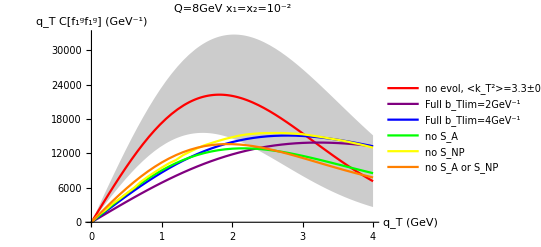
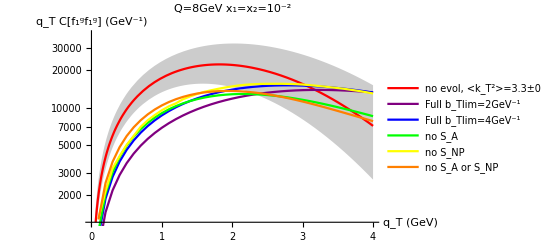

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListPlot[{qtCf1f1bt2Q8,qtCf1f1bt4Q8,qtCf1f1NoSabt4Q8,qtCf1f1NoSnpQ8,qtCf1f1NoSQ8},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},LogPlot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListLogPlot[{qtCf1f1bt2Q8,qtCf1f1bt4Q8,qtCf1f1NoSabt4Q8,qtCf1f1NoSnpQ8,qtCf1f1NoSQ8},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"]}
```

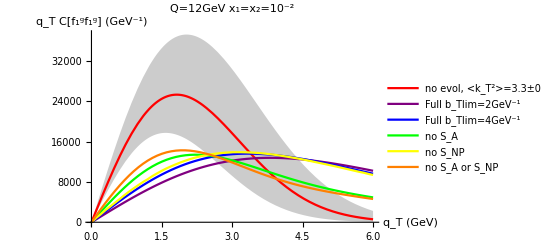
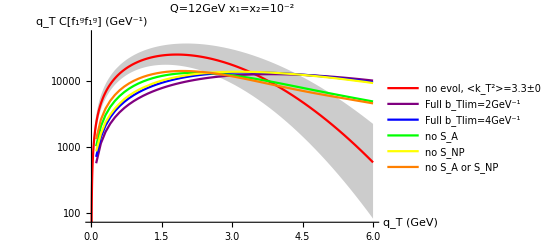

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListPlot[{qtCf1f1bt2Q12,qtCf1f1bt4Q12,qtCf1f1NoSabt4Q12,qtCf1f1NoSnpQ12,qtCf1f1NoSQ12},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},LogPlot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListLogPlot[{qtCf1f1bt2Q12,qtCf1f1bt4Q12,qtCf1f1NoSabt4Q12,qtCf1f1NoSnpQ12,qtCf1f1NoSQ12},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"]}
```

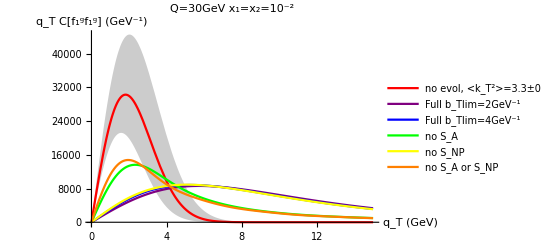
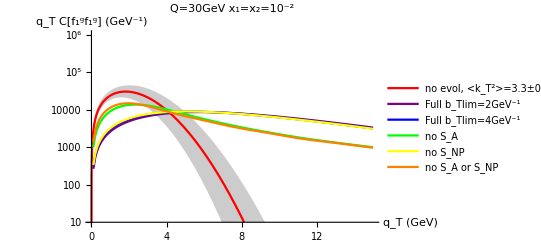

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""}]],ListPlot[{qtCf1f1bt2Q30,qtCf1f1bt4Q30,qtCf1f1NoSabt4Q30,qtCf1f1NoSnpQ30,qtCf1f1NoSQ30},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},LogPlot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None},PlotLegends->{"","no evol, <k_T^2>=3.3±0.8 GeV^2",""},PlotRange->{10,10^6}]],ListLogPlot[{qtCf1f1bt2Q30,qtCf1f1bt4Q30,qtCf1f1NoSabt4Q30,qtCf1f1NoSnpQ30,qtCf1f1NoSQ30},Joined->True,PlotStyle->{Purple,Blue,Green,Yellow,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_A","no S_NP","no S_A or S_NP"},PlotRange->{10,10^6}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

If one replaces the TMDs by simple PDFs evaluated at a scale μ=Q, then the whole b_T-dependence in the convolution’s integrand is b_T J_0(b_T q_T)and the PDFs are constant. J_0oscillations tend towards a constant amplitude at large b_T. Therefore b_T J_0(b_T q_T) oscillations linearly increase with b_T.The integral diverges, as can easily be seen when doing the integration in momentum space.

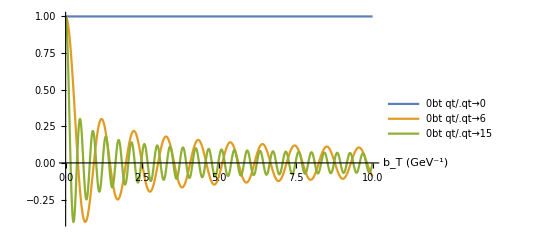
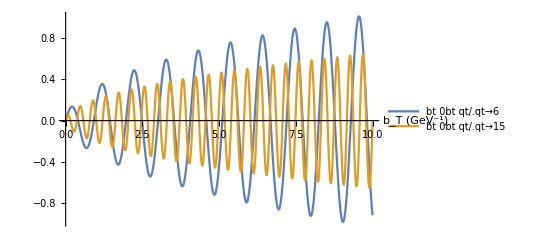

```mathematica
{Plot[{BesselJ[0,bt qt]/.qt->0,BesselJ[0,bt qt]/.qt->6,BesselJ[0,bt qt]/.qt->15},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{bt  BesselJ[0,bt qt]/.qt->6,bt  BesselJ[0,bt qt]/.qt->15},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

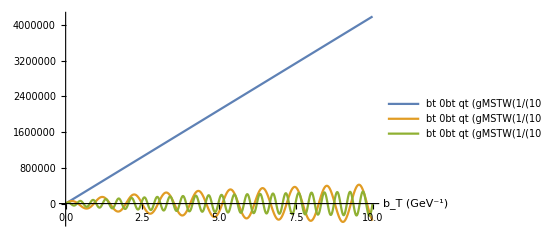

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->0,bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->15},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->0,{bt,0,∞},MaxRecursion->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in bt near {bt} = {1.98014577265121×10^459044}. NIntegrate obtained 1.71443540159204×10^114458344 and 1.71443540159204×10^114458344 for the integral and error estimates.

1.71443540159204×10^114458344

```mathematica
NIntegrate[qt*bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->0,{bt,0,∞},MaxRecursion->20]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->6,{bt,0,∞}]
```

NIntegrate::nconv: This oscillatory integral might not be convergent.

NIntegrate[bt BesselJ[0,bt qt] gMSTW[1/10^2,8]^2/.qt→6,{bt,0,∞}]

```mathematica
NIntegrate[qt*bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->6,{bt,0,∞}]
```

NIntegrate::nconv: This oscillatory integral might not be convergent.

NIntegrate[qt bt BesselJ[0,bt qt] gMSTW[1/10^2,8]^2/.qt→6,{bt,0,∞}]

Replacing the scale μ=Q in the PDFs by μ=μ_Bfrozen(b_T,Q) implements a b_T-dependence in the PDFs. The consequence will be that at larger b_T (>2 GeV^-1 approximately), the PDFs are strongly suppressed ; but because μ_Bfrozen also knows a lower bound, the PDFs will also reach a lower bound and will not keep decreasing ; thus although the oscillations are in a first time dampened by the decrease in value of the PDFs, once the latter reach their bound, they will no longer counter the amplification of oscillations with b_T. The integrand is still divergent at b_T=0 for q_T=0, but when multiplied by q_T (which appears multiplying the integrand in dσ/dq_T), the divergence cancels because q_T=0.

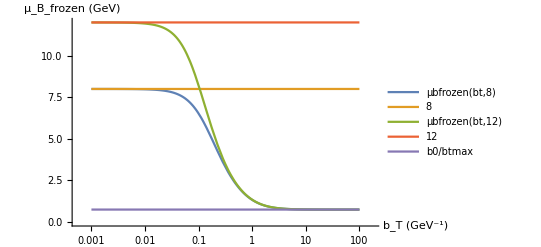
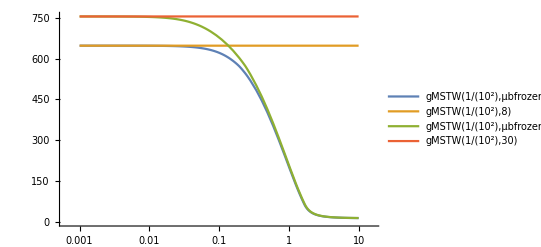

```mathematica
{LogLinearPlot[{μbfrozen[bt,8],8,μbfrozen[bt,12],12,b0/btmax},{bt,10^-3,10^2},PlotRange->{0,12},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","μ_B_frozen (GeV)"}],LogLinearPlot[{gMSTW[10^-2,μbfrozen[bt,8]],gMSTW[10^-2,8],gMSTW[10^-2,μbfrozen[bt,30]],gMSTW[10^-2,30]},{bt,10^-3,10},PlotLegends->"Expressions"]}
```

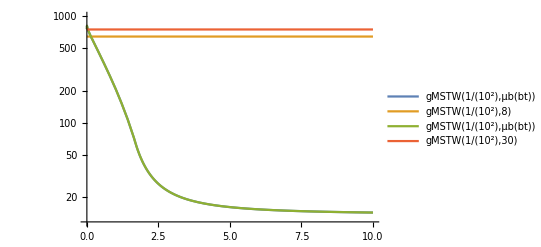

```mathematica
LogPlot[{gMSTW[10^-2,μb[bt]],gMSTW[10^-2,8],gMSTW[10^-2,μb[bt]],gMSTW[10^-2,30]},{bt,0,10},PlotLegends->"Expressions"]
```

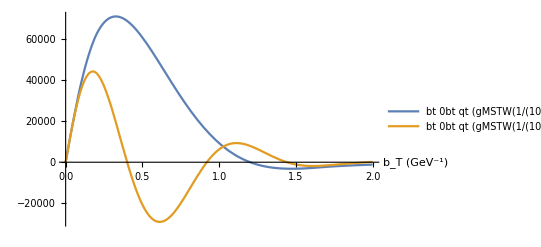
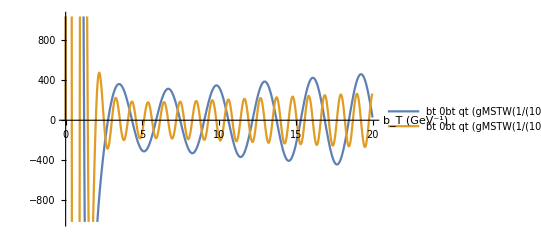

```mathematica
{Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6},{bt,0,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6},{bt,0,20},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->0,{bt,0,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {8.16907×10^224}. NIntegrate obtained 7.78676206227989×10^55896 and 7.78676206227989×10^55896 for the integral and error estimates.

7.78676206227989×10^55896

```mathematica
NIntegrate[qt*bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->0,{bt,0,∞}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
gMSTW[10^-2,20]
```

730.38

```mathematica
gMSTW[20/8000,20]
```

6821.06

```mathematica
NIntegrate[(1/10^-2-1/y2)gMSTW[y2,μb[bt]],{y2,10^-2,1},{bt,0,30},PrecisionGoal->4]
```

4656.15

```mathematica
NIntegrate[(1/(20/8000)-1/y2)gMSTW[y2,μb[bt]],{y2,20/8000,1},{bt,0,30},PrecisionGoal->4]
```

24622.7

Even though the PDFs tend towards a constant value and the oscillations resume increasing at large b_T, they are now tamed enough to make the integral finite. The value of the integral is mostly determined by low b_T values, where there is an imbalance in the oscillations. At large b_T, the oscillations get more and more balanced, and therefore contribute less and less to the integral, even if their amplitude increases.

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6,{bt,0,∞}]
```

4252.06

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->15,{bt,0,∞}]
```

148.931

At b_T≃10^6, the oscillations’ amplitude is very large, yet the integral over a period π is very close to 0.

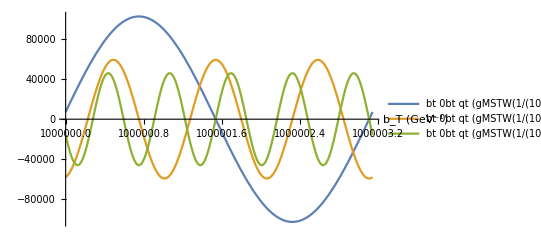

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->10},{bt,1000000,1000000+π},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6,{bt,1000000,1000000+π},MaxRecursion->20]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00324529 and 2.04983×10^-6 for the integral and error estimates.

-0.00324529

Compared with a non-evolved gaussian b_T-dependence that supresses any contribution beyond 2 GeV^-1, the PDF still allows a small contribution for b_Tvalues larger than 2 GeV^-1 but the suppression happens earlier. The consequence is a notable difference of behaviour of the integrand with increasing values of q_T. In the gaussian case, the oscillations balance is reached very quickly with increasing q_T, meaning the integral (and therefore dσ/dq_T) becomes quickly negligible at large q_T. Moreover, the exponential decrease in b_T of the gaussian cancels the linear increase from the b_Tfactor ; if larger b_Tvalues contributed a bit, they cannot at all in the gaussian case.
In the g(x,μ_Bfrozen) case, the balance is reached much slowlier, allowing for a non-negligible q_T-spectrum at much larger values ; in addition, the larger b_T values, even though they contribute less, can still increase the value of the integral (moderate b_T, although this second effect might be negligible): the spectrum therefore develops a tail.
Nevertheless, the small-q_T shapes of the spectra are very similar (the peaks are at the same position, but this is a coïncidence, taking a different <k_T^2> for the Gaussian would shift the peak).

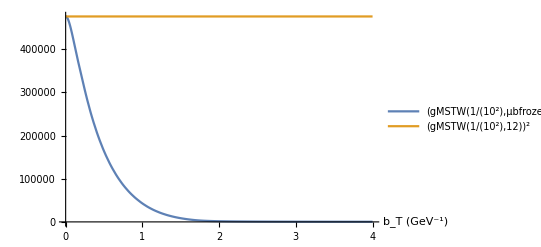
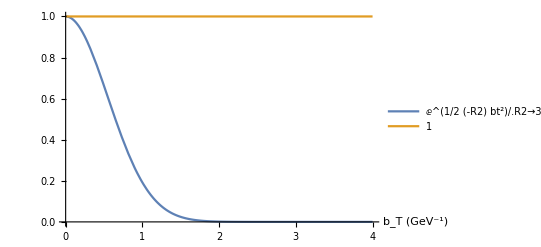

```mathematica
{Plot[{gMSTW[10^-2,μbfrozen[bt,12]]^2,gMSTW[10^-2,12]^2},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{ⅇ^((-R2 bt^2)/2)/.R2->3.3,1},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

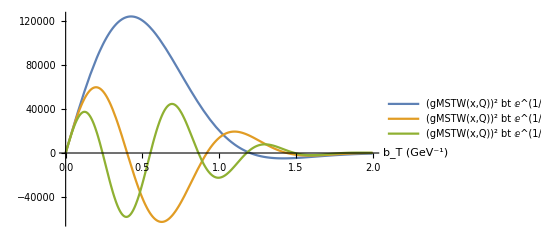
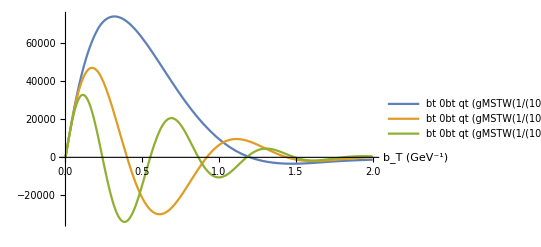

```mathematica
{Plot[{ gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->2/.R2->3.3,gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->6/.R2->3.3,gMSTW[x,Q]^2 bt ⅇ^((-R2 bt^2)/2)BesselJ[0,bt qt]/.x->10^-2/.Q->12/.qt->10/.R2->3.3},{bt,0,2},PlotRange->All,PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->10},{bt,10^-3,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

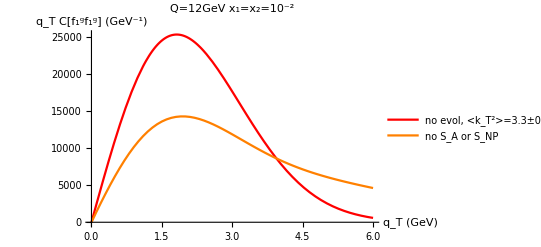

```mathematica
Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[qtCf1f1NoSQ12,Joined->True,PlotStyle->Orange,PlotLegends->{"no S_A or S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"]
```

The addition of the perturbative Sudakov factor S_A can enhance the previously observed effect of b_T-narrowing of integrand ↔ q_T-broadening of integral. Even though, as the PDFs, it knows a lower bound due to the use of the scale μ_Bfrozen, it can suppress even further large b_T values, this suppression knowing a Q-dependence. At Q=8GeV, the Sudakov factor is softly suppressing, and its effect not so strong. Yet, it stills allows to reduce the decrease in the values of the integrals for two given q_T. Combined with the q_Tfactor added to describe dσ/dq_T, this even allows to shift the peak of the q_T-spectrum towards larger values of q_T, in addition to developing a tail. (if we were plotting C[f_1^g f_1^g] alone, it would always be maximal at q_T=0)
The enhancement due to S_A>1 for b_T ≃ 0.1 - 1 GeV^-1 may also contribute to the increased contribution of small-b_T values. This effect might not be physically sound.

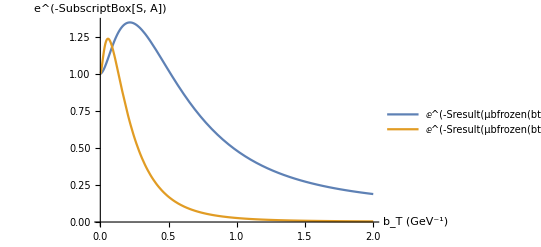
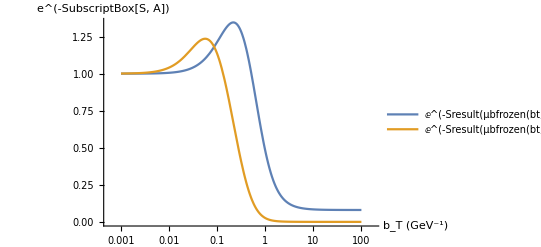

```mathematica
{Plot[{ⅇ^(-Sresult[μbfrozen[bt,8],8,μb[bt]]),ⅇ^(-Sresult[μbfrozen[bt,30],30,μb[bt]])},{bt,0,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}],LogLinearPlot[{ⅇ^(-Sresult[μbfrozen[bt,8],8,μb[bt]]),ⅇ^(-Sresult[μbfrozen[bt,30],30,μb[bt]])},{bt,10^-3,10^2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}]}
```

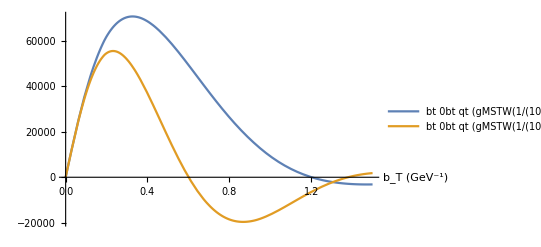
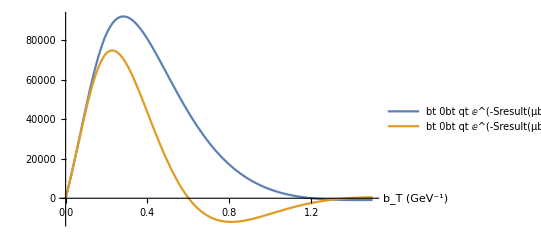

```mathematica
{Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->4},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],

Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->2,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->4},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

At large Q, the effect is much stronger. For Q=30GeV, the Sudakov factor makes negligible everything beyond b_T=1 GeV^-1, making a noticeably stronger cut in the b_Tintegrand. In such a configuration, the difference between the integrands for two q_Tvalues is even smaller, and the q_T-spectrum is noticeably broader, and its peak at a noticeably larger q_Tvalue.

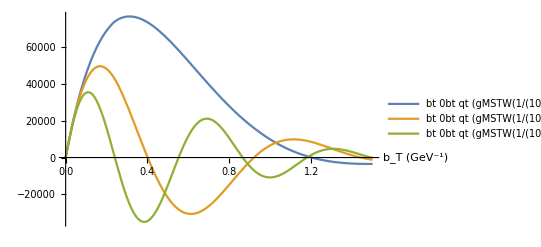
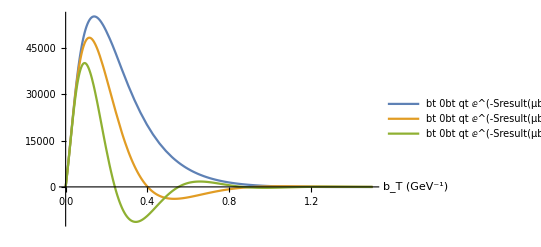

```mathematica
{Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->2,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->10},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],

Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->2,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->10},{bt,0,1.5},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->2,{bt,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 18271.9 and 0.477855 for the integral and error estimates.

18271.9

```mathematica
NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->4,{bt,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 13499.6 and 0.219031 for the integral and error estimates.

13499.6

```mathematica
NIntegrate[qt bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->2,{bt,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 36543.8 and 0.95571 for the integral and error estimates.

36543.8

```mathematica
NIntegrate[qt bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->4,{bt,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {4.81037×10^7}. NIntegrate obtained 53998.5 and 0.876126 for the integral and error estimates.

53998.5

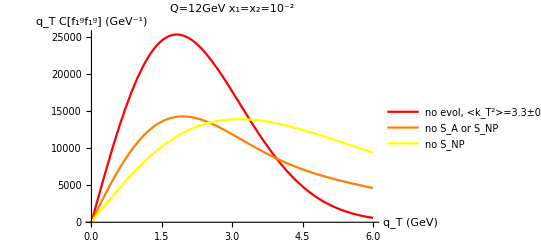
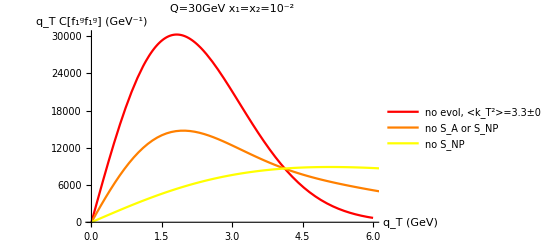

```mathematica
{Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,12],{qt,0,6},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ12,qtCf1f1NoSnpQ12},Joined->True,PlotStyle->{Orange,Yellow},PlotLegends->{"no S_A or S_NP","no S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,30],{qt,0,6},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ30,qtCf1f1NoSnpQ30},Joined->True,PlotStyle->{Orange,Yellow},PlotLegends->{"no S_A or S_NP","no S_NP"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

It could be that the change of scale in the PDFs may also change their large-b_Tsuppressing power by narrowing their b_T-slope. As one can see, this is not the case ; the only change is therefore a numerical overall factor. It is also seen in the absence of change in the shape of the q_T-spectrum with no S_A when Q varies.

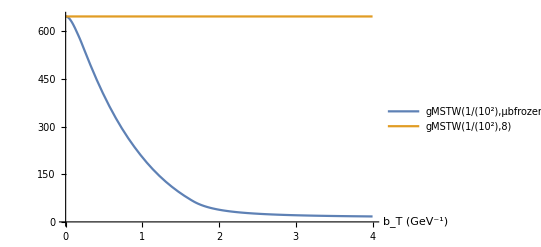
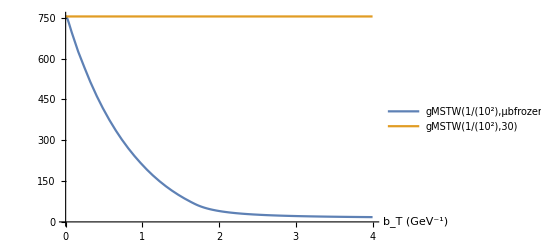

```mathematica
{Plot[{gMSTW[10^-2,μbfrozen[bt,8]],gMSTW[10^-2,8]},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],Plot[{gMSTW[10^-2,μbfrozen[bt,30]],gMSTW[10^-2,30]},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

The possibility for the nonperturbative Sudakov factor S_NP to broaden the q_T-spectrum, is directly connected to its possibility to narrow down even further the b_T-integrand (or not). A S_NP becoming small at b_Tlim= 4 GeV^-1or larger will be less narrowing than S_A and therefore have little to no broadening effect on the q_T-spectrum. A narrower S_NP (b_Tlim=2 GeV^-1) will have a moderate but noticeable effect at small Q=8GeV. At large Q, where the perturbative Sudakov factor is strongly suppressing (b_T>1 GeV^-1 already suppressed), the nonperturbative Sudakov factor will have almost no visible effect.

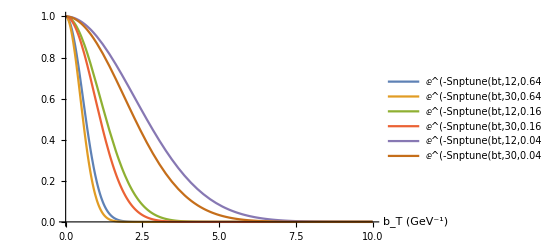
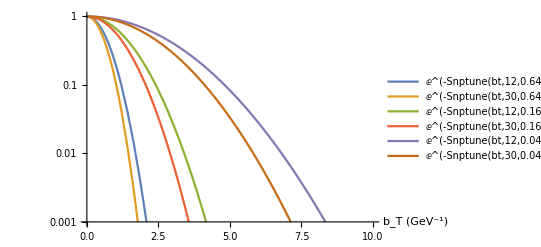

```mathematica
{Plot[{ⅇ^(-Snptune[bt,12,0.64]),ⅇ^(-Snptune[bt,30,0.64]),ⅇ^(-Snptune[bt,12,0.16]),ⅇ^(-Snptune[bt,30,0.16]),ⅇ^(-Snptune[bt,12,0.04]),ⅇ^(-Snptune[bt,30,0.04])},{bt,0,10},PlotRange->All,PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],LogPlot[{ⅇ^(-Snptune[bt,12,0.64]),ⅇ^(-Snptune[bt,30,0.64]),ⅇ^(-Snptune[bt,12,0.16]),ⅇ^(-Snptune[bt,30,0.16]),ⅇ^(-Snptune[bt,12,0.04]),ⅇ^(-Snptune[bt,30,0.04])},{bt,0,10},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",},PlotRange->{{0,10},{10^-3,1}}]}
```

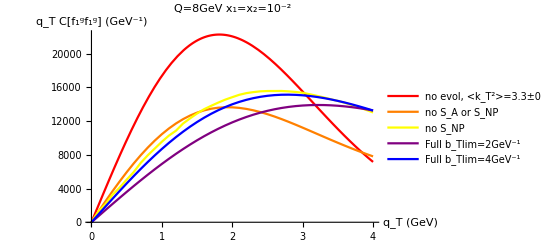
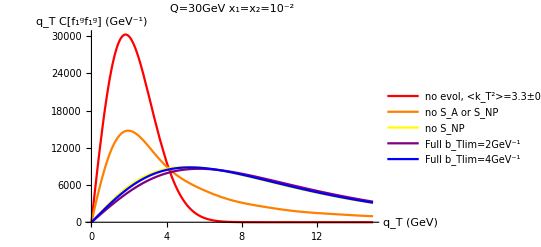

```mathematica
{Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,8],{qt,0,4},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ8,qtCf1f1NoSnpQ8,qtCf1f1bt2Q8,qtCf1f1bt4Q8},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue},PlotLegends->{"no S_A or S_NP","no S_NP","Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[Plot[qtCf1f1GausPlot[qt,3.3,10^-2,30],{qt,0,15},PlotStyle->Red,PlotLegends->{"no evol, <k_T^2>=3.3±0.8 GeV^2"}],ListPlot[{qtCf1f1NoSQ30,qtCf1f1NoSnpQ30,qtCf1f1bt2Q30,qtCf1f1bt4Q30},Joined->True,PlotStyle->{Orange,Yellow,Purple,Blue},PlotLegends->{"no S_A or S_NP","no S_NP","Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

The perturbative expressions used for f_1^g and h_1^(⊥g) as well as the perturbative Sudakov factor S_A are given at leading order in α_s. The corrections to these expressions are one order higher in α_s. They are kept reasonably small by keeping α_s small even at large b_T (indeed α_s(b_0/b_T) becomes larger than 1 for b_T>2.5 GeV^-1), using the b_T^*-prescription: b_T→ b_T^*<b_Tmax. Therefore at distances smaller than b_Tmax, α_s is considered small enough for the leading order expressions to be valid. Beyond this limit, the nonperturbative Sudakov factor is supposed to take over. This means that the action of S_NP on the b_T-integrand should not be too strong in the perturbative region. Therefore one cannot take a too narrow e^-S_NP regarding the value of b_Tmax.

```mathematica
btstartune[bt_,btmax_]:=bt/(√(1+bt^2/btmax^2));
```

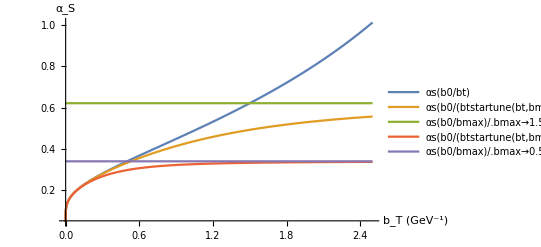

```mathematica
Plot[{αs[b0/bt],αs[b0/btstartune[bt,bmax]]/.bmax->1.5,αs[b0/bmax]/.bmax->1.5,αs[b0/btstartune[bt,bmax]]/.bmax->0.5,αs[b0/bmax]/.bmax->0.5},{bt,0,2.5},PlotRange->All,AxesLabel->{"b_T (GeV^-1)","α_S"},PlotLegends->"Expressions"]
```

```mathematica
μbfrozentune[bt_,Q_,btmax_]:=(Q b0)/(√(Q^2 btstartune[bt,btmax]^2+b0^2));
```

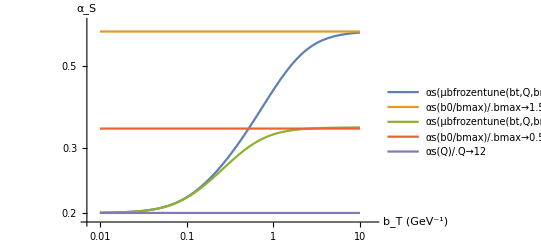

```mathematica
LogLogPlot[{αs[μbfrozentune[bt,Q,bmax]]/.Q->12/.bmax->1.5,αs[b0/bmax]/.bmax->1.5,αs[μbfrozentune[bt,Q,bmax]]/.Q->12/.bmax->0.5,αs[b0/bmax]/.bmax->0.5,αs[Q]/.Q->12},{bt,10^-2,10},PlotRange->All,AxesLabel->{"b_T (GeV^-1)","α_S"},PlotLegends->"Expressions"]
```

We see that the fitted parametrisation on quark data by Aybat-Rogers already has a very strong suppression effect at b_Tmax=1.5 GeV^-1 that was considered for the fit, same for S_NPtune with b_Tlim=2 GeV^-1.

```mathematica
ⅇ^(-Snptune[btmax,8,0.64])
```

0.0500669

```mathematica
ⅇ^(-Snptune[btmax,30,0.64])
```

0.00746355

```mathematica
ⅇ^(-Snptune[btmax,8,0.04])
```

0.82932

```mathematica
ⅇ^(-Snptune[btmax,30,0.04])
```

0.736307

```mathematica
Snp[bt_,Q_,x2_]:=9/4(0.184Log[Q/(2(1.6))]+0.201(1+2(-0.129)Log[(0.09x2)/(0.009+x2)]))bt^2;
```

```mathematica
ⅇ^(-Snp[btmax,8,0.09])
```

0.079797

```mathematica
ⅇ^(-Snp[btmax,30,0.09])
```

0.0232957

## q_T-spectrum with uncertainty bands

Computing and plotting  q_T C[f_1^g f_1^g] for Gaussian f_1^gwith <k_T^2> =3.3±0.8 GeV^2 (red curve with grey uncertainty bands), and for evolved f_1^g using S_NP with b_Tlim ∈ [2;8] GeV^-1 (blue band)
We also compute the uncertainty band when varying the scale μ ∈ [ 1/2 ; 2 ] x μ_Bfrozen (brown band) ; but this variation is not independent to other variations such as the S_NP one, so there is no point trying to estimate the total uncertainty as the parameters are too unconstrained due to the lack of data

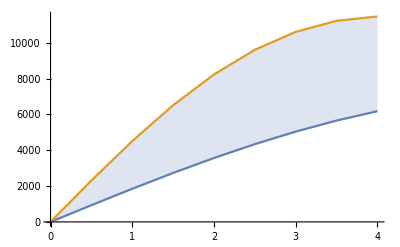
{(0. | 0.
0.5 | 932.11
1. | 1847.6
1.5 | 2730.34
2. | 3565.15
2.5 | 4338.23
3. | 5037.54
3.5 | 5653.07
4. | 6177.11),(0. | 0.
0.5 | 2306.52
1. | 4508.03
1.5 | 6507.98
2. | 8225.71
2.5 | 9602.03
3. | 10602.4
3.5 | 11217.5
4. | 11461.3),-Graphics-}

```mathematica
qtlist=Range[0,4,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ8=Table[{qt,Min[Table[qtCf1f1tunebt[10^-2,8,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ8=Table[{qt,Max[Table[qtCf1f1tunebt[10^-2,8,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
qtlist=Range[0,4,0.2];
Blist=Range[0.5,2,0.25];
{MatrixForm[minlistμQ8A0p16=Table[{qt,Min[Table[qtCf1f1tunebtμ[10^-2,8,qt,0.16,B],{B,Blist}]]},{qt,qtlist}]],MatrixForm[maxlistμQ8A0p16=Table[{qt,Max[Table[qtCf1f1tunebtμ[10^-2,8,qt,0.16,B],{B,Blist}]]},{qt,qtlist}]],ListPlot[{minlistμQ8A0p16,maxlistμQ8A0p16},Filling->{1->{2}},FillingStyle->Darker,Joined->True]};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.411911}. NIntegrate obtained 13825. and 0.111665 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.11115}. NIntegrate obtained 31500. and 0.0441091 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.207487}. NIntegrate obtained 58741.2 and 0.100191 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

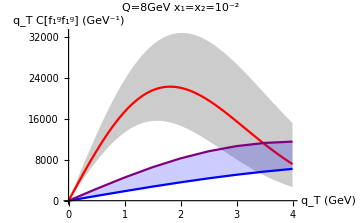
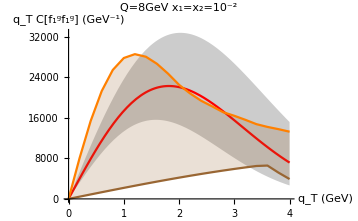
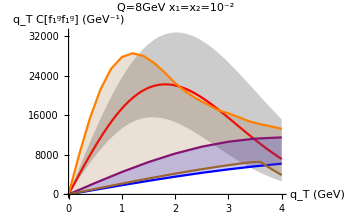

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistμQ8A0p16,maxlistμQ8A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],ListPlot[{minlistμQ8A0p16,maxlistμQ8A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"]}
```

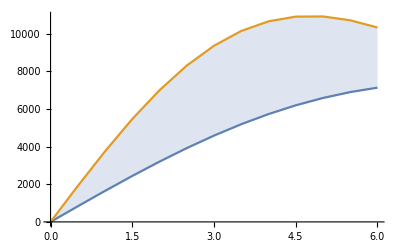
{(0. | 0.
0.5 | 828.761
1. | 1645.98
1.5 | 2440.39
2. | 3201.24
2.5 | 3918.57
3. | 4583.38
3.5 | 5187.88
4. | 5725.57
4.5 | 6191.4
5. | 6581.79
5.5 | 6894.69
6. | 7129.52),(0. | 0.
0.5 | 1907.26
1. | 3748.57
1.5 | 5462.18
2. | 6994.32
2.5 | 8302.21
3. | 9356.11
3.5 | 10140.2
4. | 10652.2
4.5 | 10902.5
5. | 10911.6
5.5 | 10707.9
6. | 10325.1),-Graphics-}

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ12=Table[{qt,Min[Table[qtCf1f1tunebt[10^-2,12,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ12=Table[{qt,Max[Table[qtCf1f1tunebt[10^-2,12,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 11985.7 and 0.0367538 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 10738.1 and 0.0372727 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.238476}. NIntegrate obtained 9727.85 and 0.0352106 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

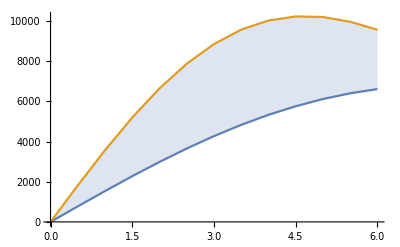
{(0. | 0.
0.5 | 774.118
1. | 1537.27
1.5 | 2278.73
2. | 2988.32
2.5 | 3656.58
3. | 4275.01
3.5 | 4836.25
4. | 5334.19
4.5 | 5764.14
5. | 6122.81
5.5 | 6408.36
6. | 6620.38),(0. | 0.
0.5 | 1818.93
1. | 3572.92
1.5 | 5201.27
2. | 6651.3
2.5 | 7881.39
3. | 8863.
3.5 | 9581.48
4. | 10035.8
4.5 | 10237.1
5. | 10207.
5.5 | 9974.38
6. | 9573.12),-Graphics-}

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlist2btQ12=Table[{qt,Min[Table[qtCf1f1tunebt2[10^-2,12,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlist2btQ12=Table[{qt,Max[Table[qtCf1f1tunebt2[10^-2,12,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlist2btQ12,maxlist2btQ12},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
qtlist=Range[0,6,0.2];
Blist=Range[0.5,2,0.25];
{MatrixForm[minlistμQ12A0p16=Table[{qt,Min[Table[qtCf1f1tunebtμ[10^-2,12,qt,0.16,B],{B,Blist}]]},{qt,qtlist}]],MatrixForm[maxlistμQ12A0p16=Table[{qt,Max[Table[qtCf1f1tunebtμ[10^-2,12,qt,0.16,B],{B,Blist}]]},{qt,qtlist}]],ListPlot[{minlistμQ12A0p16,maxlistμQ12A0p16},Filling->{1->{2}},FillingStyle->Darker,Joined->True]};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.0830575}. NIntegrate obtained 11063.5 and 0.016828 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.173997}. NIntegrate obtained 24625.8 and 0.0437124 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.24168}. NIntegrate obtained 44848.8 and 0.178564 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

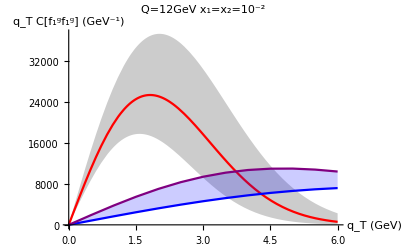
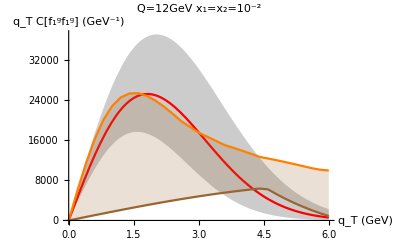
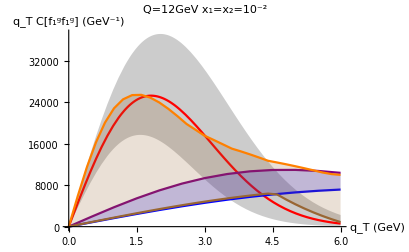

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistμQ12A0p16,maxlistμQ12A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],ListPlot[{minlistμQ12A0p16,maxlistμQ12A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"]}
```

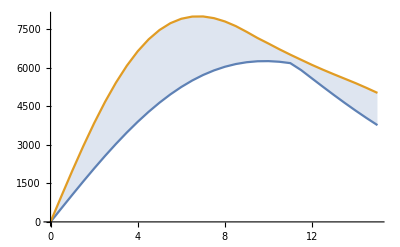
{(0. | 0.
0.5 | 529.489
1. | 1054.69
1.5 | 1571.36
2. | 2075.42
2.5 | 2562.92
3. | 3030.2
3.5 | 3473.86
4. | 3890.82
4.5 | 4278.41
5. | 4634.33
5.5 | 4956.68
6. | 5244.04
6.5 | 5495.39
7. | 5710.15
7.5 | 5888.18
8. | 6029.72
8.5 | 6135.42
9. | 6206.26
9.5 | 6243.55
10. | 6248.87
10.5 | 6224.06
11. | 6171.15
11.5 | 5898.46
12. | 5573.3
12.5 | 5250.31
13. | 4932.77
13.5 | 4623.29
14. | 4323.83
14.5 | 4035.87
15. | 3760.4),(0. | 0.
0.5 | 1004.72
1. | 1990.71
1.5 | 2939.95
2. | 3835.83
2.5 | 4663.73
3. | 5411.49
3.5 | 6069.75
4. | 6632.12
4.5 | 7095.16
5. | 7458.34
5.5 | 7723.7
6. | 7895.57
6.5 | 7980.16
7. | 7985.07
7.5 | 7918.91
8. | 7790.83
8.5 | 7610.19
9. | 7386.15
9.5 | 7146.1
10. | 6931.81
10.5 | 6709.59
11. | 6500.29
11.5 | 6299.94
12. | 6100.75
12.5 | 5914.56
13. | 5737.07
13.5 | 5564.85
14. | 5392.
14.5 | 5207.49
15. | 5013.56),-Graphics-}

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ30=Table[{qt,Min[Table[qtCf1f1tunebt[10^-2,30,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ30=Table[{qt,Max[Table[qtCf1f1tunebt[10^-2,30,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlist2btQ30=Table[{qt,Min[Table[qtCf1f1tunebt2[10^-2,30,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlist2btQ30=Table[{qt,Max[Table[qtCf1f1tunebt2[10^-2,30,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlist2btQ30,maxlist2btQ30},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

$Aborted

```mathematica
qtlist=Range[0,15,0.2];
Blist=Range[0.5,2,0.25];
{MatrixForm[minlistμQ30A0p16=Table[{qt,Min[Table[qtCf1f1tunebtμ[10^-2,30,qt,0.16,B],{B,Blist}]]},{qt,qtlist}]],MatrixForm[maxlistμQ30A0p16=Table[{qt,Max[Table[qtCf1f1tunebtμ[10^-2,30,qt,0.16,B],{B,Blist}]]},{qt,qtlist}]],ListPlot[{minlistμQ30A0p16,maxlistμQ30A0p16},Filling->{1->{2}},FillingStyle->Darker,Joined->True]};
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.141691}. NIntegrate obtained 4909.44 and 0.0193409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in bt near {bt} = {0.141691}. NIntegrate obtained 4909.44 and 0.0193409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

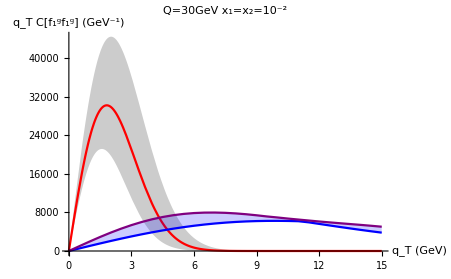
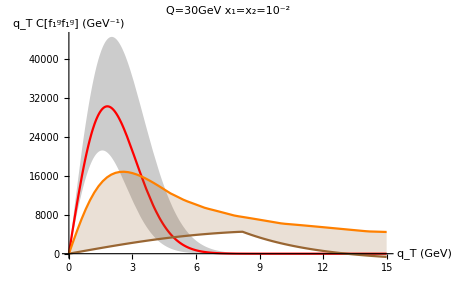
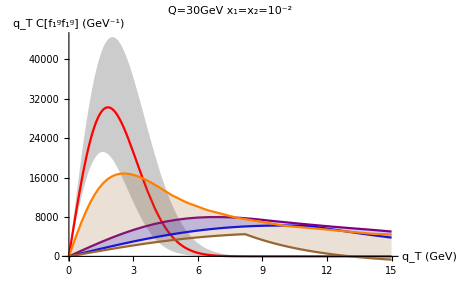

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistμQ30A0p16,maxlistμQ30A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],ListPlot[{minlistμQ30A0p16,maxlistμQ30A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

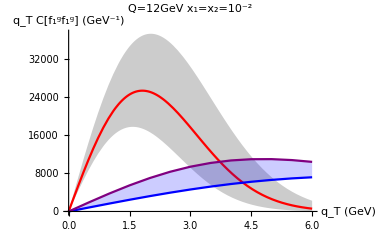
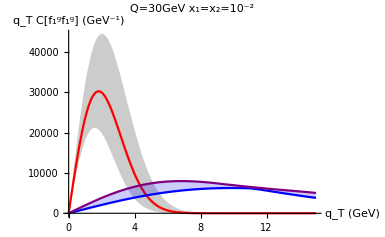

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlist2btQ12,maxlist2btQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2 with O(α_s^2)-S_A and btbar"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlist2btQ30,maxlist2btQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2 with O(α_s^2)-S_A and btbar"]}
```

```mathematica
MatrixForm[listnonevQ12=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6,0.1}]]];
```

```mathematica
MatrixForm[listnonevQ30=With[{R2=Interval[3.3+0.8{-1,1}]},Table[{qt,Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15,0.1}]]];
```

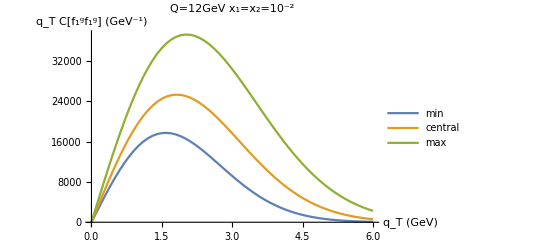
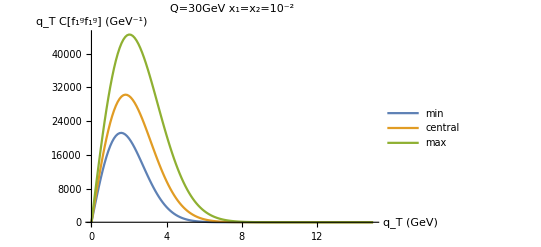

```mathematica
{ListPlot[{listnonevQ12[[All,{1,2}]],listnonevQ12[[All,{1,3}]],listnonevQ12[[All,{1,4}]]},Joined->True,AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLegends->{"min","central","max"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],
ListPlot[{listnonevQ30[[All,{1,2}]],listnonevQ30[[All,{1,3}]],listnonevQ30[[All,{1,4}]]},Joined->True,AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLegends->{"min","central","max"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

Exporting values for the q_T C[f_1^g f_1^g] plots

```mathematica
Export["qtCf1f1nonevboundsQ12.dat",listnonevQ12];
Export["qtCf1f1nonevboundsQ30.dat",listnonevQ30];
Export["qtCf1f1SnptuneboundsQ12.dat",Transpose[{minlistbtQ12[[All,1]],minlistbtQ12[[All,2]],maxlistbtQ12[[All,2]]}]];
Export["qtCf1f1SnptuneboundsQ30.dat",Transpose[{minlistbtQ30[[All,1]],minlistbtQ30[[All,2]],maxlistbtQ30[[All,2]]}]];
```

```mathematica
Export["qtCf1f1nonevboundsQ12.dat",listnonevQ12];
Export["qtCf1f1nonevboundsQ30.dat",listnonevQ30];
Export["qtCf1f1SnptuneboundsQ12.dat",Transpose[{minlist2btQ12[[All,1]],minlist2btQ12[[All,2]],maxlist2btQ12[[All,2]]}]];
Export["qtCf1f1SnptuneboundsQ30.dat",Transpose[{minlist2btQ30[[All,1]],minlist2btQ30[[All,2]],maxlist2btQ30[[All,2]]}]];
```

## x-dependence

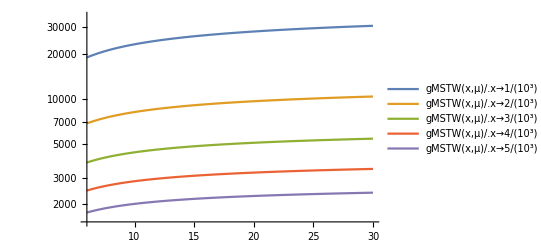
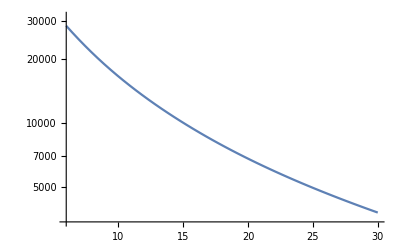
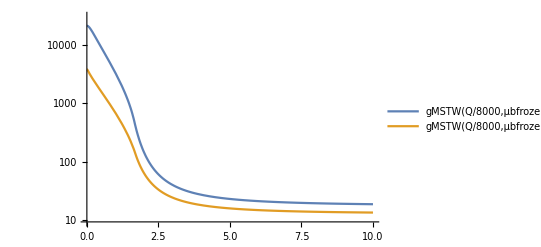

```mathematica
{LogPlot[{gMSTW[x,μ]/.x->10^-3,gMSTW[x,μ]/.x->2*10^-3,gMSTW[x,μ]/.x->3*10^-3,gMSTW[x,μ]/.x->4*10^-3,gMSTW[x,μ]/.x->5*10^-3},{μ,6,30},PlotLegends->"Expressions"],
LogPlot[gMSTW[Q/8000,Q],{Q,6,30},PlotLegends->"Expressions"],
LogPlot[{gMSTW[Q/8000,μbfrozen[bt,Q]]/.Q->8,gMSTW[Q/8000,μbfrozen[bt,Q]]/.Q->30},{bt,0,10},PlotLegends->"Expressions"]}
```

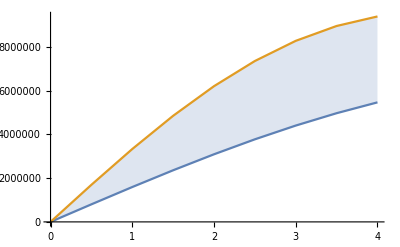
{(0. | 0.
0.5 | 802946.
1. | 1.59355×10^6
1.5 | 2.35978×10^6
2. | 3.09025×10^6
2.5 | 3.77448×10^6
3. | 4.4031×10^6
3.5 | 4.96833×10^6
4. | 5.4638×10^6),(0. | 0.
0.5 | 1.69528×10^6
1. | 3.33044×10^6
1.5 | 4.84932×10^6
2. | 6.2033×10^6
2.5 | 7.3541×10^6
3. | 8.27562×10^6
3.5 | 8.95465×10^6
4. | 9.39057×10^6),-Graphics-}

```mathematica
qtlist=Range[0,4,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ8x=Table[{qt,Min[Table[qtCf1f1tunebt[8/8000,8,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ8x=Table[{qt,Max[Table[qtCf1f1tunebt[8/8000,8,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ8x,maxlistbtQ8x},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

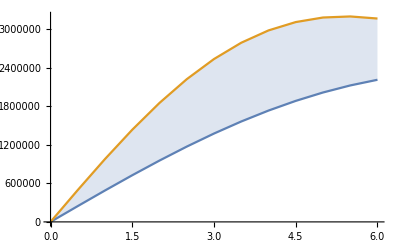
{(0. | 0.
0.5 | 245827.
1. | 488666.
1.5 | 725594.
2. | 953809.
2.5 | 1.17069×10^6
3. | 1.37386×10^6
3.5 | 1.5612×10^6
4. | 1.73091×10^6
4.5 | 1.88154×10^6
5. | 2.012×10^6
5.5 | 2.12157×10^6
6. | 2.20987×10^6),(0. | 0.
0.5 | 495836.
1. | 977902.
1.5 | 1.43317×10^6
2. | 1.85001×10^6
2.5 | 2.21879×10^6
3. | 2.53225×10^6
3.5 | 2.7857×10^6
4. | 2.97712×10^6
4.5 | 3.10695×10^6
5. | 3.17784×10^6
5.5 | 3.19428×10^6
6. | 3.1621×10^6),-Graphics-}

```mathematica
qtlist=Range[0,6,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ12x=Table[{qt,Min[Table[qtCf1f1tunebt[12/8000,12,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ12x=Table[{qt,Max[Table[qtCf1f1tunebt[12/8000,12,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ12x,maxlistbtQ12x},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

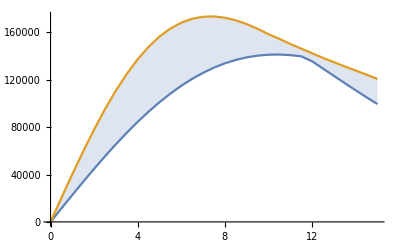
{(0. | 0.
0.5 | 11411.2
1. | 22737.6
1.5 | 33895.6
2. | 44803.8
2.5 | 55384.5
3. | 65564.
3.5 | 75274.5
4. | 84453.9
4.5 | 93047.5
5. | 101008.
5.5 | 108295.
6. | 114878.
6.5 | 120733.
7. | 125846.
7.5 | 130211.
8. | 133828.
8.5 | 136707.
9. | 138862.
9.5 | 140316.
10. | 141097.
10.5 | 141237.
11. | 140773.
11.5 | 139747.
12. | 135577.
12.5 | 129421.
13. | 123243.
13.5 | 117107.
14. | 111061.
14.5 | 105147.
15. | 99395.7),(0. | 0.
0.5 | 20313.
1. | 40293.2
1.5 | 59619.3
2. | 77993.
2.5 | 95148.
3. | 110859.
3.5 | 124945.
4. | 137277.
4.5 | 147775.
5. | 156407.
5.5 | 163187.
6. | 168172.
6.5 | 171450.
7. | 173140.
7.5 | 173380.
8. | 172322.
8.5 | 170125.
9. | 166951.
9.5 | 162958.
10. | 158430.
10.5 | 154476.
11. | 150209.
11.5 | 146248.
12. | 142323.
12.5 | 138402.
13. | 134764.
13.5 | 131204.
14. | 127728.
14.5 | 124272.
15. | 120571.),-Graphics-}

```mathematica
qtlist=Range[0,15,0.5];
Alist=Range[2,8,1];
{MatrixForm[minlistbtQ30x=Table[{qt,Min[Table[qtCf1f1tunebt[30/8000,30,qt,A],{A,Alist}]]},{qt,qtlist}]],MatrixForm[maxlistbtQ30x=Table[{qt,Max[Table[qtCf1f1tunebt[30/8000,30,qt,A],{A,Alist}]]},{qt,qtlist}]],ListPlot[{minlistbtQ30x,maxlistbtQ30x},Filling->{1->{2}},FillingStyle->Darker,Joined->True]}
```

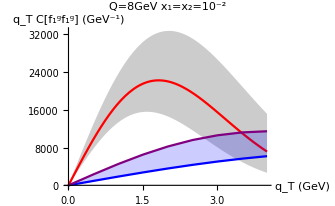
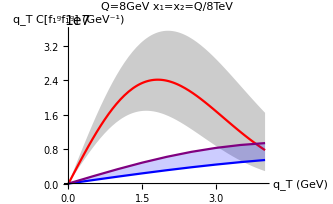

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,8]],qtCf1f1GausPlot[qt,3.3,10^-2,8],Max[qtCf1f1GausPlot[qt,R2,10^-2,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8,maxlistbtQ8},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,8/8000,8]],qtCf1f1GausPlot[qt,3.3,8/8000,8],Max[qtCf1f1GausPlot[qt,R2,8/8000,8]]},{qt,0,4},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ8x,maxlistbtQ8x},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=8GeV x_1=x_2=Q/8TeV"]}
```

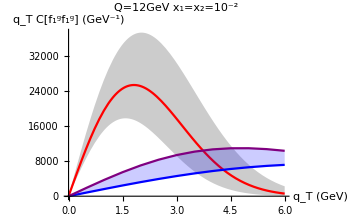
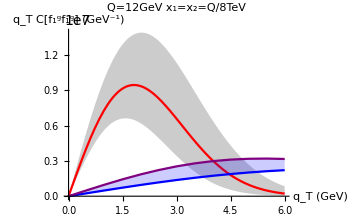

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,12]],qtCf1f1GausPlot[qt,3.3,10^-2,12],Max[qtCf1f1GausPlot[qt,R2,10^-2,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12,maxlistbtQ12},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,12/8000,12]],qtCf1f1GausPlot[qt,3.3,12/8000,12],Max[qtCf1f1GausPlot[qt,R2,12/8000,12]]},{qt,0,6},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ12x,maxlistbtQ12x},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=12GeV x_1=x_2=Q/8TeV"]}
```

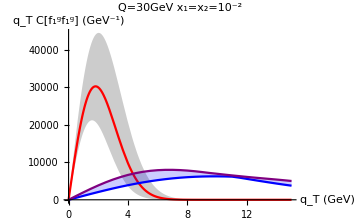
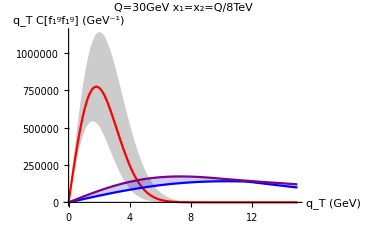

```mathematica
{Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],

Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,30/8000,30]],qtCf1f1GausPlot[qt,3.3,30/8000,30],Max[qtCf1f1GausPlot[qt,R2,30/8000,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30x,maxlistbtQ30x},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=Q/8TeV"]}
```

## Description of the different contributions to the different convolutions

The first difference between the cos(2ϕ) and cos(4ϕ) convolutions is that they contain a different Bessel function than the azimuthally independent terms : J_2 and J_4 respectively, instead of J_0. While the former is 1 at b_T=0, the two latter are 0 at b_T=0. Moreover, at equal value of q_T, they are more stretched in b_T, and J_4 more than J_2.

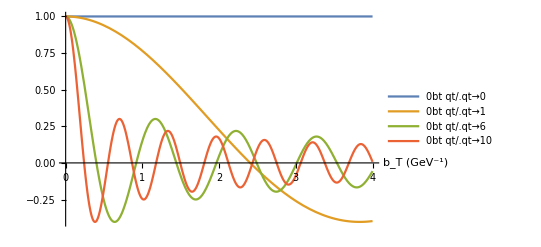
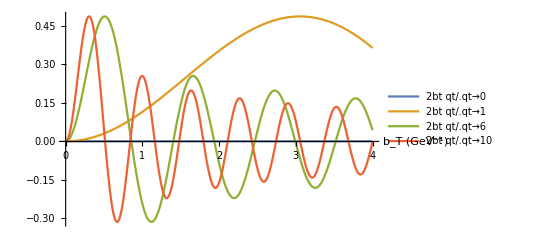
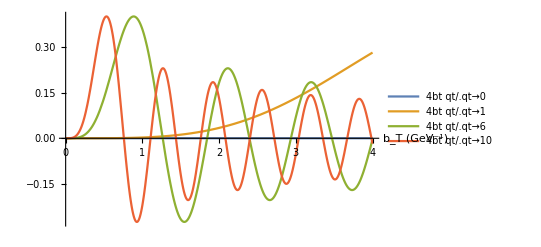
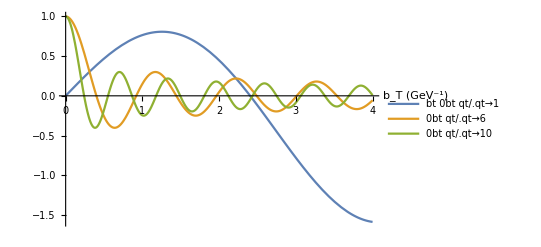
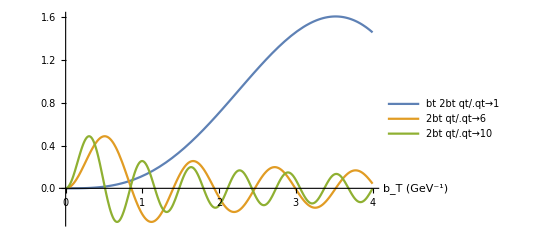
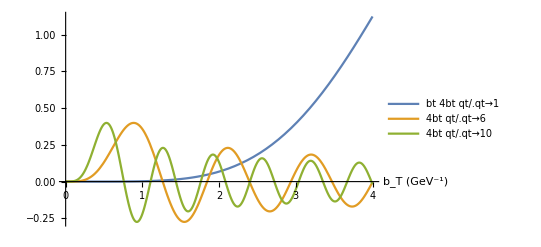

```mathematica
{Plot[{BesselJ[0,bt qt]/.qt->0,BesselJ[0,bt qt]/.qt->1,BesselJ[0,bt qt]/.qt->6,BesselJ[0,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{BesselJ[2,bt qt]/.qt->0,BesselJ[2,bt qt]/.qt->1,BesselJ[2,bt qt]/.qt->6,BesselJ[2,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{BesselJ[4,bt qt]/.qt->0,BesselJ[4,bt qt]/.qt->1,BesselJ[4,bt qt]/.qt->6,BesselJ[4,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],


Plot[{bt BesselJ[0,bt qt]/.qt->1,BesselJ[0,bt qt]/.qt->6,BesselJ[0,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{bt BesselJ[2,bt qt]/.qt->1,BesselJ[2,bt qt]/.qt->6,BesselJ[2,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}],
Plot[{bt BesselJ[4,bt qt]/.qt->1,BesselJ[4,bt qt]/.qt->6,BesselJ[4,bt qt]/.qt->10},{bt,0,4},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)",}]}
```

The other difference is that h_1^(⊥g) is not simply a collinear PDF, but a splitting function with the PDF as initial imput ; the action of the PDF is therefore modified. Moreover, it is proportional to α_s. It is naturally suppressed as α_s is small, but the running of α_s also adds a new dependence on the scale in the convolution. In C[w_0 h_1^(⊥g) h_1^(⊥g)] and C[w_4 h_1^(⊥g) h_1^(⊥g)], these effects are amplified as h_1^(⊥g) appears twice.

```mathematica
Cffint[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt] gMSTW[x,Q]^2;
```

```mathematica
Chhint[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt]((Nc αs[Q])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,Q](1/x-1/y2)gMSTW[y2,Q],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint[x_,Q_,qt_,bt_]:=bt BesselJ[2,qt bt]((Nc αs[Q])/π)NIntegrate[gMSTW[x,Q](1/x-1/y2)gMSTW[y2,Q],{y2,x,1}];
```

```mathematica
Cw4hhint[x_,Q_,qt_,bt_]:=bt BesselJ[4,qt bt]((Nc αs[Q])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,Q](1/x-1/y2)gMSTW[y2,Q],{y1,x,1},{y2,x,1}];
```

```mathematica
Chhqt3=Transpose[{Range[0,4,0.05],ParallelMap[Chhint[10^-2,8,3,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Chhqt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhqt3=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint[10^-2,8,3,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fhqt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hhqt3=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint[10^-2,8,3,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw4hhqt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cffqt3ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Cffint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

```mathematica
Cffqt10ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Cffint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

```mathematica
Chhqt3ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Chhint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Chhqt10ev=Transpose[{Range[0,4,0.05],ParallelMap[NIntegrate[Chhint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhqt3ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw3fhint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

```mathematica
Cw3fhqt10ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw3fhint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

```mathematica
Cw4hhqt3ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw4hhint[10^-2,8,3,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hhqt10ev=Transpose[{Range[0,4,0.1],ParallelMap[NIntegrate[Cw4hhint[10^-2,8,10,bt],{bt,0,#}] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

When the scale is fixed to μ=Q, these do not affect the b_T-dependence of the integrand and only change the normalisation. One can notice that the integrands containing α_s^2 are suppressed regarding the one containing only one power of α_s (the Bessel functions are more or less of the same size as can be seen above)

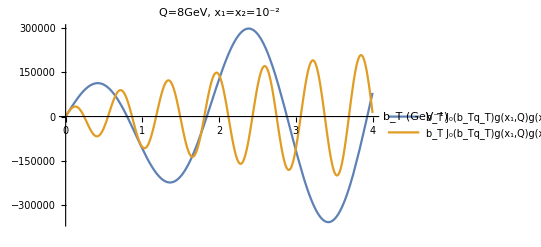

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->3,bt  BesselJ[0,bt qt] gMSTW[10^-2,8]^2/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=3GeV","b_T J_0(b_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2"]
```

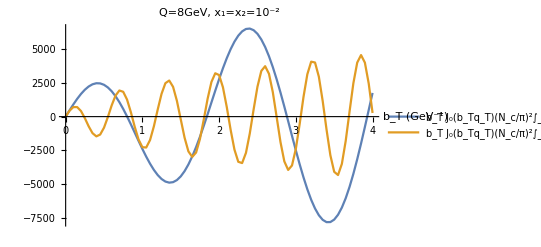

```mathematica
ListPlot[{Chhqt3,Chhqt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

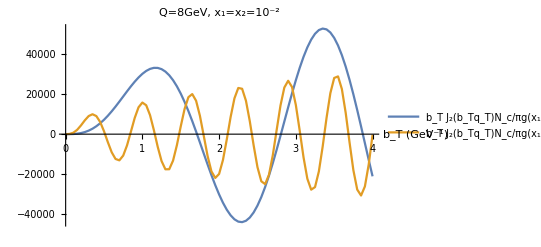

```mathematica
ListPlot[{Cw3fhqt3,Cw3fhqt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

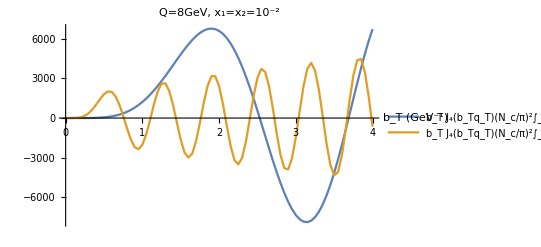

```mathematica
ListPlot[{Cw4hhqt3,Cw4hhqt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

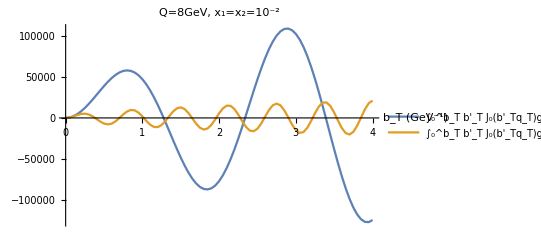

```mathematica
ListPlot[{Cffqt3ev,Cffqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=3GeV","∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,Q)g(x_2,Q)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

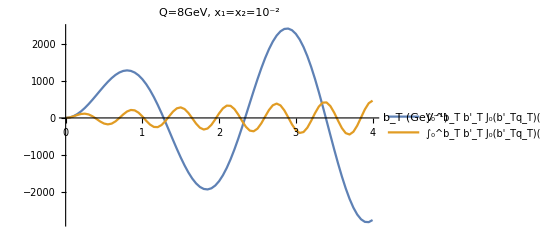

```mathematica
ListPlot[{Chhqt3ev,Chhqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

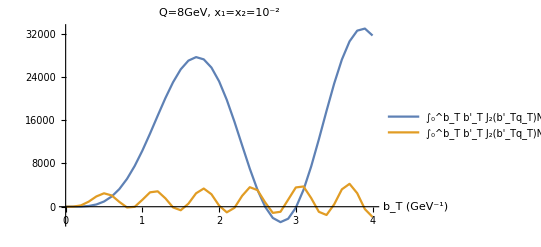

```mathematica
ListPlot[{Cw3fhqt3ev,Cw3fhqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,Q)∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

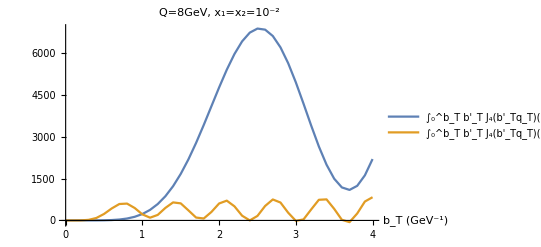

```mathematica
ListPlot[{Cw4hhqt3ev,Cw4hhqt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=3GeV","∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,Q)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,Q)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

When α_s is evaluated at μ_Bfrozen~1/b_T^*, it increasing with increasing distances b_T, until it reaches the upper bound α_s(b_0/b_Tmax). It will therefore contribute to magnify the large b_T values in the integrand.

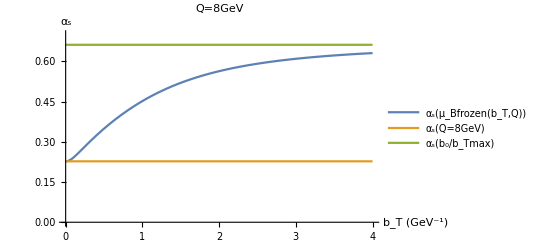
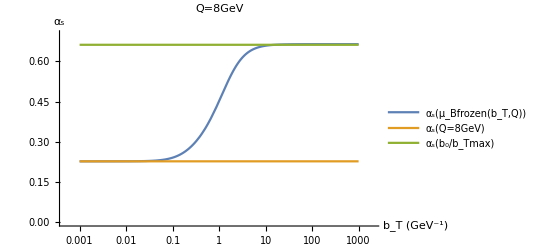

```mathematica
{Plot[{αs[μbfrozen[bt,8]],αs[8],αs[b0/btmax]},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"α_s(μ_Bfrozen(b_T,Q))","α_s(Q=8GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s"},PlotLabel->"Q=8GeV"],LogLinearPlot[{αs[μbfrozen[bt,8]],αs[8],αs[b0/btmax]},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"α_s(μ_Bfrozen(b_T,Q))","α_s(Q=8GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s"},PlotLabel->"Q=8GeV"]}
```

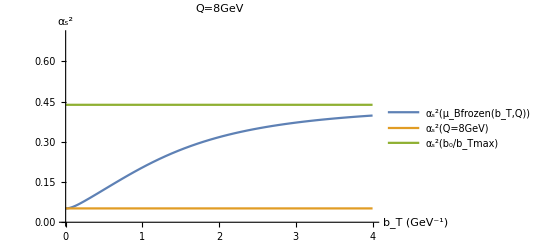
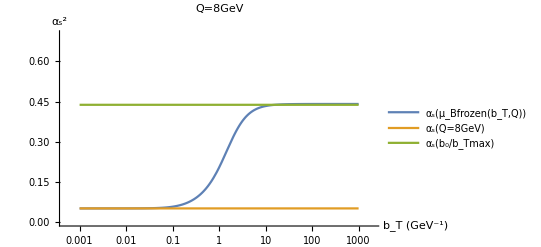

```mathematica
{Plot[{αs[μbfrozen[bt,8]]^2,αs[8]^2,αs[b0/btmax]^2},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"α_s^2(μ_Bfrozen(b_T,Q))","α_s^2(Q=8GeV)","α_s^2(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s^2"},PlotLabel->"Q=8GeV"],LogLinearPlot[{αs[μbfrozen[bt,8]]^2,αs[8]^2,αs[b0/btmax]^2},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"α_s(μ_Bfrozen(b_T,Q))","α_s(Q=8GeV)","α_s(b_0/b_Tmax)"},AxesLabel->{"b_T (GeV^-1)","α_s^2"},PlotLabel->"Q=8GeV"]}
```

```mathematica
ffmub[x_,Q_,bt_]:=gMSTW[x,μbfrozen[bt,Q]]^2;
fhmub[x_,Q_,bt_]:=gMSTW[x,μbfrozen[bt,Q]]NIntegrate[(1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1}];
hhmub[x_,Q_,bt_]:=NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
ffmubbt=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbt2=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt2=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt2=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbt3=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt3=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbfrozen[#,8]])/π)fhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt3=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbfrozen[#,8]])/π)^2 hhmub[10^-2,8,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbt4=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbt4=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbfrozen[#,30]])/π)fhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbt4=Transpose[{Range[0,4,0.05],ParallelMap[((Nc αs[μbfrozen[#,30]])/π)^2 hhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

When the scale of the PDF inside the splitting function is set to μ_Bfrozen as well, it still tends to suppress the large b_T values. But it does so softlier than the PDF alone, therefore favoring large b_T values in comparison with the simple PDF used for f_1^g inside C[f_1^gf_1^g]. The b_T-broadening is logically enhanced when the two TMDs are splitting functions.
When the two effects are combined in the complete expression of h_1^(⊥g), the b_T-broadening is even stronger as α_S suppresses the small-b_T values.

No significant difference between Q=8GeV and Q=30GeV for the splitting function (Q-dependence through μ_Bfrozen, abbreviated as μ_B in the following plots)

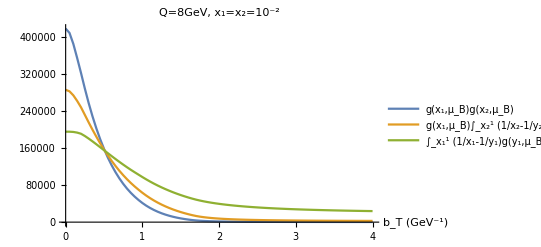
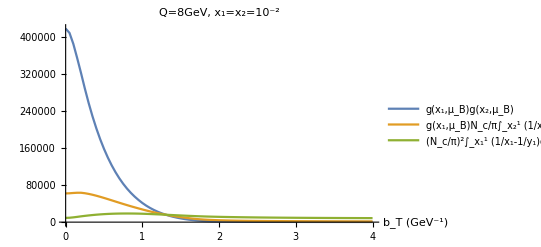

```mathematica
{ListPlot[{ffmubbt,fhmubbt,hhmubbt},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True],ListPlot[{ffmubbt3,fhmubbt3,hhmubbt3},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]}
```

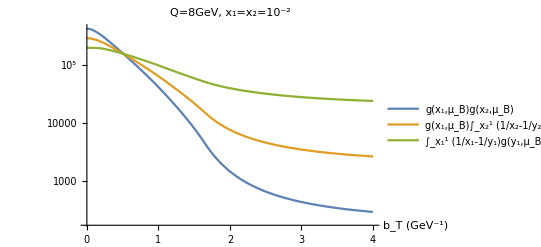
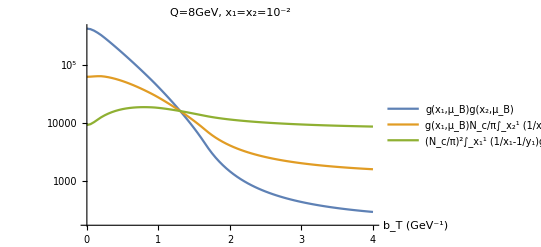

```mathematica
{ListLogPlot[{ffmubbt,fhmubbt,hhmubbt},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True],ListLogPlot[{ffmubbt3,fhmubbt3,hhmubbt3},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)","g(x_1,μ_B)N_c/π∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2","(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]}
```

C[w_0 h_1^(⊥g) h_1^(⊥g)], which only difference with C[f_1^g f_1^g] is the replacement of f_1^gas a PDF by h_1^(⊥g) as α_s x splitting function twice, suffers a maximal suppression from the two effects : normalisation suppression by the α_s^2 factor and double b_T-broadening that makes it quickly fall with increasing q_T.
Because J_2 and J_4reduce the number of oscillations present within the same b_T-range as compared to J_0, they actually counter the suppression effect associated with b_T-broadening. A peak in q_Twill appear for the associated convolutions. Example: in the case of the integrand containing J_4 for q_T=1GeV, the first oscillation is dilated to the large b_T to a point where it will not have time to grow enough before being suppressed by the Sudakov factors. The convolution will thus be small in the small q_T-region. It will increase with q_T as the oscillatory integrand contracts in frequency, reaching a peak value, before the oscillation balance effect cancels the integrand again as q_T increases too much: then the number of oscillations inside the relevant b_T region becomes too large and they can balance, canceling the integral.

```mathematica
Chhint2[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint2[x_,Q_,qt_,bt_]:=bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)NIntegrate[gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1}];
```

```mathematica
Cw4hhint2[x_,Q_,qt_,bt_]:=bt BesselJ[4,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Chh2qt1=Transpose[{Range[0,4,0.05],ParallelMap[Chhint2[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Chhint2[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh2qt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint2[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint2[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint2[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw3fh2qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint2[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

```mathematica
Cw4hh2qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint2[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint2[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh2qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint2[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cffint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp] gMSTW[x,μbfrozen[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[2,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)gMSTW[x,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhint2ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[4,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cff2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cff2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193446}. NIntegrate obtained 4233.94 and 0.00531448 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 4222.35 and 0.0223447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 4271.17 and 0.0147148 for the integral and error estimates.

```mathematica
Cff2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195075}. NIntegrate obtained 821.71 and 0.00218401 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192928}. NIntegrate obtained 802.849 and 0.00148318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193325}. NIntegrate obtained 831.392 and 0.00122327 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197282}. NIntegrate obtained 795.405 and 0.00458745 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.194984}. NIntegrate obtained 793.401 and 0.00134526 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 787.267 and 0.00675876 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193446}. NIntegrate obtained 809.983 and 0.00219075 for the integral and error estimates.

```mathematica
Chh2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10421.4 and 0.0198152 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17657.2 and 0.0588621 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4971.31 and 0.00735741 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15213.5 and 0.0392786 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7655.1 and 0.0120401 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 220.576 and 0.000243191 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19008.1 and 0.0482943 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19277.7 and 0.063714 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2693.86 and 0.0086289 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18682.1 and 0.0545946 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16962.5 and 0.0396862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18231.1 and 0.0454679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13001.1 and 0.0249376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19207.1 and 0.0627746 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19219.5 and 0.0642867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16148.2 and 0.0727641 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11747.8 and 0.0212787 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6281.35 and 0.0090324 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9047.27 and 0.0155871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19032.6 and 0.0625336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3763.73 and 0.00510366 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14161.1 and 0.0318761 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17718.8 and 0.0838497 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18718.5 and 0.0552566 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16252.3 and 0.0728608 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17041.3 and 0.183201 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18279.4 and 0.0624373 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15358.7 and 0.0900235 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14368.4 and 0.0693358 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13290. and 0.130446 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12133.6 and 0.0869548 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8306.39 and 0.12738 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9629.85 and 0.0982965 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6952.18 and 0.167365 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10909.6 and 0.0898184 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5580.59 and 0.10839 for the integral and error estimates.

```mathematica
Chh2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 801.53 and 0.00968838 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 182.369 and 0.000197857 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1038.68 and 0.00413281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -918.763 and 0.00239508 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 438.194 and 0.0132676 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -44.7673 and 0.0055874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -979.377 and 0.0249307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -727.166 and 0.0296915 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.23343 and 0.000965952 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -594.84 and 0.0187201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -931.438 and 0.0208378 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -265.506 and 0.0342147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 243.894 and 0.0350401 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 623.603 and 0.0344937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 741.304 and 0.033369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -625.016 and 0.00512454 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 326.184 and 0.000407107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 775.572 and 0.00932709 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -80.1967 and 0.0209801 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1142.64 and 0.00251455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 494.309 and 0.00806993 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -478.451 and 0.00170866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 555.432 and 0.0363707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 129.839 and 0.0384187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -816.748 and 0.0592661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -387.796 and 0.0440615 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1005.92 and 0.0506678 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -886.765 and 0.0490625 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -498.075 and 0.057862 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.5206 and 0.065541 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 504.247 and 0.0712688 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 718.87 and 0.102132 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 373.773 and 0.715063 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -151.154 and 0.139357 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -673.6 and 0.154224 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 766.665 and 0.0827491 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1009.76 and 0.162064 for the integral and error estimates.

```mathematica
Chh2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 123.674 and 0.000271646 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -94.2279 and 0.000375583 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 329.075 and 0.00251874 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -326.016 and 0.000757186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 65.3974 and 0.00450822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -488.069 and 0.00567304 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 236.451 and 0.00757141 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -114.123 and 0.041791 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -275.751 and 0.0214827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 258.425 and 0.027731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 368.933 and 0.0232594 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -405.959 and 0.0385161 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 190.479 and 0.0849199 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.638 and 0.0210184 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -348.931 and 0.0469087 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -440.735 and 0.0126483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -323.303 and 0.000527921 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -359.944 and 0.00627723 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -26.8755 and 0.0102278 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 390.949 and 0.00234935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -198.93 and 0.0101722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 417.65 and 0.00820403 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.1092 and 0.0606005 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 331.172 and 0.0596424 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 328.515 and 0.0603025 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.65265 and 0.0694517 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -222.002 and 0.0115772 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -359.244 and 0.0696995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -412.14 and 0.0684082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 272.797 and 0.0877992 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -109.46 and 0.0778141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 382.047 and 0.101767 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.033 and 0.0986193 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -453.578 and 0.101488 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -287.926 and 0.0963378 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -226.555 and 0.108664 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 188.206 and 0.119208 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 409.28 and 0.109024 for the integral and error estimates.

```mathematica
Cw3fh2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh2qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint2ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 50.6438 and 0.0000770047 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000329385 and 3.19155×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 185.104 and 0.000203056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 138.879 and 0.000292321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7023.25 and 0.00713599 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7892.71 and 0.00877672 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8831.5 and 0.0100254 for the integral and error estimates.

```mathematica
Cw4hh2qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint2ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3311.61 and 0.00387817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.404726 and 1.32218×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1231.76 and 0.0183069 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1214.07 and 0.0131987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1999.19 and 0.0152615 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3092.04 and 0.00691051 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2023.33 and 0.0257261 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1533.96 and 0.0188714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2545.87 and 0.0258626 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3073.05 and 0.02479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2937.07 and 0.0265818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 592.533 and 0.00545525 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2910.45 and 0.0281536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3360.23 and 0.00421394 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2588.82 and 0.0104636 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1494.09 and 0.0154872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2501.57 and 0.0308007 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1513.86 and 0.0480803 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1260.04 and 0.048613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1979.03 and 0.0324557 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1632.16 and 0.0521172 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1303.44 and 0.0471177 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2138.94 and 0.0591352 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2655.42 and 0.0564059 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3007.69 and 0.0650263 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2830.65 and 0.0794995 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3074.83 and 0.0718194 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2354.19 and 0.10344 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1368.3 and 0.142666 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1804.6 and 0.122635 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1195.8 and 0.141189 for the integral and error estimates.

```mathematica
Cw4hh2qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint2ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.83044 and 9.0648×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 309.821 and 0.00490033 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1053.98 and 0.0293661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 358.154 and 0.00298636 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 422.367 and 0.038174 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 545.248 and 0.0221463 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1092.65 and 0.00578549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 657.953 and 0.00909023 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 230.949 and 0.0362986 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.835 and 0.0418488 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 929.212 and 0.0214773 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 239.427 and 0.0114086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 409.51 and 0.0468679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.18 and 0.00161161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 757.214 and 0.00756067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 126.408 and 0.00348856 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 798.263 and 0.0681701 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1039.32 and 0.007711 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1048. and 0.0562325 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 554.246 and 0.0742974 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 286.251 and 0.0115636 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 932.668 and 0.0518223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 663.911 and 0.0856122 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 304.52 and 0.0667469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 253.681 and 0.181739 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1007.79 and 0.0753823 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 690.738 and 0.0938711 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1022.47 and 0.0888559 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 311.504 and 0.0953407 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 526.678 and 0.113806 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 230.978 and 0.0969458 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 932.696 and 0.108338 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1078.39 and 0.115884 for the integral and error estimates.

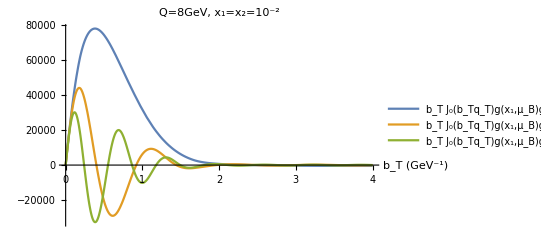

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->1,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2"]
```

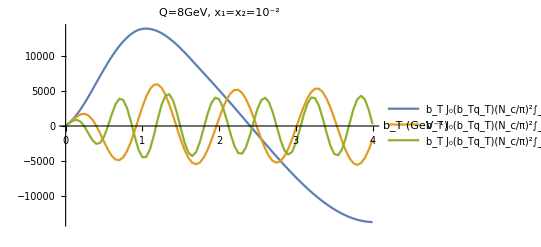

```mathematica
ListPlot[{Chh2qt1,Chh2qt6,Chh2qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

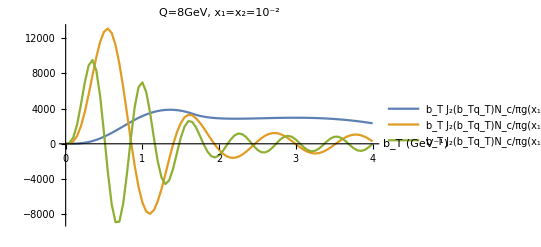

```mathematica
ListPlot[{Cw3fh2qt1,Cw3fh2qt6,Cw3fh2qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

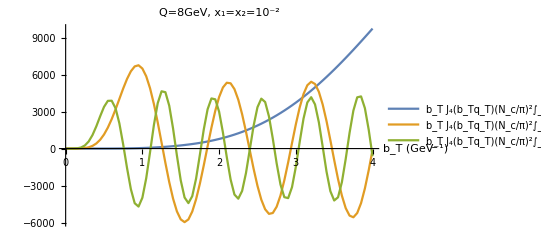

```mathematica
ListPlot[{Cw4hh2qt1,Cw4hh2qt6,Cw4hh2qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

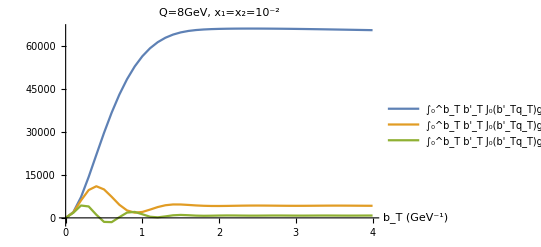

```mathematica
ListPlot[{Cff2qt1ev,Cff2qt6ev,Cff2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

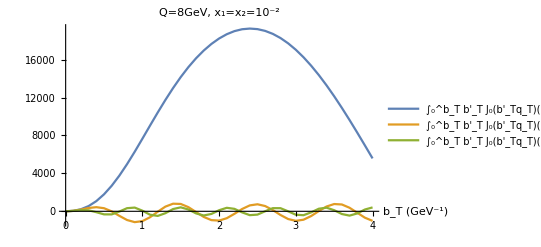

```mathematica
ListPlot[{Chh2qt1ev,Chh2qt6ev,Chh2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

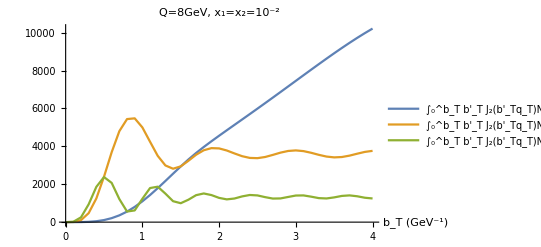

```mathematica
ListPlot[{Cw3fh2qt1ev,Cw3fh2qt6ev,Cw3fh2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_2(b'_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

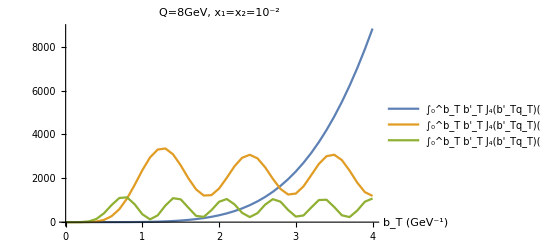

```mathematica
ListPlot[{Cw4hh2qt1ev,Cw4hh2qt6ev,Cw4hh2qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_4(b'_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

```mathematica
Chhint3[x_,Q_,qt_,bt_]:=bt BesselJ[0,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint3[x_,Q_,qt_,bt_]:=bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])NIntegrate[gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1}];
```

```mathematica
Cw4hhint3[x_,Q_,qt_,bt_]:=bt BesselJ[4,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Chh3qt1=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh3qt6=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh3qt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fh3qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fh3qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh3qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,8,1,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh3qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,8,6,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh3qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,8,10,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cffint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp] ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])gMSTW[x,μbfrozen[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[0,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])(1/x-1/y1)gMSTW[y1,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[2,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])gMSTW[x,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhint3ev[x_,Q_,qt_,bt_]:=NIntegrate[btp BesselJ[4,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])(1/x-1/y1)gMSTW[y1,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cff3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cff3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 7384.56 and 0.0276218 for the integral and error estimates.

```mathematica
Cff3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193725}. NIntegrate obtained 419.52 and 0.000730964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193331}. NIntegrate obtained 373.664 and 0.00041446 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195281}. NIntegrate obtained 390.233 and 0.000417748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192741}. NIntegrate obtained 395.836 and 0.000926144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193325}. NIntegrate obtained 394.047 and 0.00206942 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193128}. NIntegrate obtained 388.777 and 0.000709304 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.19215}. NIntegrate obtained 385.228 and 0.000408673 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195274}. NIntegrate obtained 385.774 and 0.00050228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192928}. NIntegrate obtained 388.989 and 0.00171945 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195075}. NIntegrate obtained 391.658 and 0.00234191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192949}. NIntegrate obtained 287.447 and 0.000498846 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193336}. NIntegrate obtained 446.362 and 0.000475365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192552}. NIntegrate obtained 385.956 and 0.000735214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193313}. NIntegrate obtained 387.247 and 0.000876958 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.194984}. NIntegrate obtained 388.056 and 0.00193545 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197282}. NIntegrate obtained 388.265 and 0.00430359 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193446}. NIntegrate obtained 389.852 and 0.00319247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 390.675 and 0.0141209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192894}. NIntegrate obtained 390.469 and 0.000420122 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197192}. NIntegrate obtained 389.792 and 0.00103113 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 387.367 and 0.00815916 for the integral and error estimates.

```mathematica
Chh3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4710.11 and 0.00941189 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9391.4 and 0.0409947 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7372.82 and 0.0190772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8842.27 and 0.0279102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9686.63 and 0.0376583 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9585.7 and 0.0330183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6201.01 and 0.010181 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9642.4 and 0.0288726 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3003.96 and 0.00375226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8236.11 and 0.0187161 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9502.97 and 0.0272921 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 279.275 and 0.000334489 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9247.46 and 0.0251548 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9675.39 and 0.0348695 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9677.85 and 0.0332911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5491.81 and 0.00915495 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7840.12 and 0.0164584 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9066.51 and 0.0338563 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9650.6 and 0.0311274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9471.89 and 0.0538655 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3871.64 and 0.00592755 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8567.76 and 0.0218052 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6828.01 and 0.0135399 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9606.34 and 0.0292489 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9284.96 and 0.0512975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9546.3 and 0.0340571 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9174.95 and 0.0467318 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9384.36 and 0.0356896 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9055.62 and 0.0322771 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8928.27 and 0.0528702 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8511.26 and 0.0493634 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8794.2 and 0.0361485 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8654.75 and 0.0411298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8365.09 and 0.061113 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8217.61 and 0.0776662 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8070.21 and 0.0442646 for the integral and error estimates.

```mathematica
Chh3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -644.363 and 0.00470545 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 229.343 and 0.000282855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 58.5541 and 0.00632212 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 130.189 and 0.00119521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -560.096 and 0.00233802 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -229.618 and 0.00413693 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -35.5148 and 0.00834433 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -307.628 and 0.0143335 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -227.56 and 0.0157253 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -353.597 and 0.0121334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -343.977 and 0.0104781 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -274.01 and 0.0372873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -143.288 and 0.0125889 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -83.124 and 0.0126219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -65.109 and 0.0125841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 443.091 and 0.000998911 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -459.339 and 0.00449097 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -252.816 and 0.00223083 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -159.621 and 0.0110269 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 51.9254 and 0.00659938 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -695.957 and 0.00275548 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -39.2933 and 0.00540529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -279.973 and 0.0219796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -92.1494 and 0.0138194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -222.957 and 0.0137099 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -152.167 and 0.0351155 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -304.502 and 0.0160027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -289.564 and 0.0137906 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -241.753 and 0.0199661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -178.546 and 0.0223245 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -122.092 and 0.0236587 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -97.0129 and 0.0286809 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -135.662 and 0.132147 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -91.6189 and 0.0270575 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -193.636 and 0.0547396 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -250.541 and 0.0399531 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -286.701 and 0.0400118 for the integral and error estimates.

```mathematica
Chh3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -116.936 and 0.000569661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 152.795 and 0.00021795 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -376.03 and 0.00134833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -13.0293 and 0.00456882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -97.2672 and 0.0166264 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -257.716 and 0.00510236 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.238 and 0.00229898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -63.8385 and 0.00952498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -19.3685 and 0.00517844 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -139.402 and 0.0113114 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -173.133 and 0.00644582 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -25.2195 and 0.00533097 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -143.563 and 0.0148492 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -35.7273 and 0.0114225 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -16.8168 and 0.00892834 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -135.102 and 0.0165016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -369.574 and 0.00076606 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 126.184 and 0.000193907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -135.424 and 0.00179848 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -205.169 and 0.00465769 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -157.035 and 0.00748431 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 153.259 and 0.00257366 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -83.4205 and 0.120273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -37.3052 and 0.0192726 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.3157 and 0.00539509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -81.4392 and 0.0224668 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -124.099 and 0.00602456 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -37.5297 and 0.0197134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -127.569 and 0.0224337 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -51.0393 and 0.0270016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -134.337 and 0.0196044 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -97.1247 and 0.0804349 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -69.0808 and 0.0260386 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -38.0604 and 0.0250085 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -114.893 and 0.0263679 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -108.495 and 0.0335026 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -39.5249 and 0.0266763 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -133.521 and 0.029224 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -63.3261 and 0.0353595 for the integral and error estimates.

```mathematica
Cw3fh3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh3qt1ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint3ev[10^-2,8,1,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 20.0408 and 0.0000311614 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 78.5863 and 0.000112939 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 53.0325 and 0.0000562761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000435428 and 1.26157×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 156.063 and 0.000180315 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 94.3155 and 0.0000973989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 182.32 and 0.000185827 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.4028 and 0.0000268953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 42.7838 and 0.000111816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 244.907 and 0.000253169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 368.024 and 0.000372181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 322.725 and 0.000330186 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 472.726 and 0.000642646 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 597.885 and 0.000674897 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 668.701 and 0.000690549 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 745.267 and 0.000795369 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 827.748 and 0.000844994 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1111.84 and 0.00139758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1010.95 and 0.00127868 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 916.277 and 0.000946885 for the integral and error estimates.

```mathematica
Cw4hh3qt6ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint3ev[10^-2,8,6,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1993.62 and 0.00248161 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1447.01 and 0.00535604 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1508.76 and 0.00853453 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1630.88 and 0.00472886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.534879 and 1.55778×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1450.32 and 0.00721888 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1587.96 and 0.00169935 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1598.3 and 0.00974506 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1927.95 and 0.00342273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1753.91 and 0.00832133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1689.08 and 0.00906755 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1775.58 and 0.00849044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1751.04 and 0.00977411 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1509.55 and 0.00671413 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2011.84 and 0.00258724 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1784.57 and 0.00540632 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1691.36 and 0.0107298 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1617.6 and 0.00913141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1525.66 and 0.0141937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1553.93 and 0.0134773 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1520.14 and 0.0149219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1567.03 and 0.0162836 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1691.66 and 0.0137122 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1629.41 and 0.0147926 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1733.32 and 0.0164339 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1599.28 and 0.0319091 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1741.16 and 0.0186921 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1713.38 and 0.0196205 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1659.98 and 0.0236024 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1551.74 and 0.0335671 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1533.17 and 0.0343682 for the integral and error estimates.

```mathematica
Cw4hh3qt10ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhint3ev[10^-2,8,10,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1107.23 and 0.00135192 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.73872 and 0.0000108607 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 753.547 and 0.0124565 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 836.614 and 0.00956068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.292 and 0.00562987 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 648.613 and 0.00321086 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 761.944 and 0.0103829 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 683.784 and 0.0025153 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 859.788 and 0.00999067 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 818.14 and 0.0112488 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 698.932 and 0.0049449 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 912.602 and 0.00346328 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 723.084 and 0.0117651 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 750.012 and 0.0170938 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 806.816 and 0.0197651 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 918.523 and 0.0014136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 842.194 and 0.0177571 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 805.857 and 0.0049018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 709.875 and 0.00509219 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 577.554 and 0.00255727 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 787.939 and 0.0259171 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 898.341 and 0.00432649 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 826.554 and 0.0174354 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 776.338 and 0.0216297 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 737.42 and 0.0181272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 743.729 and 0.0186098 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 829.424 and 0.0191485 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 792.814 and 0.0228695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 831.235 and 0.0208193 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 749.577 and 0.023612 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 740.489 and 0.022841 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 817.336 and 0.0279724 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 773.109 and 0.0316399 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 833.039 and 0.0280948 for the integral and error estimates.

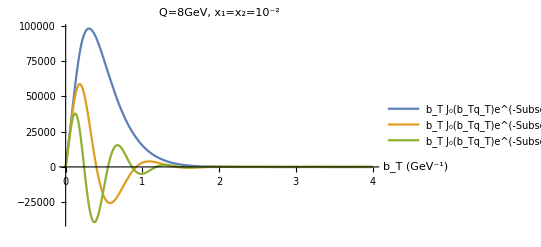

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->1,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2"]
```

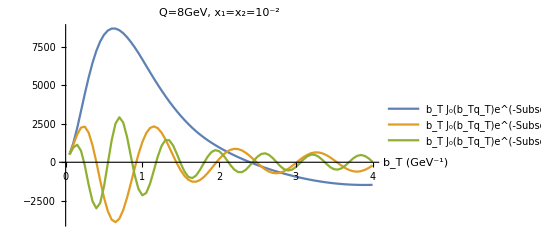

```mathematica
ListPlot[{Chh3qt1,Chh3qt6,Chh3qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

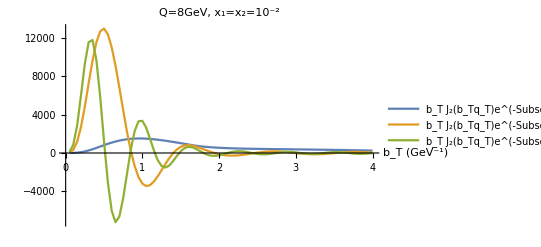

```mathematica
ListPlot[{Cw3fh3qt1,Cw3fh3qt6,Cw3fh3qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

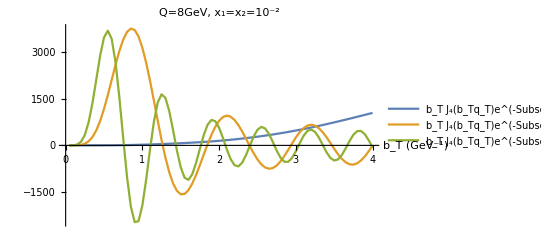

```mathematica
ListPlot[{Cw4hh3qt1,Cw4hh3qt6,Cw4hh3qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

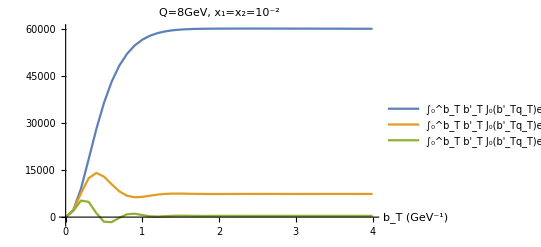

```mathematica
ListPlot[{Cff3qt1ev,Cff3qt6ev,Cff3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

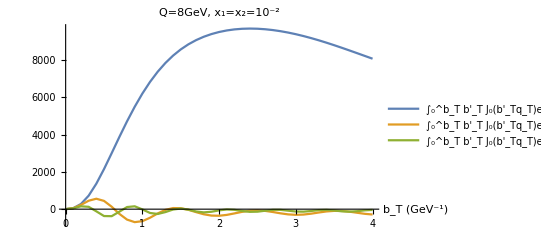

```mathematica
ListPlot[{Chh3qt1ev,Chh3qt6ev,Chh3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

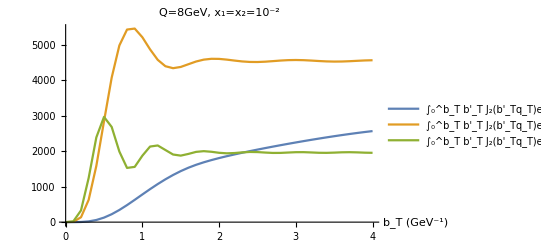

```mathematica
ListPlot[{Cw3fh3qt1ev,Cw3fh3qt6ev,Cw3fh3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

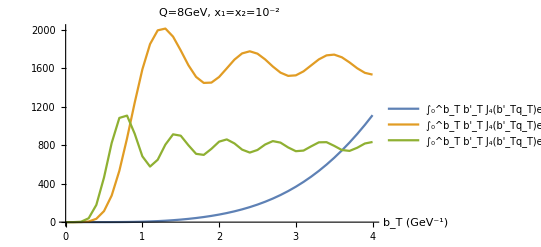

```mathematica
ListPlot[{Cw4hh3qt1ev,Cw4hh3qt6ev,Cw4hh3qt10ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2",Joined->True]
```

```mathematica
Chh4qt1=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,30,1,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,30,6,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh4qt10=Transpose[{Range[0,4,0.05],ParallelMap[Chhint3[10^-2,30,10,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh4qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,30,1,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fh4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,30,6,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fh4qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint3[10^-2,30,10,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh4qt1=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,30,1,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,30,6,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh4qt10=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint3[10^-2,30,10,#] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

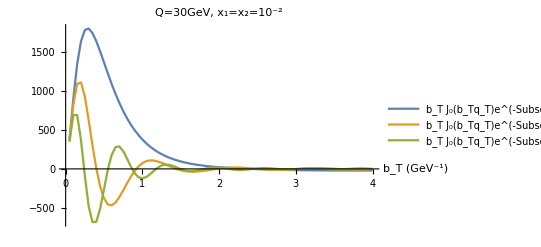

```mathematica
ListPlot[{Chh4qt1,Chh4qt6,Chh4qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

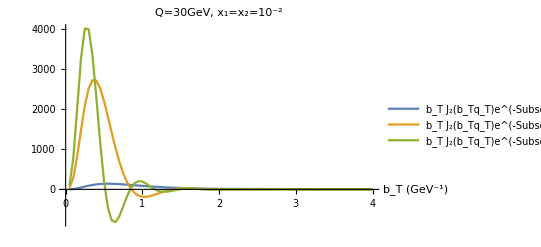

```mathematica
ListPlot[{Cw3fh4qt1,Cw3fh4qt6,Cw3fh4qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

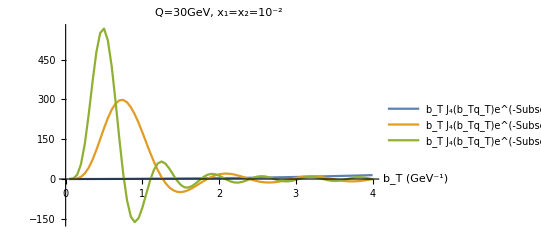

```mathematica
ListPlot[{Cw4hh4qt1,Cw4hh4qt6,Cw4hh4qt10},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=30GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

It is a little harder to compare the actions of the different elements in the integrand on the integral as the latter is not stable when any of the Sudakov factors are removed. One can only compute the convolutions with all the elements together.

```mathematica
ChhintNoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[0,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw3fhintNoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw4hhintNoS[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[4,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
ChhintNoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[0,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw3fhintNoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw4hhintNoSnp[x_?NumericQ,Q_?NumericQ,qt_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[4,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Chhinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[0,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw3fhinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1},{bt,0,∞}];
```

```mathematica
Cw4hhinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt BesselJ[4,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1},{bt,0,∞}];
```

```mathematica
qtvalsQ8=Range[0,4,0.1];
qtvalsQ30=Range[0,15,0.1];
```

```mathematica
Chhbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Chhinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2481.7 and 0.00924814 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3181.73 and 0.0138353 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4623.35 and 0.066478 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3042.28 and 0.0123065 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3454.94 and 0.0132277 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3957.42 and 0.0137862 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2901.88 and 0.0112526 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3715.54 and 0.012538 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4714.27 and 0.0154508 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2620.96 and 0.00969411 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2761.23 and 0.0102472 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4361.18 and 0.0660603 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4512.2 and 0.0150835 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0144067 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4691.37 and 0.0154617 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2344. and 0.00771273 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2208.39 and 0.00704798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4572.99 and 0.0152423 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3319.53 and 0.0135624 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3839.2 and 0.0132627 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3587.19 and 0.0131612 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4272. and 0.0143425 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4708.54 and 0.066617 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4441.43 and 0.0152226 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4069.45 and 0.0143021 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1945.32 and 0.00687976 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2075.36 and 0.00678825 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1576.74 and 0.00671136 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4662.9 and 0.0664945 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1695.7 and 0.00680573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1818.66 and 0.00640551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1462.01 and 0.0067984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1351.7 and 0.0063595 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1245.95 and 0.00635226 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1144.88 and 0.00627566 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1048.55 and 0.00596721 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 788.195 and 0.0053151 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 956.998 and 0.00551409 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 870.223 and 0.00550102 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 710.859 and 0.00497477 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 638.134 and 0.00491366 for the integral and error estimates.

```mathematica
Chhbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Chhinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 607.877 and 0.00336196 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.324 and 0.00086548 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 693.556 and 0.00271939 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 551.917 and 0.00263353 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 725.311 and 0.00271295 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 491.726 and 0.00213707 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 656.19 and 0.00276079 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 717.211 and 0.00268213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 430.472 and 0.00168513 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 314.735 and 0.00136711 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 263.568 and 0.00125004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 370.809 and 0.00144761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 178.266 and 0.00095144 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 218.011 and 0.000997131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 91.1942 and 0.00100867 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 144.171 and 0.000921388 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 597.187 and 0.00326818 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.139 and 0.000875611 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 687.103 and 0.00270345 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 540.11 and 0.0023835 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 479.466 and 0.00206974 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 724.985 and 0.00270867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 647.303 and 0.00281109 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 713.681 and 0.00280638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 418.338 and 0.00164142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 253.995 and 0.00126257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 359.255 and 0.00150388 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 304.078 and 0.0012833 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 209.597 and 0.000989498 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 171.005 and 0.000894774 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 86.8831 and 0.00108061 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 137.997 and 0.000891415 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 586.218 and 0.00305758 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 680.117 and 0.00266967 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 105.139 and 0.000932215 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 528.162 and 0.00232561 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 724.008 and 0.00272634 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 467.189 and 0.00191948 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 638.002 and 0.00300709 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 709.537 and 0.00279464 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 244.651 and 0.00144673 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 406.289 and 0.00164863 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 347.86 and 0.00147515 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 293.627 and 0.00123472 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 201.417 and 0.000950439 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 163.968 and 0.000896278 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 82.7324 and 0.00108041 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.03 and 0.000884125 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 71.1971 and 0.00113492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 54.7533 and 0.000951334 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 41.3204 and 0.000864454 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 30.4109 and 0.000723094 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 21.5986 and 0.000695347 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.85989 and 0.000874843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14.5179 and 0.000702372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.36593 and 0.000917774 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.925449 and 0.000978411 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.46313 and 0.00080726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.87904 and 0.00094081 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.46525 and 0.000934492 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 67.6421 and 0.00118329 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.74162 and 0.000932466 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 51.8423 and 0.00195268 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.75704 and 0.000585513 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.55295 and 0.000593497 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.9512 and 0.000807613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.16444 and 0.000581562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 28.4932 and 0.000715101 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 20.0546 and 0.000684639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.87544 and 0.000890577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.5872 and 0.000887435 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.45181 and 0.000969075 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13.2814 and 0.000711595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 64.2247 and 0.00105114 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.821095 and 0.00084654 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.81133 and 0.00129205 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.30763 and 0.000954314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 49.0475 and 0.000859767 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.01801 and 0.00492322 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 36.6791 and 0.000749384 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.97512 and 0.000611975 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.72188 and 0.000599236 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 26.6561 and 0.000697735 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.29207 and 0.000573755 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.93556 and 0.000883065 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.8448 and 0.000837997 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 18.577 and 0.000667886 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.95214 and 0.000967703 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.0995 and 0.000776926 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.13891 and 0.000982601 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.209808 and 0.000900008 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.71426 and 0.000980285 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.27918 and 0.000592257 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.1801 and 0.000598224 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.87978 and 0.000599542 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.41047 and 0.000572868 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
Chhbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Chhinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8704.77 and 0.0336758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9737.16 and 0.0361516 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3438.83 and 0.0231381 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9258.2 and 0.0339592 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8005.05 and 0.0302239 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2864.41 and 0.0252536 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9614.22 and 0.0376159 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7216.07 and 0.0269662 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3142.69 and 0.0234747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5575.87 and 0.0240595 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4085.01 and 0.0214499 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3752.97 and 0.0216182 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2603.64 and 0.0208514 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2359.88 and 0.0194478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6391.61 and 0.0239539 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4800.51 and 0.020421 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8369.65 and 0.0313164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7618.19 and 0.0300473 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9706.22 and 0.0360459 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9003.22 and 0.032627 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2132.58 and 0.0188216 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9463.58 and 0.0361618 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6805.24 and 0.0260901 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1724.72 and 0.0200749 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1921.08 and 0.0190934 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5980.37 and 0.0241206 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5181.66 and 0.0221974 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1219.53 and 0.0188928 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4434.49 and 0.0212661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1542.8 and 0.0191893 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1374.64 and 0.0188395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1076.79 and 0.0184955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 945.726 and 0.0172398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 825.675 and 0.0168833 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 525.081 and 0.0159277 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 300.855 and 0.0153693 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 240.378 and 0.015654 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 715.977 and 0.0165235 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 442.647 and 0.0159743 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 615.988 and 0.0166335 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 368.095 and 0.0147696 for the integral and error estimates.

```mathematica
Chhbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Chhinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1077.69 and 0.00448346 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1053.86 and 0.00436241 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 987.461 and 0.0038386 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 891.229 and 0.00348387 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 780.04 and 0.00292402 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 666.397 and 0.00303633 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 558.705 and 0.00280116 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 461.606 and 0.00377933 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 377.011 and 0.00267614 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 305.069 and 0.00246749 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 244.915 and 0.00189695 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 195.205 and 0.0016637 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 154.458 and 0.00154984 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 121.254 and 0.00165543 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 94.3179 and 0.00149441 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 72.5463 and 0.00161702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1076.72 and 0.0044045 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1043.66 and 0.0042806 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 970.12 and 0.00382086 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 869.734 and 0.00335453 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 757.178 and 0.00290678 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 644.186 and 0.00270785 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 538.344 and 0.00310856 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 443.662 and 0.00356529 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 361.628 and 0.00254992 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 292.134 and 0.00238791 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 234.184 and 0.00189035 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 186.385 and 0.0016626 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 147.257 and 0.00353678 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.403 and 0.00172583 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 89.5826 and 0.00157732 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 68.7266 and 0.00164622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1073.81 and 0.00441644 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1031.81 and 0.00427919 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 951.702 and 0.00371644 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 847.763 and 0.00315891 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 734.313 and 0.00297115 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 622.272 and 0.00270781 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 518.437 and 0.00364476 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 426.229 and 0.00351935 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 346.748 and 0.00243012 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 279.662 and 0.0023279 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 223.86 and 0.00189231 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 177.913 and 0.00166428 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 140.347 and 0.00354388 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 109.793 and 0.00158081 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 85.0455 and 0.00165042 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 65.0689 and 0.00164037 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 55.0037 and 0.00177006 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 40.9072 and 0.0016748 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 29.6093 and 0.00153589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13.3926 and 0.00135656 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 20.5807 and 0.00122862 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.91202 and 0.00162281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.50986 and 0.00132592 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.21588 and 0.00138591 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.75874 and 0.00154786 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.69827 and 0.00126486 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.81997 and 0.00167371 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.285554 and 0.00127025 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.31098 and 0.0013947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.52312 and 0.00102348 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.05507 and 0.00106851 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.44345 and 0.000956024 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 51.9314 and 0.00183686 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.4423 and 0.0016586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 27.6371 and 0.00146032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.008 and 0.00130744 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.1441 and 0.0013997 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.16028 and 0.00160242 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.44376 and 0.00140233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.07245 and 0.00419076 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.9969 and 0.00128723 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.71289 and 0.00125106 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.885585 and 0.0014461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 48.9908 and 0.00175132 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.70357 and 0.00136421 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.0135 and 0.00105274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 36.0844 and 0.00165476 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.671 and 0.00106333 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.7516 and 0.0013638 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 17.5057 and 0.00125989 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.16465 and 0.00102431 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.5209 and 0.000931581 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10.9527 and 0.00117447 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.39373 and 0.00147384 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.70909 and 0.00137927 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.3689 and 0.00155911 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.77384 and 0.00127161 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.45546 and 0.00138861 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.45867 and 0.00133044 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.0751 and 0.0013581 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.19487 and 0.00105673 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.80865 and 0.0010925 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.26569 and 0.0010186 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.59114 and 0.000946014 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
ChhNoSnpQ8=Transpose[{qtvalsQ8,ParallelMap[ChhintNoSnp[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 4.81674×10^23 and 4.66912×10^23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.5252×10^6}. NIntegrate obtained -195896. and 129958. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 7.80155×10^6 and 1.0645×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.16711×10^6}. NIntegrate obtained 68593. and 112441. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 6.88467×10^7 and 3.30298×10^7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained 5.19363×10^7 and 1.8033×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.67772×10^7}. NIntegrate obtained 1.43851×10^6 and 617276. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04858×10^6}. NIntegrate obtained -5500.93 and 1.8754×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 2.59097×10^6 and 364934. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained -272759. and 373802. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.89039×10^6}. NIntegrate obtained -1.14612×10^6 and 663164. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -899845. and 2.61705×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained -1.05247×10^6 and 298407. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.11848×10^6}. NIntegrate obtained 246811. and 379723. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -173771. and 567473. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -432543. and 885556. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.8557×10^6}. NIntegrate obtained -62941.8 and 113371. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.19566×10^6}. NIntegrate obtained -36264.5 and 155390. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.11848×10^7}. NIntegrate obtained 684389. and 420682. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained 813269. and 2.645×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,8.94785×10^6}. NIntegrate obtained 201833. and 239442. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 28 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.81375×10^6}. NIntegrate obtained -127777. and 63926.3 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 421371. and 485619. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04045×10^6}. NIntegrate obtained 635668. and 591481. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 2.63856×10^6 and 1.49468×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.36871×10^6}. NIntegrate obtained 229723. and 99341.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -601109. and 803714. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 524192. and 579252. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -1.95278×10^7 and 6.58327×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -929831. and 369973. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -274065. and 2.43589×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.04161×10^6 and 1.67227×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.23696×10^6}. NIntegrate obtained 34234.7 and 304908. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.59239×10^7 and 2.39987×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -275423. and 1.25843×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^6}. NIntegrate obtained 149303. and 95980.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,972591.}. NIntegrate obtained -50717.5 and 88171.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 379103. and 754909. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 872153. and 185260. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.45654×10^6}. NIntegrate obtained 62482.9 and 111186. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.23199×10^6 and 1.85804×10^6 for the integral and error estimates.

```mathematica
ChhNoSnpQ30=Transpose[{qtvalsQ30,ParallelMap[ChhintNoSnp[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.47178×10^21 and 5.30409×10^21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1419.78 and 6462.09 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.23696×10^7}. NIntegrate obtained 612.322 and 698.838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2554.85 and 1417.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained 591232. and 204827. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,9.58698×10^6}. NIntegrate obtained -730.866 and 787.144 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.31586×10^6}. NIntegrate obtained 143.952 and 184.868 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1660.27 and 2116.62 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 783337. and 375162. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.19566×10^6}. NIntegrate obtained 263.402 and 1776.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.8557×10^6}. NIntegrate obtained -183.139 and 1296.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.36871×10^6}. NIntegrate obtained 3055.78 and 1135.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained -4586.95 and 1617.27 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5398.49 and 2556.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 2272.22 and 1605.06 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1924.51 and 1236.83 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.3296×10^6}. NIntegrate obtained 386.76 and 351.512 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -220648. and 74853.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04045×10^6}. NIntegrate obtained 8301.37 and 6794.29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 12773.6 and 18998.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5297.86 and 5523.85 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2162.54 and 2194.32 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,986894.}. NIntegrate obtained 568.527 and 232.158 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 89784.1 and 120919. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.11848×10^7}. NIntegrate obtained 8687.83 and 4781.11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.23696×10^6}. NIntegrate obtained 1188.58 and 3492.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -6180.14 and 9129.32 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,972591.}. NIntegrate obtained -142.545 and 1008.84 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.45654×10^6}. NIntegrate obtained 1075.62 and 1266.87 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.98262×10^6}. NIntegrate obtained -758.781 and 618.903 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.00325×10^6}. NIntegrate obtained 665.216 and 368.242 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.97103×10^6}. NIntegrate obtained -1189.2 and 499.676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.61708×10^6}. NIntegrate obtained 289.753 and 377.531 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3454.04 and 1861.04 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained 10382. and 30058.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 30858.2 and 16991.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.16711×10^6}. NIntegrate obtained 1548.47 and 1306.56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -10146.4 and 4201.36 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.0912×10^6}. NIntegrate obtained 1189.5 and 384.238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 4172.97 and 1582.78 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,8.94785×10^6}. NIntegrate obtained 1049.86 and 312.556 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 4929.95 and 8590.68 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.17735×10^6}. NIntegrate obtained -40.8943 and 336.07 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.06489×10^6}. NIntegrate obtained 1015.8 and 383.525 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -688.616 and 1222.58 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -12950.4 and 21108.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.5252×10^6}. NIntegrate obtained -1472.88 and 1511.24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2059.88 and 1408.12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained -72.9798 and 242.706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.22016×10^7}. NIntegrate obtained 892.693 and 336.508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 877.976 and 597.241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained -942.918 and 344.566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 2973.09 and 1534.15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2086.78 and 27710.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 185.386 and 1140.25 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1362.85 and 1156.77 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1118.23 and 1834.9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3109.35 and 3740.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1057.12 and 1126.57 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3750.49 and 2877.02 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.89516×10^6}. NIntegrate obtained 557.034 and 386.982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1163.06 and 427.875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained 266.513 and 289.372 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1162.46 and 898.277 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -988.588 and 1355.69 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.34218×10^7}. NIntegrate obtained 434.968 and 189.989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.16222×10^6}. NIntegrate obtained 160.564 and 190.342 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,994204.}. NIntegrate obtained -56.1522 and 104.778 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained -1516.54 and 641.411 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 2413.07 and 616.707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.22016×10^7}. NIntegrate obtained 328.654 and 172.158 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.49131×10^6}. NIntegrate obtained 320.92 and 198.589 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 352.751 and 419.273 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.94758×10^6}. NIntegrate obtained -219.274 and 178.48 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.34218×10^7}. NIntegrate obtained -829.192 and 230.194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.0672×10^6}. NIntegrate obtained -308.363 and 144.165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1353.07 and 636.673 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.05683×10^6}. NIntegrate obtained 279.497 and 96.672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 1015.36 and 624.926 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -282.705 and 849.996 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.06409×10^6}. NIntegrate obtained -323.334 and 184.241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 864.366 and 412.152 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 28 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.59783×10^6}. NIntegrate obtained 299.016 and 147.996 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.53204×10^6}. NIntegrate obtained -409.522 and 138.979 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.63172×10^6}. NIntegrate obtained -329.39 and 233.679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -968.662 and 769.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -522.824 and 422.27 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1594.82 and 473.887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.2736×10^6}. NIntegrate obtained 585.267 and 150.565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -762.477 and 671.587 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.48551×10^6}. NIntegrate obtained -328.582 and 182.286 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.9174×10^7}. NIntegrate obtained -77.9923 and 238.849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 552.678 and 624.475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.62751×10^6}. NIntegrate obtained -289.947 and 179.111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.72827×10^6}. NIntegrate obtained -226.383 and 108.917 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.44148×10^6}. NIntegrate obtained 192.9 and 100.129 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ChhNoSQ8=Transpose[{qtvalsQ8,ParallelMap[ChhintNoS[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64168164789825×10^690538901}. NIntegrate obtained 2.546767507654178`15.954589770191005*^45435514318 and 4.946351521173255`15.954589770191005*^45435514318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 9.61034×10^7 and 1.31309×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.67772×10^7}. NIntegrate obtained 1.76746×10^7 and 7.61412×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.11472×10^7 and 3.22766×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.19147×10^7 and 4.50366×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.16711×10^6}. NIntegrate obtained 808781. and 1.38626×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.5252×10^6}. NIntegrate obtained -2.45059×10^6 and 1.60125×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained -3.39322×10^6 and 4.60861×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,8.94785×10^6}. NIntegrate obtained 2.46431×10^6 and 2.95189×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained 6.40426×10^8 and 2.22392×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 8.49056×10^8 and 4.07424×10^8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04858×10^6}. NIntegrate obtained -218144. and 2.31367×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained 9.91168×10^6 and 3.2623×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.89039×10^6}. NIntegrate obtained -1.4246×10^7 and 8.18369×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.46207×10^6 and 3.0049×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.27865×10^7 and 2.0626×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.11848×10^7}. NIntegrate obtained 8.38415×10^6 and 5.1866×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.23696×10^6}. NIntegrate obtained 381915. and 3.76305×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.19952×10^8 and 2.95955×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.11848×10^6}. NIntegrate obtained 2.94366×10^6 and 4.69081×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04045×10^6}. NIntegrate obtained 7.74808×10^6 and 7.30383×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.47229×10^6 and 1.55193×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 3.24948×10^7 and 1.84356×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.19566×10^6}. NIntegrate obtained -470030. and 1.91517×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained -1.29975×10^7 and 3.68223×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -5.34955×10^6 and 1.09205×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.15562×10^6 and 6.99848×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -2.41017×10^8 and 8.12136×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.20377×10^6 and 5.98812×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 28 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.81375×10^6}. NIntegrate obtained -1.58404×10^6 and 788938. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -7.43532×10^6 and 9.91224×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 6.46122×10^6 and 7.14226×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.8557×10^6}. NIntegrate obtained -787498. and 1.3966×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.52851×10^7 and 2.29172×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -1.14733×10^7 and 4.56389×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 4.6582×10^6 and 9.31059×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.36871×10^6}. NIntegrate obtained 2.82761×10^6 and 1.22337×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^6}. NIntegrate obtained 1.83946×10^6 and 1.18144×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,972591.}. NIntegrate obtained -630562. and 1.08583×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.45654×10^6}. NIntegrate obtained 769029. and 1.37042×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 1.07549×10^7 and 2.28143×10^6 for the integral and error estimates.

```mathematica
ChhNoSQ30=Transpose[{qtvalsQ30,ParallelMap[ChhintNoS[10^-2,30,#]&,qtvalsQ30]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.845682,0.845682,1.64168164789825×10^690538901}. NIntegrate obtained 2.565722277019338`15.954589770191005*^45435514318 and 4.98787688659413`15.954589770191005*^45435514318 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.17321×10^6 and 7.05234×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.23696×10^7}. NIntegrate obtained 597814. and 763845. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained 6.4551×10^8 and 2.24102×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.95478×10^6 and 1.55051×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,9.58698×10^6}. NIntegrate obtained -922430. and 858600. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.31586×10^6}. NIntegrate obtained 62265.6 and 199242. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.74885×10^6 and 2.31545×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 8.55837×10^8 and 4.10602×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.19566×10^6}. NIntegrate obtained -473995. and 1.93862×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.8557×10^6}. NIntegrate obtained -793824. and 1.408×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.36871×10^6}. NIntegrate obtained 2.8501×10^6 and 1.23335×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained -5.27529×10^6 and 1.76322×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.70935×10^6 and 2.79533×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 2.33714×10^6 and 1.74937×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.99111×10^6 and 1.35101×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.3296×10^6}. NIntegrate obtained 358580. and 380240. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -2.4294×10^8 and 8.18977×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.04045×10^6}. NIntegrate obtained 7.81019×10^6 and 7.38885×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.28885×10^7 and 2.07896×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -7.49459×10^6 and 9.98966×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 5.24525×10^6 and 6.03606×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,972591.}. NIntegrate obtained -635609. and 1.09753×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.45654×10^6}. NIntegrate obtained 774786. and 1.38497×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.47777×10^6 and 2.3993×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,986894.}. NIntegrate obtained 531974. and 252197. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 9.68705×10^7 and 1.32338×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.11848×10^7}. NIntegrate obtained 8.45089×10^6 and 5.22848×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.23696×10^6}. NIntegrate obtained 384564. and 3.80434×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained -1.1565×10^7 and 4.59883×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.0912×10^6}. NIntegrate obtained 916329. and 418952. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.98262×10^6}. NIntegrate obtained -1.15085×10^6 and 675524. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.00325×10^6}. NIntegrate obtained 484341. and 401277. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.97103×10^6}. NIntegrate obtained -1.4914×10^6 and 530941. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.61708×10^6}. NIntegrate obtained 173695. and 407689. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -808903. and 1.32944×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.35544×10^7}. NIntegrate obtained 9.99027×10^6 and 3.28878×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.5407×10^7 and 2.30983×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 3.2754×10^7 and 1.85831×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.16711×10^6}. NIntegrate obtained 815001. and 1.39955×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.17735×10^6}. NIntegrate obtained -413851. and 359358. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 4.33464×10^6 and 1.73169×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.69499×10^6 and 2.03517×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,8.94785×10^6}. NIntegrate obtained 1.10905×10^6 and 340487. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -3.48985×10^6 and 3.02884×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 4.69527×10^6 and 9.39759×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -2.28303×10^6 and 1.54087×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,2.06489×10^6}. NIntegrate obtained 805018. and 416719. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.92255×10^6 and 3.14508×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained -1.0833×10^6 and 375035. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.5252×10^6}. NIntegrate obtained -2.47058×10^6 and 1.61481×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.22016×10^7}. NIntegrate obtained 952148. and 364905. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.1943×10^6}. NIntegrate obtained -117308. and 264418. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.32091×10^6 and 978794. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.24851×10^6 and 2.00756×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.27126×10^6 and 467987. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 962839. and 652225. for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,6.71089×10^7}. NIntegrate obtained 3.21932×10^6 and 1.67304×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.49716×10^6 and 1.26388×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 184507. and 1.24399×10^6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.14464×10^6 and 1.23242×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.34218×10^7}. NIntegrate obtained 484311. and 205086. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 3.10939×10^6 and 4.08863×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.89516×10^6}. NIntegrate obtained 603331. and 421678. for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.34218×10^7}. NIntegrate obtained -908302. and 249034. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.49131×10^7}. NIntegrate obtained 294518. and 315184. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.22016×10^7}. NIntegrate obtained 363877. and 187943. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.09926×10^6 and 1.48121×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,994204.}. NIntegrate obtained -49614.6 and 112976. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,5.16222×10^6}. NIntegrate obtained 183184. and 205919. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained -1.67038×10^6 and 699608. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 396786. and 456388. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 2.63579×10^6 and 669220. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.47103×10^6 and 696256. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.94758×10^6}. NIntegrate obtained -233916. and 194271. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.49131×10^6}. NIntegrate obtained 335778. and 212920. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.05683×10^6}. NIntegrate obtained 315107. and 102882. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 957189. and 449507. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.48551×10^6}. NIntegrate obtained -359795. and 196409. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.0672×10^6}. NIntegrate obtained -334224. and 155796. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,2.63172×10^6}. NIntegrate obtained -356118. and 253700. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.47392×10^7}. NIntegrate obtained 1.11911×10^6 and 679193. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,7.06409×10^6}. NIntegrate obtained -344743. and 201122. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -302059. and 929359. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -824029. and 734212. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 28 recursive bisections in bt near {y1,y2,bt} = {0.505,0.505,1.59783×10^6}. NIntegrate obtained 317657. and 160865. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.53204×10^6}. NIntegrate obtained -452741. and 148996. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -561128. and 461170. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.2736×10^6}. NIntegrate obtained 650649. and 163426. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 1.76242×10^6 and 515977. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained -1.05068×10^6 and 840582. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,4.2168×10^12}. NIntegrate obtained 615270. and 682420. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,1.9174×10^7}. NIntegrate obtained -75054.2 and 257127. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.72827×10^6}. NIntegrate obtained -236789. and 118388. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.62751×10^6}. NIntegrate obtained -309359. and 194068. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 27 recursive bisections in bt near {y1,y2,bt} = {1.,1.,3.44148×10^6}. NIntegrate obtained 221727. and 109269. for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Chhint5[x_,Q_,qt_,bt_,A_]:=bt BesselJ[0,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Cw3fhint5[x_,Q_,qt_,bt_,A_]:=bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])NIntegrate[gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1}];
```

```mathematica
Cw4hhint5[x_,Q_,qt_,bt_,A_]:=bt BesselJ[4,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
Chh5qt1bt2=Transpose[{Range[0,4,0.05],ParallelMap[Chhint5[10^-2,8,1,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh5qt6bt2=Transpose[{Range[0,4,0.05],ParallelMap[Chhint5[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh5qt10bt2=Transpose[{Range[0,4,0.05],ParallelMap[Chhint5[10^-2,8,10,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh5qt1bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint5[10^-2,8,1,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fh5qt6bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint5[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fh5qt10bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhint5[10^-2,8,10,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh5qt1bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint5[10^-2,8,1,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh5qt6bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint5[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hh5qt10bt2=Transpose[{Range[0,4,0.05],ParallelMap[Cw4hhint5[10^-2,8,10,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cffinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[0,qt btp] ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])ⅇ^(-Snptune[btp,Q,A])gMSTW[x,μbfrozen[btp,Q]]^2,{btp,0,bt}];
```

```mathematica
Chhinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[0,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y1)gMSTW[y1,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw3fhinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[2,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])ⅇ^(-Snptune[btp,Q,A])gMSTW[x,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y2,x,1},{btp,0,bt}];
```

```mathematica
Cw4hhinttunebtev[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ,bt_?NumericQ]:=1/(2π)NIntegrate[btp BesselJ[4,qt btp]((Nc αs[μbfrozen[btp,Q]])/π)^2 ⅇ^(-Sresult[μbfrozen[btp,Q],Q,μb[btp]])ⅇ^(-Snptune[btp,Q,A])(1/x-1/y1)gMSTW[y1,μbfrozen[btp,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[btp,Q]],{y1,x,1},{y2,x,1},{btp,0,bt}];
```

```mathematica
Cfftunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

```mathematica
Cfftunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 8849.45 and 0.0275863 for the integral and error estimates.

```mathematica
Cfftunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cffinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193725}. NIntegrate obtained 738.049 and 0.000884695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192741}. NIntegrate obtained 737.054 and 0.000774245 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193325}. NIntegrate obtained 737.051 and 0.00116206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.192928}. NIntegrate obtained 737.043 and 0.001992 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.195075}. NIntegrate obtained 737.043 and 0.00169928 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.197282}. NIntegrate obtained 737.044 and 0.00458522 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.194984}. NIntegrate obtained 737.042 and 0.00161724 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.200335}. NIntegrate obtained 737.044 and 0.00956537 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.193446}. NIntegrate obtained 737.043 and 0.00255985 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.198331}. NIntegrate obtained 737.046 and 0.0123559 for the integral and error estimates.

```mathematica
Chhtunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4162.6 and 0.0149273 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4171.8 and 0.0129214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.55 and 0.0117753 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.07 and 0.0105934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3283.09 and 0.00737611 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4130.81 and 0.0112906 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4173.34 and 0.0158522 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.38 and 0.0135431 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2391.24 and 0.0033688 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1223.93 and 0.00938765 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4036.59 and 0.00952288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.51 and 0.0128334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 271.382 and 0.000324248 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3796.93 and 0.00646844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.56 and 0.0137612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.55 and 0.0143659 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.55 and 0.0136784 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.55 and 0.0130789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4168.68 and 0.0103075 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0147766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3582.72 and 0.00696015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2885.89 and 0.00502743 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4151.24 and 0.0118164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0152003 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0143807 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0125127 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4095.46 and 0.00981879 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3942.25 and 0.00872081 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0169356 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0122095 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0146833 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0138155 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0180641 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0143271 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.01062 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0149019 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4174.54 and 0.0113757 for the integral and error estimates.

```mathematica
Chhtunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -73.015 and 0.00523083 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.1695 and 0.00435731 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -178.137 and 0.00310415 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -66.868 and 0.00379177 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 223.23 and 0.00024545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.8497 and 0.00514799 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 225.666 and 0.00237853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.6791 and 0.00513014 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -63.1457 and 0.0031696 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -139.207 and 0.00184938 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5771 and 0.00304665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -96.244 and 0.00251087 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.9363 and 0.00401372 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5367 and 0.00280943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5296 and 0.00318803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -70.192 and 0.00386559 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 433.647 and 0.000837245 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5339 and 0.0032867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.3024 and 0.00149201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5395 and 0.0026165 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5438 and 0.0036023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -135.879 and 0.00282066 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -192.6 and 0.00238978 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -63.3591 and 0.00363229 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5423 and 0.00300374 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5435 and 0.00391734 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.117 and 0.00319436 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5435 and 0.00244603 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5436 and 0.00330412 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5435 and 0.00348734 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5436 and 0.00365805 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5435 and 0.00395599 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5438 and 0.00505885 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5437 and 0.00464069 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5435 and 0.00731082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5435 and 0.00319385 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -72.5436 and 0.00398862 for the integral and error estimates.

```mathematica
Chhtunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Chhinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -280.088 and 0.00129844 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -57.5991 and 0.00283876 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -90.0679 and 0.00249383 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1799 and 0.00287249 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 149.355 and 0.000241795 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -79.309 and 0.000455677 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -25.474 and 0.00154974 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -112.255 and 0.00338585 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -87.6875 and 0.00243406 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -86.5081 and 0.00241146 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.742 and 0.00304618 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.2597 and 0.00251714 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.0725 and 0.00239085 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1068 and 0.00265777 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.2115 and 0.00298194 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.2097 and 0.00290907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -144.187 and 0.00142251 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -102.408 and 0.00294552 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 126.054 and 0.00021113 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -273.277 and 0.000691837 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.33562 and 0.00201724 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -100.007 and 0.00385918 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -84.2262 and 0.00376154 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1754 and 0.00231607 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.2009 and 0.00296321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1966 and 0.00253155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1971 and 0.0201506 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1978 and 0.00245261 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1977 and 0.00271387 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1976 and 0.00309416 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1978 and 0.00261825 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1976 and 0.00229508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1963 and 0.00304878 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1973 and 0.00268859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1977 and 0.00299805 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1977 and 0.00323668 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1976 and 0.00341811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1977 and 0.00262626 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -89.1977 and 0.0026293 for the integral and error estimates.

```mathematica
Cw3fhtunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhtunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhtunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw3fhinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw4hhtunebtqt1bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhinttunebtev[10^-2,8,1,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.03173 and 6.17526×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.72777 and 7.94145×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.47251 and 0.0000153052 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.48758 and 0.0000123423 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000418124 and 1.45215×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.88334 and 1.95741×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.0369 and 3.2375×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.13825 and 9.46519×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.26341 and 9.94266×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.35058 and 0.000011068 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.40945 and 0.0000113867 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.44802 and 0.0000103634 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.41907 and 7.801×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.96385 and 0.0000138069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.49659 and 0.0000144758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.56711 and 3.7703×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.5018 and 0.0000134732 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50472 and 0.0000129936 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50631 and 0.0000164671 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50715 and 0.0000171578 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50759 and 0.0000164982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.5078 and 0.000014088 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.5079 and 0.0000156943 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50795 and 0.0000113071 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50797 and 0.0000165455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50798 and 0.0000123172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50799 and 0.000015123 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50799 and 0.0000137961 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50799 and 0.0000151243 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50799 and 0.0000250475 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50799 and 0.0000152363 for the integral and error estimates.

```mathematica
Cw4hhtunebtqt6bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhinttunebtev[10^-2,8,6,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.51369 and 1.55325×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 749.076 and 0.000795734 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 835.555 and 0.00104047 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 831.022 and 0.00118796 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 815.974 and 0.00144486 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 811.55 and 0.00143486 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 811.558 and 0.00200613 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 811.92 and 0.00167661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.254 and 0.00161978 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.452 and 0.00170407 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.532 and 0.00151082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.547 and 0.00152199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.54 and 0.00178601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 810.294 and 0.000964315 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 838.252 and 0.00122351 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 822.311 and 0.00183229 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.664 and 0.00147886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.529 and 0.00192295 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.523 and 0.00128998 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.52 and 0.0016601 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.519 and 0.00311672 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.462 and 0.0022104 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.519 and 0.00142638 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.462 and 0.00143005 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.462 and 0.00120044 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.462 and 0.00160927 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 812.462 and 0.00198404 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.116 and 0.00102208 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.116 and 0.00135644 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.116 and 0.0011929 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.116 and 0.00106742 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 799.116 and 0.00113828 for the integral and error estimates.

```mathematica
Cw4hhtunebtqt10bt2ev=Transpose[{Range[0,4,0.1],ParallelMap[Cw4hhinttunebtev[10^-2,8,10,0.64,#] &,Range[0,4,0.1]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 631.257 and 0.00127395 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 617.326 and 0.00155717 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 646.756 and 0.00164026 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 642.106 and 0.00207991 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 639.401 and 0.00202419 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.048 and 0.0032631 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.534 and 0.00199916 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.633 and 0.00198445 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.548 and 0.00209224 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.47 and 0.00198465 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.448 and 0.00178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.59151 and 8.77868×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 760.022 and 0.000765864 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 773.502 and 0.000894996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.457 and 0.00241678 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 605.733 and 0.00162375 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 636.997 and 0.00185386 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 646.121 and 0.0018963 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 639.648 and 0.00161102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 702.34 and 0.00119394 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.459 and 0.0022408 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.47 and 0.00180471 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.462 and 0.00210156 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.461 and 0.00208268 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.46 and 0.00219941 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.461 and 0.00158925 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 639.495 and 0.00241274 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 639.317 and 0.0150191 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 640.461 and 0.00179433 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.49 and 0.00103409 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.49 and 0.00156775 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.49 and 0.0017402 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.49 and 0.00260949 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.49 and 0.00137253 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 635.49 and 0.00155181 for the integral and error estimates.

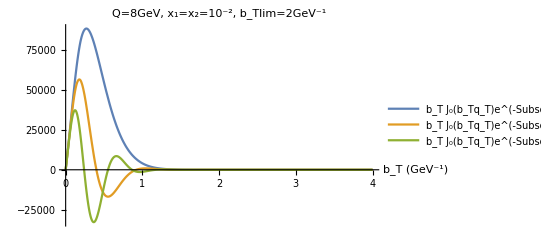

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->1,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->8/.qt->10},{bt,0,4},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1"]
```

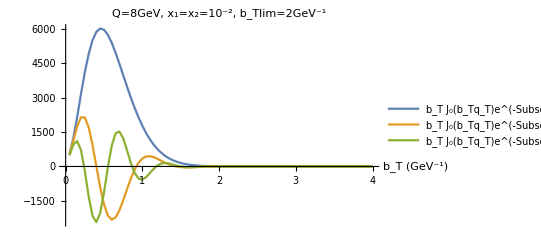

```mathematica
ListPlot[{Chh5qt1bt2,Chh5qt6bt2,Chh5qt10bt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True,PlotRange->All]
```

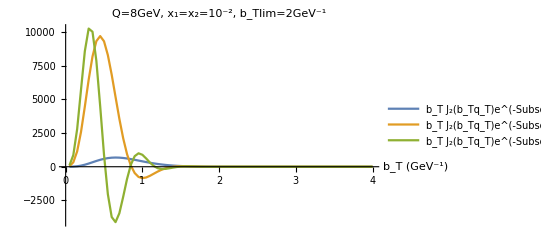

```mathematica
ListPlot[{Cw3fh5qt1bt2,Cw3fh5qt6bt2,Cw3fh5qt10bt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T] Q,))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True,PlotRange->All]
```

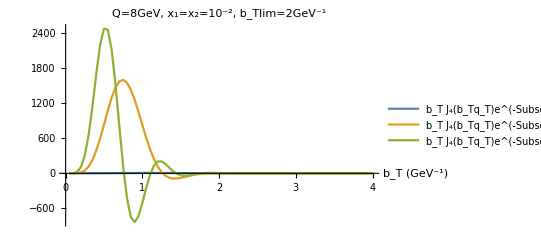

```mathematica
ListPlot[{Cw4hh5qt1bt2,Cw4hh5qt6bt2,Cw4hh5qt10bt2},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True,PlotRange->All]
```

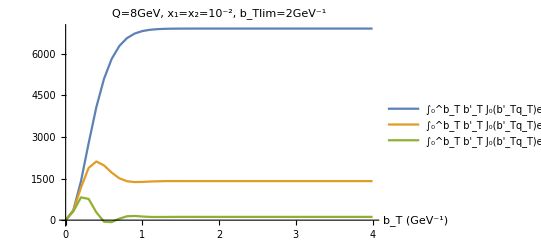

```mathematica
ListPlot[{Cfftunebtqt1bt2ev,Cfftunebtqt6bt2ev,Cfftunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))g(x_1,μ_B)g(x_2,μ_B)   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

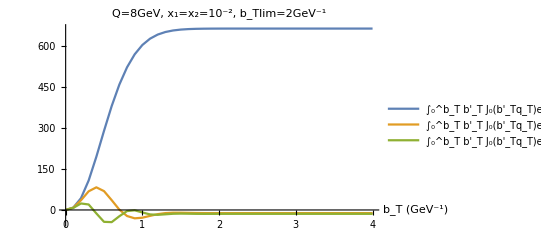

```mathematica
ListPlot[{Chhtunebtqt1bt2ev,Chhtunebtqt6bt2ev,Chhtunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

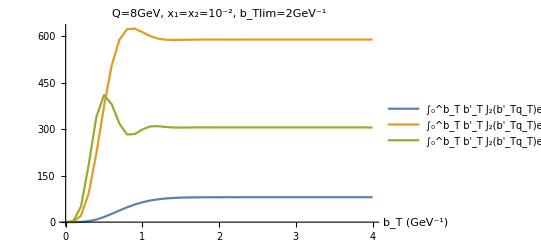

```mathematica
ListPlot[{Cw3fhtunebtqt1bt2ev,Cw3fhtunebtqt6bt2ev,Cw3fhtunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_2(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

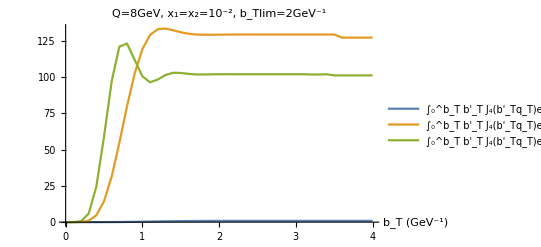

```mathematica
ListPlot[{Cw4hhtunebtqt1bt2ev,Cw4hhtunebtqt6bt2ev,Cw4hhtunebtqt10bt2ev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=1GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=6GeV","∫_0^b_T b'_T J_4(b'_Tq_T)e^(-SubscriptBox[S, A] (SubsuperscriptBox[b, T, '], Q))e^(-SubscriptBox[S, NP] (SubsuperscriptBox[b, T, '], Q, SubscriptBox[b, Tlim]))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   q_T=10GeV"},PlotLabel->"Q=8GeV, x_1=x_2=10^-2, b_Tlim=2GeV^-1",Joined->True]
```

C[w_0 h_1^(⊥g)h_1^(⊥g)]: after applying S_A at Q=8GeV, the integrand for low q_T(1 GeV) is still relevant at b_T=4 GeV^-1. Therefore a narrow S_NP will cut part of it a make the integral smaller. On the other side, the q_T-broadening happens for narrower S_NP, but is of no interest as at low Q, the limit q_T=Q/2 is reached before it significantly overcomes the larger initial normalisation of an integral using a wider S_NP. At large Q, the b_T-narrowing of S_A controls the large q_T values and S_NP has no effect, except at small q_T where the larger normalisation of a convolution using a wide S_NP makes it bigger.

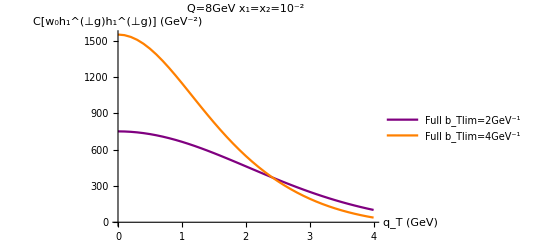
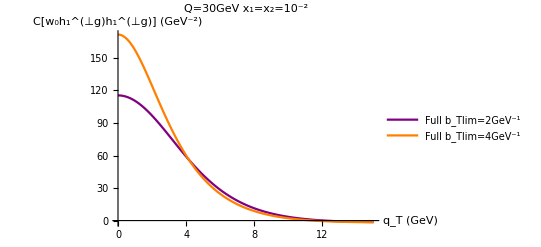

```mathematica
{ListPlot[{Chhbt2Q8,Chhbt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Chhbt2Q30,Chhbt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Mean::rectt: Rectangular array expected at position 1 in Mean[0.00165563].

Part::pkspec1: The expression Which[(0.00165563 SystemException[MemoryAllocationFailure])/Mean[0.00165563]<2,1,Charting`CommonDump`density>10,2,True,3] cannot be used as a part specification.

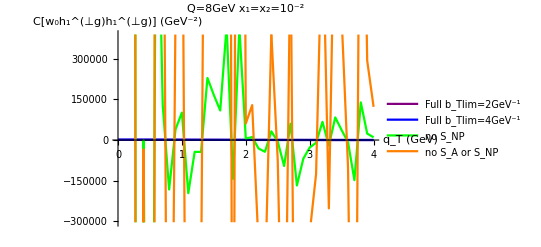
{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{Chhbt2Q8,Chhbt4Q8,ChhNoSnpQ8,ChhNoSQ8},Joined->True,PlotStyle->{Purple,Blue,Green,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_NP","no S_A or S_NP"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Chhbt2Q30,Chhbt4Q30,ChhNoSnpQ30,ChhNoSQ30},Joined->True,PlotStyle->{Purple,Blue,Green,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1","no S_NP","no S_A or S_NP"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

```mathematica
Cw3fhbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Cw3fhinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Cw3fhinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Cw3fhinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fhbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Cw3fhinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Cw3fhNoSnpQ8=Transpose[{qtvalsQ8,ParallelMap[Cw3fhintNoSnp[10^-2,8,#]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -53548.2 and 373761. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 259342. and 561793. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -59537.3 and 6274.41 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -9468.85 and 75317.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 123.564 and 25885.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -4728.49 and 21496.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 39149.1 and 86475. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 36928.5 and 39908. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -12199. and 16692.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 20448.4 and 21894.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 13596.5 and 21315.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 295.929 and 9296.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 11347. and 4111.28 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -1182.89 and 25013.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -6980.89 and 20471.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 35685.1 and 45836.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 370439. and 591592. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 9654.62 and 8916.53 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 8943.45 and 13660.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -120707. and 191731. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 27737.3 and 40686.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -57926.4 and 90035.2 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 15205.6 and 16345.5 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 22075.9 and 47006.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 9289.36 and 838.587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 8843.43 and 15841.3 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -9499.87 and 26995.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 1669.71 and 12105.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 6057.78 and 2607.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -10002.9 and 25989.1 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 9699.86 and 9014.14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 10151.4 and 9207.33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 18122. and 16833.7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 8569.4 and 386.151 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained -1834.36 and 9644.39 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 640.258 and 12124.6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 2996.13 and 6292.81 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 2795.22 and 5016.73 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 5294.35 and 3816. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in bt near {y2,bt} = {1.,9.35671×10^10}. NIntegrate obtained 16599.3 and 15226.5 for the integral and error estimates.

C[w_3 f_1^g h_1^(⊥g)]: because when the integrand contains J_2 or J_4 the dilatation of the oscillations shifts the values to the larger b_T, a wider NP Sudakov actually allows to have larger normalisations for the convolutions: the first peak, the largest and positive at smaller b_T and majoritarily contributing to the integral for q_T=6GeV, is more suppressed by a narrow S_NP than a wide one. The q_T-broadening for narrow S_NP is sligthly visible but negligible. At large Q, the difference between the two widths of S_NP is smaller but still relevant, unlike for the C[f_1^g f_1^g] and C[w_0 h_1^(⊥g)h_1^(⊥g)] cases.

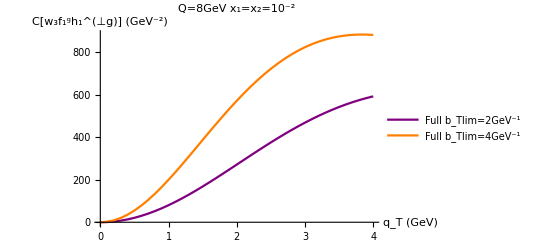
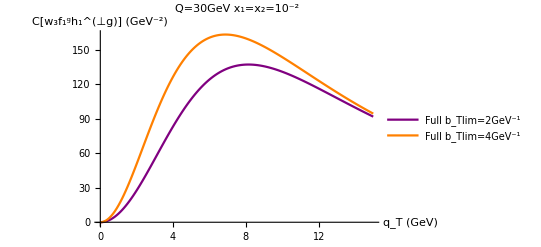

```mathematica
{ListPlot[{Cw3fhbt2Q8,Cw3fhbt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Cw3fhbt2Q30,Cw3fhbt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

```mathematica
Cw3fhintSnptest[x_,Q_,qt_,bt_,A_]:=bt BesselJ[2,qt bt]((Nc αs[μbfrozen[bt,Q]])/π)ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])NIntegrate[gMSTW[x,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1}];
```

```mathematica
Cw3fhSnptestbt2qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhintSnptest[10^-2,8,6,#,0.64] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw3fhSnptestbt4qt6=Transpose[{Range[0,4,0.05],ParallelMap[Cw3fhintSnptest[10^-2,8,6,#,0.16] &,Range[0,4,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

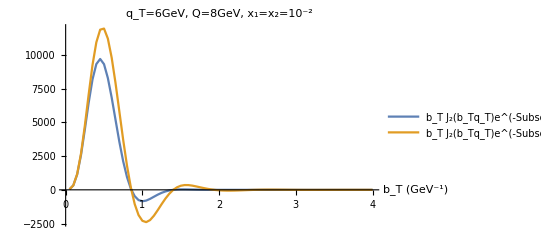

-Graphics-

```mathematica
ListPlot[{Cw3fhSnptestbt2qt6,Cw3fhSnptestbt4qt6},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   b_Tlim=2GeV^-1","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q, SubscriptBox[b, Tlim]))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   b_Tlim=4GeV^-1"},PlotLabel->"q_T=6GeV, Q=8GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

```mathematica
Cw4hhbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Cw4hhinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.013 and 0.000247594 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 31.9574 and 0.0000716902 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 69.8997 and 0.000153507 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 48.5859 and 0.000107263 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19.6247 and 0.0000427517 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 127.129 and 0.000286095 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 96.0891 and 0.000211042 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 82.3814 and 0.000179368 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 58.6403 and 0.000129891 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.150744 and 3.22887×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000595964 and 1.29331×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00951251 and 2.05755×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.751045 and 1.61906×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.0324 and 0.0000233329 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.50799 and 0.0000118152 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32134 and 4.87222×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 144.4 and 0.000327595 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 162.777 and 0.00036237 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.706 and 0.0000894907 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 182.198 and 0.00040059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.2854 and 0.0000560683 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 202.592 and 0.000441863 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 223.876 and 0.000479862 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 245.96 and 0.000517559 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 268.747 and 0.00054161 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 292.133 and 0.000603994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.365389 and 7.9588×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14.9009 and 0.0000322415 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0479645 and 1.02418×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.37706 and 2.96904×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.93176 and 0.0000168307 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.66853 and 7.6899×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 316.011 and 0.000628729 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 340.269 and 0.000685944 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 389.48 and 0.000786169 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 414.208 and 0.000853623 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 364.797 and 0.000742659 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 487.579 and 0.0010374 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 463.362 and 0.000972013 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 438.871 and 0.000903749 for the integral and error estimates.

```mathematica
Cw4hhbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Cw4hhinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14.2557 and 0.0000273844 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 49.3434 and 0.0000731618 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 78.0718 and 0.000115856 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 21.4513 and 0.0000325049 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 29.9546 and 0.0000430459 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.142204 and 2.57519×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.60912 and 0.0000168836 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00914402 and 1.64005×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000147648 and 2.58654×10^-11 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.3967 and 0.0000576772 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.57763 and 8.26397×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.6869 and 1.24278×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.03475 and 3.76877×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 59.356 and 0.0000819272 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 86.2198 and 0.000128902 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 69.0392 and 0.0000961932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 15.5763 and 0.0000285569 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 51.3542 and 0.00007596 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 79.7781 and 0.000123282 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 23.0577 and 0.0000338203 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 31.7813 and 0.000046027 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.60855 and 0.0000201242 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.206558 and 3.78804×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0188819 and 3.4001×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 41.36 and 0.0000614644 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000235966 and 4.13941×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.879003 and 1.60325×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.43636 and 4.48551×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 61.3305 and 0.0000876005 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.25809 and 9.59328×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 70.9066 and 0.0000967508 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 87.7288 and 0.000123752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16.9581 and 0.0000289662 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 53.364 and 0.0000774809 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 10.6733 and 0.0000240559 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 81.4473 and 0.000132084 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.290024 and 5.3105×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0348088 and 6.24927×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 33.6423 and 0.000049502 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 24.7142 and 0.0000361772 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0011923 and 2.09374×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 43.3399 and 0.0000632377 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.88893 and 5.44556×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.10657 and 2.01398×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 63.2887 and 0.0000914916 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.00028 and 0.0000111537 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 72.7455 and 0.0000988577 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 89.1954 and 0.000121047 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 93.3354 and 0.000119998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 99.348 and 0.000152501 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.075 and 0.000205722 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 104.249 and 0.000163204 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.895 and 0.000204677 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 94.6273 and 0.000125291 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.884 and 0.000217904 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.799 and 0.000207562 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.583 and 0.000209736 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.091 and 0.000197389 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.25 and 0.000199451 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.692 and 0.000261034 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.769 and 0.000229182 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.39 and 0.000277238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.898 and 0.000275687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 107.246 and 0.000284749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 105.463 and 0.000298844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 100.416 and 0.000155334 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.717 and 0.000201813 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 105.098 and 0.000172 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.346 and 0.00020434 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 95.8745 and 0.000126819 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.011 and 0.000221758 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.078 and 0.000209742 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.995 and 0.0002004 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.246 and 0.000203448 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.387 and 0.000268281 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.406 and 0.000212172 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.499 and 0.00029113 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.523 and 0.000232134 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 110.034 and 0.000285042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 106.812 and 0.000291378 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 101.44 and 0.000158975 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 105. and 0.00030598 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 109.319 and 0.000203179 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 105.905 and 0.00018273 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.762 and 0.00020587 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.111 and 0.000207568 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.326 and 0.000202222 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.878 and 0.000201724 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 111.067 and 0.000271624 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 108.09 and 0.000280692 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.217 and 0.000193204 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 109.666 and 0.000270137 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.211 and 0.000222141 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 112.261 and 0.00024961 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 106.369 and 0.000281118 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 104.531 and 0.00031912 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
Cw4hhbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Cw4hhinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 770.937 and 0.00215395 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 38.2458 and 0.000132116 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0115037 and 4.01164×10^-8 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 829.099 and 0.00227456 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 13.2581 and 0.0000454544 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.79928 and 9.52776×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.182192 and 6.31736×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 588.399 and 0.00155069 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.011 and 0.000453328 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 346.995 and 0.000978465 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 650.139 and 0.00180008 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 711.149 and 0.00196143 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 240.294 and 0.00066486 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 465.145 and 0.00129661 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 83.3071 and 0.00025413 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 526.511 and 0.00143964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1130.7 and 0.00370504 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1040.18 and 0.00332397 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 939.349 and 0.00295437 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 991.011 and 0.00313062 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 885.318 and 0.00265249 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1086.76 and 0.0034025 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1171.97 and 0.00396506 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 23.5362 and 0.0000788318 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1210.57 and 0.00402966 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.63139 and 0.0000229746 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 58.0229 and 0.000181341 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.906855 and 3.07025×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 193.155 and 0.000555811 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.311 and 0.000338742 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 291.815 and 0.000820641 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 405.042 and 0.00105428 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1386.67 and 0.00534245 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1310.36 and 0.00454535 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1246.48 and 0.00436082 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1338.36 and 0.00467784 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1363.78 and 0.00516398 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1279.74 and 0.0044818 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1425.01 and 0.00516709 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1407.06 and 0.00509689 for the integral and error estimates.

```mathematica
Cw4hhbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Cw4hhinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 37.5891 and 0.000126913 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 53.5711 and 0.000162358 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.0856 and 0.0000453413 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 23.3423 and 0.0000839859 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.68738 and 0.0000181422 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000124225 and 4.99903×10^-10 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.08542 and 4.16456×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0750831 and 2.82584×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 70.0486 and 0.000179565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 85.9875 and 0.000187422 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 100.629 and 0.000230518 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 113.495 and 0.000275681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 124.358 and 0.000287861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 140.038 and 0.000305659 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 145.099 and 0.000343248 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 133.177 and 0.000290934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 40.6883 and 0.000134781 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 25.9903 and 0.0000899699 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 14.0461 and 0.0000509927 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 56.8637 and 0.000162225 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.84409 and 0.0000222717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00197924 and 7.52496×10^-9 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.153346 and 5.87869×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.54596 and 5.80644×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 73.3079 and 0.000172903 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 89.0387 and 0.00021149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 103.355 and 0.000237095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 115.832 and 0.000255877 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 126.284 and 0.00028587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 134.701 and 0.000312175 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 141.189 and 0.000328624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 145.911 and 0.000350544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 43.8463 and 0.000142346 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 28.7493 and 0.000101216 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 16.1589 and 0.0000588674 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 60.1663 and 0.000173409 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.16107 and 0.0000269866 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00994995 and 3.78075×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.279079 and 1.07196×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.12529 and 7.98337×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 76.5377 and 0.000178664 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 92.0325 and 0.000212889 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 106.006 and 0.00028382 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.086 and 0.000261595 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 128.128 and 0.000290498 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 136.149 and 0.000328891 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 142.268 and 0.00034882 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 146.661 and 0.000357924 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 148.548 and 0.000334653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.586 and 0.000394552 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.408 and 0.000447482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.147 and 0.000579621 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.204 and 0.000476785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 149.062 and 0.000336472 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 146.079 and 0.000547292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 148.393 and 0.000490746 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 143.319 and 0.000496917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 140.855 and 0.000502965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.841 and 0.000412527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.444 and 0.000469362 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 138.209 and 0.000532638 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 149.847 and 0.00059687 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.055 and 0.000508153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 135.419 and 0.000526564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 132.517 and 0.000566398 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 129.532 and 0.000657341 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 126.491 and 0.000657637 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 149.521 and 0.000345017 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 120.329 and 0.000639232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 123.416 and 0.000632193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 145.559 and 0.000548839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 142.722 and 0.000478529 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 147.971 and 0.000514757 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.05 and 0.000453171 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 151.439 and 0.000474021 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 150.874 and 0.000517919 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 140.209 and 0.000508723 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 149.521 and 0.000507158 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 134.703 and 0.000582455 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 137.524 and 0.000516557 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 131.777 and 0.000602504 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 128.776 and 0.000659432 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 119.557 and 0.00082254 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 125.725 and 0.000684386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 145.023 and 0.000508713 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 142.112 and 0.000494528 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 122.645 and 0.000638388 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 147.528 and 0.000533459 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 133.98 and 0.000584197 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 139.553 and 0.000519652 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 131.033 and 0.000632493 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 128.017 and 0.000653223 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 118.786 and 0.00061789 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 136.83 and 0.000526328 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 124.957 and 0.000668469 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 121.873 and 0.000658757 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

Same observations as for C[w_3 f_1^g h_1^(⊥g)] but with enhanced effects due to the increased oscillations width of J_4 compared to J_2.

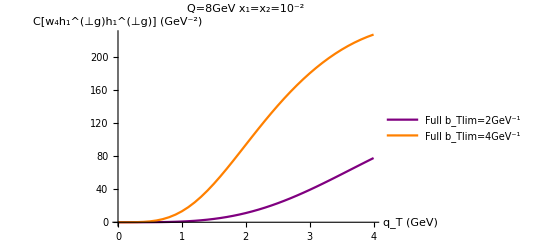
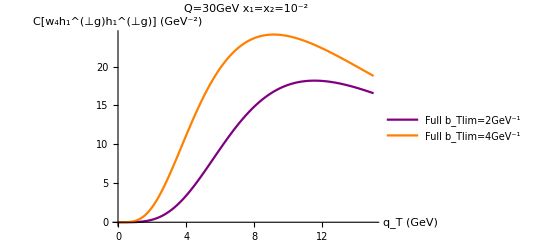

```mathematica
{ListPlot[{Cw4hhbt2Q8,Cw4hhbt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{Cw4hhbt2Q30,Cw4hhbt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)] (GeV^-2)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

```mathematica
Cffinttunebt[x_?NumericQ,Q_?NumericQ,qt_?NumericQ,A_?NumericQ]:=1/(2π)NIntegrate[bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,A])gMSTW[x,μbfrozen[bt,Q]]^2,{bt,0,∞}];
```

```mathematica
Cffbt2Q8=Transpose[{qtvalsQ8,ParallelMap[Cffinttunebt[10^-2,8,#,0.64]&,qtvalsQ8]}];
```

```mathematica
Cffbt2Q30=Transpose[{qtvalsQ30,ParallelMap[Cffinttunebt[10^-2,30,#,0.64]&,qtvalsQ30]}];
```

```mathematica
Cffbt4Q8=Transpose[{qtvalsQ8,ParallelMap[Cffinttunebt[10^-2,8,#,0.16]&,qtvalsQ8]}];
```

```mathematica
Cffbt4Q30=Transpose[{qtvalsQ30,ParallelMap[Cffinttunebt[10^-2,30,#,0.16]&,qtvalsQ30]}];
```

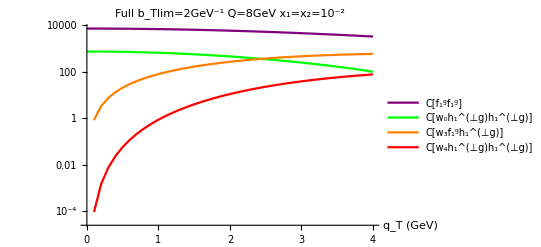
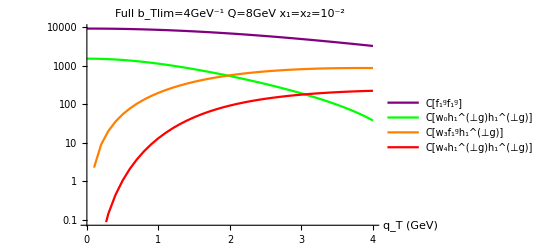
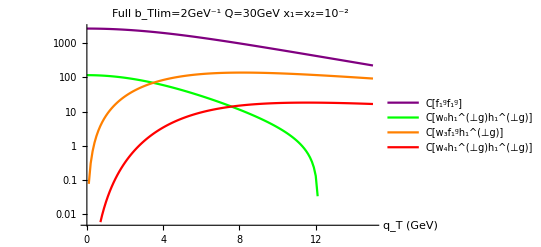
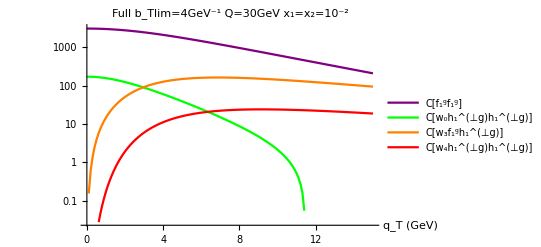

```mathematica
{ListLogPlot[{Cffbt2Q8,Chhbt2Q8,Cw3fhbt2Q8,Cw4hhbt2Q8},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=2GeV^-1 Q=8GeV x_1=x_2=10^-2"],ListLogPlot[{Cffbt4Q8,Chhbt4Q8,Cw3fhbt4Q8,Cw4hhbt4Q8},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=4GeV^-1 Q=8GeV x_1=x_2=10^-2"],ListLogPlot[{Cffbt2Q30,Chhbt2Q30,Cw3fhbt2Q30,Cw4hhbt2Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=2GeV^-1 Q=30GeV x_1=x_2=10^-2"],ListLogPlot[{Cffbt4Q30,Chhbt4Q30,Cw3fhbt4Q30,Cw4hhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"C[f_1^gf_1^g]","C[w_0h_1^(⊥g)h_1^(⊥g)]","C[w_3f_1^gh_1^(⊥g)]","C[w_4h_1^(⊥g)h_1^(⊥g)]"},AxesLabel->{"q_T (GeV)",},PlotLabel->"Full b_Tlim=4GeV^-1 Q=30GeV x_1=x_2=10^-2"]}
```

```mathematica
{ListPlot[{Cffbt2Q8,Cffbt2Q30,Cffbt4Q8,Cffbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[f_1^gf_1^g]"},PlotLabel->"x_1=x_2=10^-2"],
ListPlot[{Chhbt2Q8,Chhbt2Q30,Chhbt4Q8,Chhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)]"},PlotLabel->"x_1=x_2=10^-2"],
ListPlot[{Cw3fhbt2Q8,Cw3fhbt2Q30,Cw3fhbt4Q8,Cw3fhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)]"},PlotLabel->"x_1=x_2=10^-2"],
ListPlot[{Cw4hhbt2Q8,Cw4hhbt2Q30,Cw4hhbt4Q8,Cw4hhbt4Q30},Joined->True,PlotStyle->{Purple,Green,Orange,Red},PlotLegends->{"b_Tlim=2GeV^-1 Q=8GeV","b_Tlim=2GeV^-1 Q=30GeV","b_Tlim=4GeV^-1 Q=8GeV","b_Tlim=4GeV^-1 Q=30GeV"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)]"},PlotLabel->"x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
R0bt2Q8=Transpose[{qtvalsQ8,Chhbt2Q8[[All,2]]/Cffbt2Q8[[All,2]]}];
```

```mathematica
R0bt4Q8=Transpose[{qtvalsQ8,Chhbt4Q8[[All,2]]/Cffbt4Q8[[All,2]]}];
```

```mathematica
R0bt2Q30=Transpose[{qtvalsQ30,Chhbt2Q30[[All,2]]/Cffbt2Q30[[All,2]]}];
```

```mathematica
R0bt4Q30=Transpose[{qtvalsQ30,Chhbt4Q30[[All,2]]/Cffbt4Q30[[All,2]]}];
```

```mathematica
{ListPlot[{R0bt2Q8,R0bt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{R0bt2Q30,R0bt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_0h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
R2bt2Q8=Transpose[{qtvalsQ8,Cw3fhbt2Q8[[All,2]]/Cffbt2Q8[[All,2]]}];
```

```mathematica
R2bt4Q8=Transpose[{qtvalsQ8,Cw3fhbt4Q8[[All,2]]/Cffbt4Q8[[All,2]]}];
```

```mathematica
R2bt2Q30=Transpose[{qtvalsQ30,Cw3fhbt2Q30[[All,2]]/Cffbt2Q30[[All,2]]}];
```

```mathematica
R2bt4Q30=Transpose[{qtvalsQ30,Cw3fhbt4Q30[[All,2]]/Cffbt4Q30[[All,2]]}];
```

```mathematica
{ListPlot[{R2bt2Q8,R2bt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{R2bt2Q30,R2bt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_3f_1^gh_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

```mathematica
R4bt2Q8=Transpose[{qtvalsQ8,Cw4hhbt2Q8[[All,2]]/Cffbt2Q8[[All,2]]}];
```

```mathematica
R4bt4Q8=Transpose[{qtvalsQ8,Cw4hhbt4Q8[[All,2]]/Cffbt4Q8[[All,2]]}];
```

```mathematica
R4bt2Q30=Transpose[{qtvalsQ30,Cw4hhbt2Q30[[All,2]]/Cffbt2Q30[[All,2]]}];
```

```mathematica
R4bt4Q30=Transpose[{qtvalsQ30,Cw4hhbt4Q30[[All,2]]/Cffbt4Q30[[All,2]]}];
```

```mathematica
{ListPlot[{R4bt2Q8,R4bt4Q8},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=8GeV x_1=x_2=10^-2"],
ListPlot[{R4bt2Q30,R4bt4Q30},Joined->True,PlotStyle->{Purple,Orange},PlotLegends->{"Full b_Tlim=2GeV^-1","Full b_Tlim=4GeV^-1"},AxesLabel->{"q_T (GeV)","C[w_4h_1^(⊥g)h_1^(⊥g)]/C[f_1^gf_1^g]"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"]}
```

{-Graphics-,-Graphics-}

Saving the time-consuming convolution computational results

```mathematica
DumpSave["Full_evol_convols_290319.mx",{Chhbt2Q8,Cw3fhbt2Q8,Cw4hhbt2Q8,Chhbt4Q8,Cw3fhbt4Q8,Cw4hhbt4Q8,Chhbt2Q30,Cw3fhbt2Q30,Cw4hhbt2Q30,Chhbt4Q30,Cw3fhbt4Q30,Cw4hhbt4Q30}];
```

Testing the code without evolution: no α_s- related effect, no scale variation, no S_A to have a code equivalent as the non-evolved Gaussian model. Goal: understanding the sign change between the non-evolved gaussian model cos(2ϕ)-convolution C[w_3 f_1 h_1] (negative) and its evolved countered part computed in b_T-space (positive)

No need for α_s or the PDF as they are positive constants (i.e. b_T-independent) in this model, h_1 is a Gaussian*b_T^2

```mathematica
wid=0.64;
```

```mathematica
Cffnoev[qt_?NumericQ,bt_?NumericQ]:=NIntegrate[btp BesselJ[0,qt btp] ⅇ^(-wid btp^2),{btp,0,bt}];
```

```mathematica
Chhnoev[qt_?NumericQ,bt_?NumericQ]:=NIntegrate[btp^5 BesselJ[0,qt btp] ⅇ^(-wid btp^2),{btp,0,bt}];
```

```mathematica
Cw3fhnoev[qt_?NumericQ,bt_?NumericQ]:=NIntegrate[btp^3 BesselJ[2,qt btp] ⅇ^(-wid btp^2),{btp,0,bt}];
```

```mathematica
Cw4hhnoev[qt_?NumericQ,bt_?NumericQ]:=NIntegrate[btp^5 BesselJ[4,qt btp] ⅇ^(-wid btp^2),{btp,0,bt}];
```

```mathematica
Cffqt1bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cffnoev[1,#] &,Range[0,16,0.1]]}];
```

```mathematica
Cffqt6bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cffnoev[6,#] &,Range[0,16,0.1]]}];
```

```mathematica
Cffqt10bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cffnoev[10,#] &,Range[0,16,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05581}. NIntegrate obtained -3.04444×10^-15 and 7.5409×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06947}. NIntegrate obtained 2.17708×10^-16 and 1.09227×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04681}. NIntegrate obtained 2.39392×10^-16 and 1.53402×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.956381}. NIntegrate obtained 1.84748×10^-16 and 9.74087×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05617}. NIntegrate obtained 5.15457×10^-10 and 1.76407×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00616}. NIntegrate obtained -8.68318×10^-11 and 6.15901×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13663}. NIntegrate obtained 4.40897×10^-12 and 1.0642×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.99995}. NIntegrate obtained -6.2365×10^-14 and 6.40161×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13198}. NIntegrate obtained -3.29858×10^-15 and 1.23443×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.956781}. NIntegrate obtained -1.21431×10^-16 and 7.36448×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03266}. NIntegrate obtained 2.34188×10^-17 and 9.69254×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03764}. NIntegrate obtained 7.76289×10^-17 and 7.90544×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.972886}. NIntegrate obtained 3.70147×10^-16 and 1.07921×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05814}. NIntegrate obtained -3.0401×10^-16 and 1.07257×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04993}. NIntegrate obtained 4.68375×10^-17 and 1.29905×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11243}. NIntegrate obtained 2.05998×10^-16 and 9.85081×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13196}. NIntegrate obtained -3.26562×10^-16 and 1.39049×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13176}. NIntegrate obtained 1.32706×10^-16 and 1.53706×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09094}. NIntegrate obtained -4.03757×10^-16 and 9.91898×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12824}. NIntegrate obtained 7.35863×10^-10 and 8.84378×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07979}. NIntegrate obtained -3.764×10^-11 and 1.33448×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.905374}. NIntegrate obtained 3.21146×10^-13 and 7.10186×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04731}. NIntegrate obtained 5.63959×10^-14 and 9.44671×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04584}. NIntegrate obtained -5.59448×10^-16 and 1.01667×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00541}. NIntegrate obtained -6.70037×10^-17 and 1.19513×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained 2.52836×10^-16 and 1.17512×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.997791}. NIntegrate obtained 6.21031×10^-16 and 1.48891×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04896}. NIntegrate obtained -1.38832×10^-16 and 1.49227×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11292}. NIntegrate obtained -1.92771×10^-16 and 1.17073×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07904}. NIntegrate obtained -5.72459×10^-17 and 1.33949×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.993094}. NIntegrate obtained 1.32706×10^-16 and 9.18903×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.980787}. NIntegrate obtained -3.33067×10^-16 and 1.30145×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.9843}. NIntegrate obtained 7.00828×10^-16 and 1.30948×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.96672}. NIntegrate obtained 1.05211×10^-15 and 1.19144×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09475}. NIntegrate obtained 1.73472×10^-18 and 1.32139×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04406}. NIntegrate obtained 2.74141×10^-10 and 6.48128×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12139}. NIntegrate obtained 4.95748×10^-13 and 1.32976×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06553}. NIntegrate obtained -7.68042×10^-13 and 1.17137×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04409}. NIntegrate obtained 3.85651×10^-14 and 8.69745×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04789}. NIntegrate obtained -5.89806×10^-17 and 1.01083×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.979724}. NIntegrate obtained 4.2067×10^-16 and 6.96997×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07415}. NIntegrate obtained -1.89519×10^-16 and 1.09127×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.01302}. NIntegrate obtained 1.64799×10^-16 and 1.46597×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11985}. NIntegrate obtained 3.30031×10^-16 and 1.22322×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08928}. NIntegrate obtained -2.92084×10^-16 and 9.74961×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04484}. NIntegrate obtained 8.67362×10^-18 and 1.02104×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06574}. NIntegrate obtained -5.20417×10^-17 and 1.48079×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03596}. NIntegrate obtained 1.45717×10^-16 and 9.30882×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05617}. NIntegrate obtained 3.76435×10^-16 and 1.85235×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04484}. NIntegrate obtained -1.9082×10^-16 and 1.18864×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06339}. NIntegrate obtained -3.56486×10^-16 and 1.62829×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13653}. NIntegrate obtained -4.34765×10^-16 and 1.23246×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12139}. NIntegrate obtained -4.90276×10^-16 and 1.43639×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.941216}. NIntegrate obtained 4.95535×10^-16 and 8.98373×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06026}. NIntegrate obtained -3.43909×10^-16 and 1.15444×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11074}. NIntegrate obtained -1.38412×10^-16 and 1.05009×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05607}. NIntegrate obtained 2.01228×10^-16 and 2.0432×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.99995}. NIntegrate obtained -2.1684×10^-16 and 6.40161×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04406}. NIntegrate obtained -2.94903×10^-16 and 6.53915×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06177}. NIntegrate obtained 1.87784×10^-16 and 7.08658×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04054}. NIntegrate obtained -3.80772×10^-16 and 8.09556×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08608}. NIntegrate obtained -3.24863×10^-17 and 6.87461×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07979}. NIntegrate obtained -1.31839×10^-16 and 1.36621×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00336}. NIntegrate obtained 3.79898×10^-16 and 8.51463×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03901}. NIntegrate obtained -9.02056×10^-17 and 7.87025×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06127}. NIntegrate obtained 4.36717×10^-16 and 1.41699×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04789}. NIntegrate obtained -1.14492×10^-16 and 1.01083×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08536}. NIntegrate obtained -4.44523×10^-16 and 1.20782×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13663}. NIntegrate obtained 6.451×10^-16 and 1.06334×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09297}. NIntegrate obtained 3.48679×10^-16 and 1.57048×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.052}. NIntegrate obtained -2.63244×10^-16 and 9.76704×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12824}. NIntegrate obtained -2.60209×10^-16 and 9.76207×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00146}. NIntegrate obtained -3.12684×10^-16 and 9.17821×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10695}. NIntegrate obtained 8.17488×10^-17 and 8.68069×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04409}. NIntegrate obtained -7.069×10^-17 and 8.69745×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08273}. NIntegrate obtained -1.79761×10^-16 and 1.04981×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05464}. NIntegrate obtained 3.1572×10^-16 and 9.20832×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.988192}. NIntegrate obtained 5.29091×10^-17 and 1.16158×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13198}. NIntegrate obtained -3.84241×10^-16 and 1.23443×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00512}. NIntegrate obtained 3.4521×10^-16 and 9.29981×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00541}. NIntegrate obtained -2.61293×10^-16 and 1.19513×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05507}. NIntegrate obtained -9.02924×10^-16 and 1.22408×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12763}. NIntegrate obtained -1.86916×10^-16 and 1.22448×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10616}. NIntegrate obtained -5.29091×10^-17 and 1.26405×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08702}. NIntegrate obtained -9.6971×10^-16 and 1.30122×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06553}. NIntegrate obtained 1.27936×10^-16 and 1.17855×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04795}. NIntegrate obtained 5.28223×10^-16 and 1.15029×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04731}. NIntegrate obtained -3.08781×10^-16 and 9.44671×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.052}. NIntegrate obtained -3.80338×10^-16 and 1.10452×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05581}. NIntegrate obtained 1.27068×10^-16 and 7.94346×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11982}. NIntegrate obtained 1.11022×10^-16 and 1.13587×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained -7.2338×10^-16 and 1.00773×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12568}. NIntegrate obtained -2.38091×10^-16 and 1.07431×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06947}. NIntegrate obtained 2.24647×10^-16 and 1.09227×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03266}. NIntegrate obtained 3.72966×10^-17 and 9.69254×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05429}. NIntegrate obtained 5.42535×10^-16 and 1.55904×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained 2.52836×10^-16 and 1.17512×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.983826}. NIntegrate obtained 5.84602×10^-16 and 1.02301×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.979724}. NIntegrate obtained 4.2067×10^-16 and 6.96997×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.918837}. NIntegrate obtained -1.53089×10^-16 and 1.08482×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.997791}. NIntegrate obtained 6.21031×10^-16 and 1.48891×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.0558}. NIntegrate obtained -1.43982×10^-16 and 1.12312×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03764}. NIntegrate obtained 7.76289×10^-17 and 7.90544×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.896863}. NIntegrate obtained -1.31839×10^-16 and 7.22218×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04681}. NIntegrate obtained 2.39392×10^-16 and 1.53402×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Chhqt1bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Chhnoev[1,#] &,Range[0,16,0.1]]}];
```

```mathematica
Chhqt6bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Chhnoev[6,#] &,Range[0,16,0.1]]}];
```

```mathematica
Chhqt10bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Chhnoev[10,#] &,Range[0,16,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11557}. NIntegrate obtained -8.08425×10^-12 and 1.63565×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06947}. NIntegrate obtained 7.83054×10^-15 and 2.20656×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08745}. NIntegrate obtained -9.46681×10^-11 and 1.26885×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13198}. NIntegrate obtained -6.77814×10^-12 and 2.36574×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13012}. NIntegrate obtained 5.09798×10^-13 and 1.36004×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03266}. NIntegrate obtained -6.99679×10^-15 and 1.4904×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03764}. NIntegrate obtained 2.90997×10^-14 and 1.02639×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06986}. NIntegrate obtained 2.7936×10^-14 and 1.52417×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08588}. NIntegrate obtained 2.84998×10^-14 and 2.27925×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11243}. NIntegrate obtained 2.86507×10^-14 and 1.58591×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13196}. NIntegrate obtained 2.90742×10^-14 and 2.45832×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05814}. NIntegrate obtained 2.80947×10^-14 and 1.33171×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06026}. NIntegrate obtained 3.27166×10^-10 and 1.32549×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04731}. NIntegrate obtained 1.09056×10^-10 and 1.30479×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10053}. NIntegrate obtained -1.65425×10^-12 and 2.14285×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.0476}. NIntegrate obtained 5.57826×10^-13 and 1.47095×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained 1.70591×10^-14 and 2.05413×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.997791}. NIntegrate obtained 3.15798×10^-14 and 1.59301×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04993}. NIntegrate obtained 2.85761×10^-14 and 1.73445×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12318}. NIntegrate obtained 2.83152×10^-14 and 1.02181×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.993094}. NIntegrate obtained 2.84716×10^-14 and 1.07363×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.980787}. NIntegrate obtained 2.76643×10^-14 and 1.08916×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11292}. NIntegrate obtained 2.84577×10^-14 and 1.58216×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13176}. NIntegrate obtained 2.83436×10^-14 and 2.11257×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09094}. NIntegrate obtained 2.7223×10^-14 and 1.20471×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09475}. NIntegrate obtained 2.84868×10^-14 and 1.65687×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12726}. NIntegrate obtained 2.84607×10^-14 and 2.35384×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04484}. NIntegrate obtained 2.86264×10^-14 and 1.67618×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06553}. NIntegrate obtained -1.21242×10^-9 and 1.52378×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04409}. NIntegrate obtained 7.52688×10^-11 and 1.742×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04789}. NIntegrate obtained 1.84954×10^-13 and 2.33231×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04916}. NIntegrate obtained 2.9711×10^-14 and 1.69798×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07904}. NIntegrate obtained 2.86142×10^-14 and 1.5248×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04896}. NIntegrate obtained 2.81294×10^-14 and 2.03763×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11966}. NIntegrate obtained 2.85588×10^-14 and 1.34967×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11985}. NIntegrate obtained 2.81658×10^-14 and 1.46854×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09134}. NIntegrate obtained 2.80249×10^-14 and 1.37204×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11555}. NIntegrate obtained 2.8498×10^-14 and 1.74581×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12141}. NIntegrate obtained 2.84525×10^-14 and 1.91089×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06574}. NIntegrate obtained 2.82205×10^-14 and 2.05025×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05607}. NIntegrate obtained 2.8511×10^-14 and 2.30857×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13898}. NIntegrate obtained 2.81342×10^-14 and 7.72761×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.052}. NIntegrate obtained -7.13499×10^-10 and 1.481×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08928}. NIntegrate obtained 2.88415×10^-14 and 1.26601×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04484}. NIntegrate obtained 2.85646×10^-14 and 1.30142×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09631}. NIntegrate obtained 2.84469×10^-14 and 1.19758×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12824}. NIntegrate obtained 2.8158×10^-14 and 1.29909×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10695}. NIntegrate obtained 2.86229×10^-14 and 1.08598×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06339}. NIntegrate obtained 2.77391×10^-14 and 1.69598×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13653}. NIntegrate obtained 2.77547×10^-14 and 1.68456×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13272}. NIntegrate obtained 2.78532×10^-14 and 1.44918×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07306}. NIntegrate obtained 2.85319×10^-14 and 1.69685×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12715}. NIntegrate obtained 2.88485×10^-14 and 1.45104×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07979}. NIntegrate obtained 2.81858×10^-14 and 1.68678×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06026}. NIntegrate obtained 2.79065×10^-14 and 1.48622×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11074}. NIntegrate obtained 2.81873×10^-14 and 1.40085×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08745}. NIntegrate obtained 2.81229×10^-14 and 1.26885×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06177}. NIntegrate obtained 2.8539×10^-14 and 1.31309×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08608}. NIntegrate obtained 2.81162×10^-14 and 1.41743×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00336}. NIntegrate obtained 2.89907×10^-14 and 1.36864×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12788}. NIntegrate obtained 2.84573×10^-14 and 1.47997×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10821}. NIntegrate obtained 2.78544×10^-14 and 9.78013×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.1046}. NIntegrate obtained 2.79364×10^-14 and 1.46879×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13663}. NIntegrate obtained 2.90495×10^-14 and 1.70275×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05557}. NIntegrate obtained 2.88936×10^-14 and 1.14922×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09297}. NIntegrate obtained 2.87669×10^-14 and 1.90083×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.052}. NIntegrate obtained 2.80466×10^-14 and 1.53651×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10854}. NIntegrate obtained 2.8117×10^-14 and 1.33984×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04409}. NIntegrate obtained 2.83113×10^-14 and 1.742×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05464}. NIntegrate obtained 2.86819×10^-14 and 1.68564×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13198}. NIntegrate obtained 2.76389×10^-14 and 2.36574×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06127}. NIntegrate obtained 2.87773×10^-14 and 2.57077×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04789}. NIntegrate obtained 2.83844×10^-14 and 2.33231×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12763}. NIntegrate obtained 2.81348×10^-14 and 2.24379×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained 2.91605×10^-14 and 2.05413×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05194}. NIntegrate obtained 2.87288×10^-14 and 1.61958×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09462}. NIntegrate obtained 2.80392×10^-14 and 2.11958×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10616}. NIntegrate obtained 2.82266×10^-14 and 1.71679×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08702}. NIntegrate obtained 2.72221×10^-14 and 1.54678×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06553}. NIntegrate obtained 2.84998×10^-14 and 1.6719×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04795}. NIntegrate obtained 2.84919×10^-14 and 1.3727×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04731}. NIntegrate obtained 2.81452×10^-14 and 1.30479×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.052}. NIntegrate obtained 2.78085×10^-14 and 1.56674×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11557}. NIntegrate obtained 2.8678×10^-14 and 1.71609×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11982}. NIntegrate obtained 2.84339×10^-14 and 2.25671×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.0476}. NIntegrate obtained 2.86935×10^-14 and 1.47095×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13402}. NIntegrate obtained 2.81971×10^-14 and 2.81891×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03266}. NIntegrate obtained 2.83638×10^-14 and 1.4904×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08319}. NIntegrate obtained 2.81155×10^-14 and 1.16515×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.997791}. NIntegrate obtained 2.95259×10^-14 and 1.59301×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained 2.77546×10^-14 and 2.07624×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12568}. NIntegrate obtained 2.77183×10^-14 and 2.90557×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06947}. NIntegrate obtained 2.83974×10^-14 and 2.20656×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05429}. NIntegrate obtained 2.89881×10^-14 and 3.12366×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03764}. NIntegrate obtained 2.87111×10^-14 and 1.02639×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12684}. NIntegrate obtained 2.80427×10^-14 and 1.29345×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04916}. NIntegrate obtained 2.89339×10^-14 and 1.69798×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.0558}. NIntegrate obtained 2.77911×10^-14 and 1.82942×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08588}. NIntegrate obtained 2.84443×10^-14 and 2.27925×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Cw3fhqt1bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cw3fhnoev[1,#] &,Range[0,16,0.1]]}];
```

```mathematica
Cw3fhqt6bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cw3fhnoev[6,#] &,Range[0,16,0.1]]}];
```

```mathematica
Cw3fhqt10bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cw3fhnoev[10,#] &,Range[0,16,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19946}. NIntegrate obtained -8.52472×10^-15 and 1.19746×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19995}. NIntegrate obtained 2.1815×10^-12 and 1.69862×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20111}. NIntegrate obtained 3.541×10^-16 and 2.53943×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11713}. NIntegrate obtained -1.83881×10^-16 and 2.41911×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19954}. NIntegrate obtained 4.78458×10^-16 and 2.27923×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20091}. NIntegrate obtained 1.93747×10^-15 and 2.61053×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06339}. NIntegrate obtained 1.45231×10^-9 and 1.6045×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12139}. NIntegrate obtained -5.92826×10^-11 and 1.40981×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13663}. NIntegrate obtained -1.57145×10^-10 and 1.09645×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11557}. NIntegrate obtained 1.76229×10^-13 and 1.36962×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00541}. NIntegrate obtained -9.74221×10^-15 and 1.42764×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04731}. NIntegrate obtained -2.57574×10^-12 and 1.09914×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained -4.55365×10^-17 and 1.61264×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09779}. NIntegrate obtained 2.74086×10^-16 and 1.16941×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19437}. NIntegrate obtained -1.47451×10^-16 and 2.59389×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11243}. NIntegrate obtained 3.92264×10^-16 and 1.75517×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20355}. NIntegrate obtained 3.72966×10^-16 and 2.26003×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19788}. NIntegrate obtained 5.86445×10^-16 and 1.31999×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13196}. NIntegrate obtained 1.06512×10^-15 and 1.72565×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20598}. NIntegrate obtained 7.60676×10^-16 and 2.34391×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04309}. NIntegrate obtained -2.2443×10^-17 and 5.51523×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20324}. NIntegrate obtained 4.64039×10^-16 and 2.9595×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10616}. NIntegrate obtained -3.22789×10^-10 and 1.51317×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20323}. NIntegrate obtained -7.68353×10^-12 and 1.54545×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13198}. NIntegrate obtained 1.42456×10^-13 and 1.53317×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04789}. NIntegrate obtained -2.81285×10^-15 and 1.30371×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04409}. NIntegrate obtained -1.69853×10^-12 and 1.3356×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19584}. NIntegrate obtained -4.82036×10^-16 and 2.06794×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04896}. NIntegrate obtained 2.0112×10^-16 and 1.97876×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {0.922782}. NIntegrate obtained -8.76793×10^-16 and 8.80577×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07415}. NIntegrate obtained 1.58575×10^-15 and 1.4913×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.1261}. NIntegrate obtained 6.72422×10^-16 and 1.34838×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11555}. NIntegrate obtained -3.07046×10^-16 and 1.49768×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12141}. NIntegrate obtained 2.08167×10^-16 and 1.81348×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06574}. NIntegrate obtained 1.02782×10^-16 and 2.33439×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19836}. NIntegrate obtained 6.77086×10^-17 and 2.16522×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06553}. NIntegrate obtained 3.13517×10^-11 and 1.89482×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10053}. NIntegrate obtained 3.33138×10^-14 and 1.24865×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20158}. NIntegrate obtained 3.1225×10^-16 and 1.9121×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08773}. NIntegrate obtained 1.60462×10^-17 and 1.93422×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11966}. NIntegrate obtained -7.47015×10^-17 and 1.42205×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06339}. NIntegrate obtained 7.78891×10^-16 and 1.79587×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20247}. NIntegrate obtained 9.18536×10^-16 and 2.98263×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20295}. NIntegrate obtained 7.68049×10^-16 and 1.53442×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20109}. NIntegrate obtained -7.47666×10^-16 and 1.95098×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19689}. NIntegrate obtained 4.2414×10^-16 and 2.30168×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05607}. NIntegrate obtained 5.17815×10^-16 and 1.70919×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13653}. NIntegrate obtained 1.28988×10^-15 and 1.33573×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20226}. NIntegrate obtained -1.27936×10^-17 and 4.03334×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20314}. NIntegrate obtained 5.65086×10^-16 and 1.96705×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.2007}. NIntegrate obtained 6.34041×10^-16 and 7.74497×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12433}. NIntegrate obtained 3.52583×10^-16 and 1.26244×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12139}. NIntegrate obtained 1.1254×10^-15 and 1.53969×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19688}. NIntegrate obtained 6.3621×10^-16 and 4.37598×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10695}. NIntegrate obtained 6.27536×10^-16 and 1.42512×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20323}. NIntegrate obtained 1.24401×10^-15 and 2.66358×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06085}. NIntegrate obtained 1.56559×10^-16 and 1.24418×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.2084}. NIntegrate obtained 4.01155×10^-16 and 1.57835×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20157}. NIntegrate obtained 2.38037×10^-16 and 1.19551×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19995}. NIntegrate obtained 6.78467×10^-16 and 1.69862×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20249}. NIntegrate obtained -1.56125×10^-17 and 1.36971×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19962}. NIntegrate obtained 8.40907×10^-16 and 2.001×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.03975}. NIntegrate obtained 2.92301×10^-15 and 1.07447×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08608}. NIntegrate obtained 1.09721×10^-16 and 7.50984×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20108}. NIntegrate obtained -4.83554×10^-17 and 3.13666×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.0435}. NIntegrate obtained -7.50268×10^-17 and 1.01799×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19351}. NIntegrate obtained 3.75134×10^-16 and 1.21238×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20307}. NIntegrate obtained 8.84926×10^-16 and 1.34344×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20092}. NIntegrate obtained 5.31693×10^-16 and 2.26639×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04789}. NIntegrate obtained 4.59702×10^-17 and 1.30371×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12763}. NIntegrate obtained 7.93528×10^-16 and 1.65445×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20303}. NIntegrate obtained 1.10784×10^-15 and 1.1289×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04409}. NIntegrate obtained 6.26235×10^-16 and 1.3356×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.10616}. NIntegrate obtained 6.245×10^-17 and 1.55551×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19306}. NIntegrate obtained 4.44042×10^-16 and 1.18223×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06553}. NIntegrate obtained 2.87097×10^-16 and 2.07866×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13198}. NIntegrate obtained 1.47885×10^-15 and 1.53317×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20298}. NIntegrate obtained 5.29958×10^-16 and 1.38186×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09462}. NIntegrate obtained 6.96058×10^-16 and 1.43511×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.00541}. NIntegrate obtained 3.46945×10^-16 and 1.42764×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13402}. NIntegrate obtained 1.34354×10^-15 and 1.29052×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20111}. NIntegrate obtained -2.56522×10^-16 and 2.53943×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05385}. NIntegrate obtained -2.53703×10^-16 and 1.61264×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.04731}. NIntegrate obtained 8.86877×10^-16 and 1.09914×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05849}. NIntegrate obtained 1.2863×10^-15 and 1.22067×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06708}. NIntegrate obtained -2.90566×10^-16 and 1.72852×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08773}. NIntegrate obtained 2.9924×10^-17 and 1.93422×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.2019}. NIntegrate obtained -2.32453×10^-16 and 1.66425×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11982}. NIntegrate obtained 3.747×10^-16 and 1.60764×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19946}. NIntegrate obtained 1.01438×10^-15 and 1.35341×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12568}. NIntegrate obtained 8.08056×10^-16 and 1.68013×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.06947}. NIntegrate obtained -6.89553×10^-17 and 1.30905×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.05429}. NIntegrate obtained -2.74303×10^-16 and 1.85068×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20272}. NIntegrate obtained 2.8276×10^-16 and 1.81634×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19584}. NIntegrate obtained -4.40403×10^-16 and 2.06794×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.07909}. NIntegrate obtained 4.94396×10^-16 and 1.00293×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09779}. NIntegrate obtained 2.87964×10^-16 and 1.16941×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19584}. NIntegrate obtained 4.62737×10^-16 and 1.88397×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11713}. NIntegrate obtained -1.83881×10^-16 and 2.41911×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Cw4hhqt1bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cw4hhnoev[1,#] &,Range[0,16,0.1]]}];
```

```mathematica
Cw4hhqt6bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cw4hhnoev[6,#] &,Range[0,16,0.1]]}];
```

```mathematica
Cw4hhqt10bt2noev=Transpose[{Range[0,16,0.1],ParallelMap[Cw4hhnoev[10,#] &,Range[0,16,0.1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19995}. NIntegrate obtained -5.18205×10^-11 and 2.36388×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.26831}. NIntegrate obtained -9.57225×10^-12 and 1.88099×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12787}. NIntegrate obtained 3.31328×10^-14 and 4.37148×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20306}. NIntegrate obtained 3.16244×10^-14 and 7.10894×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19946}. NIntegrate obtained 6.43257×10^-13 and 2.32587×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15619}. NIntegrate obtained 1.26678×10^-15 and 3.64369×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.26439}. NIntegrate obtained 3.18461×10^-14 and 6.59083×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11243}. NIntegrate obtained 3.51247×10^-14 and 4.37838×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20091}. NIntegrate obtained 3.00432×10^-14 and 4.4047×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17688}. NIntegrate obtained 3.03195×10^-14 and 4.50557×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20323}. NIntegrate obtained -9.02409×10^-11 and 5.10083×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18061}. NIntegrate obtained 1.23628×10^-10 and 1.96318×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14545}. NIntegrate obtained -6.76255×10^-12 and 2.69888×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18822}. NIntegrate obtained 3.43761×10^-14 and 3.78832×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15482}. NIntegrate obtained 2.99143×10^-14 and 5.6075×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17416}. NIntegrate obtained 5.70946×10^-13 and 3.30129×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17914}. NIntegrate obtained -5.30825×10^-15 and 4.3784×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18939}. NIntegrate obtained 3.17287×10^-14 and 5.58321×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.16888}. NIntegrate obtained 3.20666×10^-14 and 7.15882×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.1639}. NIntegrate obtained 3.20824×10^-14 and 8.03853×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15335}. NIntegrate obtained 3.14883×10^-14 and 3.14289×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13176}. NIntegrate obtained 3.16617×10^-14 and 3.94575×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.08137}. NIntegrate obtained 3.52226×10^-14 and 2.25677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.1342}. NIntegrate obtained 3.12753×10^-14 and 3.11868×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13742}. NIntegrate obtained 3.1043×10^-14 and 4.17877×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20226}. NIntegrate obtained 3.04218×10^-14 and 4.77711×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13818}. NIntegrate obtained -1.33129×10^-9 and 2.05381×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19233}. NIntegrate obtained 7.35917×10^-11 and 3.97714×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14838}. NIntegrate obtained -1.36727×10^-12 and 3.0828×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14945}. NIntegrate obtained 3.25436×10^-14 and 4.80624×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.26517}. NIntegrate obtained 2.89664×10^-14 and 4.41282×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19047}. NIntegrate obtained 1.69461×10^-13 and 3.46988×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19486}. NIntegrate obtained 2.16572×10^-14 and 4.16973×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15374}. NIntegrate obtained 3.12998×10^-14 and 4.13933×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19075}. NIntegrate obtained 3.20611×10^-14 and 1.02093×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18587}. NIntegrate obtained 2.96915×10^-14 and 7.95941×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17493}. NIntegrate obtained 2.97167×10^-14 and 4.04187×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19993}. NIntegrate obtained 3.22433×10^-14 and 2.96217×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.16008}. NIntegrate obtained 3.22277×10^-14 and 5.04395×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13547}. NIntegrate obtained 3.27568×10^-14 and 3.17935×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.11759}. NIntegrate obtained 3.08156×10^-14 and 2.40395×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18146}. NIntegrate obtained 3.10819×10^-14 and 4.75054×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.26733}. NIntegrate obtained -6.80746×10^-10 and 1.77241×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19348}. NIntegrate obtained 3.15928×10^-14 and 3.54872×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.16203}. NIntegrate obtained 3.2973×10^-14 and 4.70937×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19689}. NIntegrate obtained 3.19849×10^-14 and 4.38353×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14894}. NIntegrate obtained 3.09969×10^-14 and 5.38634×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17081}. NIntegrate obtained 3.14406×10^-14 and 3.4969×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18067}. NIntegrate obtained 3.0741×10^-14 and 3.95571×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18936}. NIntegrate obtained 3.18231×10^-14 and 4.67215×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19688}. NIntegrate obtained 3.06309×10^-14 and 4.51168×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20323}. NIntegrate obtained 3.11452×10^-14 and 3.54207×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.26943}. NIntegrate obtained 2.95779×10^-14 and 2.06417×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19995}. NIntegrate obtained 3.08578×10^-14 and 2.36388×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17051}. NIntegrate obtained 3.13569×10^-14 and 3.43176×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19731}. NIntegrate obtained 3.17477×10^-14 and 2.34684×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19736}. NIntegrate obtained 3.26111×10^-14 and 2.93288×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14838}. NIntegrate obtained 3.18722×10^-14 and 2.46497×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20314}. NIntegrate obtained 3.16292×10^-14 and 3.33625×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12411}. NIntegrate obtained 3.17933×10^-14 and 3.22371×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15772}. NIntegrate obtained 3.21934×10^-14 and 3.36349×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14249}. NIntegrate obtained 3.28682×10^-14 and 5.03375×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13428}. NIntegrate obtained 2.96919×10^-14 and 3.24739×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.09297}. NIntegrate obtained 3.32775×10^-14 and 2.11212×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.26733}. NIntegrate obtained 3.26926×10^-14 and 1.82792×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17153}. NIntegrate obtained 3.22119×10^-14 and 2.04813×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19233}. NIntegrate obtained 3.21445×10^-14 and 3.97714×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.1667}. NIntegrate obtained 3.14874×10^-14 and 3.17881×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14545}. NIntegrate obtained 3.00727×10^-14 and 2.69888×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18412}. NIntegrate obtained 3.1814×10^-14 and 3.26013×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19047}. NIntegrate obtained 3.12108×10^-14 and 3.46988×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17128}. NIntegrate obtained 3.21687×10^-14 and 4.26122×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19486}. NIntegrate obtained 3.28149×10^-14 and 4.16973×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.1806}. NIntegrate obtained 3.12426×10^-14 and 4.2712×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18116}. NIntegrate obtained 2.93971×10^-14 and 5.09197×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17416}. NIntegrate obtained 3.29316×10^-14 and 3.30129×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15665}. NIntegrate obtained 3.24142×10^-14 and 2.80793×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12921}. NIntegrate obtained 3.25173×10^-14 and 2.15853×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.13818}. NIntegrate obtained 3.35318×10^-14 and 2.34712×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15957}. NIntegrate obtained 3.25619×10^-14 and 2.53237×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18061}. NIntegrate obtained 3.09405×10^-14 and 1.97706×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14878}. NIntegrate obtained 3.24302×10^-14 and 1.74741×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12661}. NIntegrate obtained 3.05402×10^-14 and 3.01152×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.19946}. NIntegrate obtained 3.21965×10^-14 and 2.21083×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18427}. NIntegrate obtained 3.16015×10^-14 and 3.52241×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.17914}. NIntegrate obtained 3.13014×10^-14 and 4.3784×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15043}. NIntegrate obtained 2.86479×10^-14 and 4.03303×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18822}. NIntegrate obtained 3.22112×10^-14 and 3.78832×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.18232}. NIntegrate obtained 3.1892×10^-14 and 3.26446×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14945}. NIntegrate obtained 3.1822×10^-14 and 4.80624×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15619}. NIntegrate obtained 3.14371×10^-14 and 3.64369×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.14276}. NIntegrate obtained 3.19276×10^-14 and 3.56575×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.12787}. NIntegrate obtained 3.21891×10^-14 and 4.37148×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.2035}. NIntegrate obtained 2.97531×10^-14 and 4.67191×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.15673}. NIntegrate obtained 3.15893×10^-14 and 3.71837×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in btp near {btp} = {1.20306}. NIntegrate obtained 3.16244×10^-14 and 7.10894×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ListPlot[{Cffqt1bt2noev,Cffqt6bt2noev,Cffqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Chhqt1bt2noev,Chhqt6bt2noev,Chhqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b_T^(' 5) J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b_T^(' 5) J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b_T^(' 5) J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fhqt1bt2noev,Cw3fhqt6bt2noev,Cw3fhqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b_T^(' 3) J_2(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b_T^(' 3) J_2(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b_T^(' 3) J_2(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw4hhqt1bt2noev,Cw4hhqt6bt2noev,Cw4hhqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b_T^(' 5) J_4(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b_T^(' 5) J_4(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b_T^(' 5) J_4(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[{Cffqt1bt2noev,Cffqt6bt2noev,Cffqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b'_T J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b'_T J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[{Chhqt1bt2noev,Chhqt6bt2noev,Chhqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b_T^(' 5) J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b_T^(' 5) J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b_T^(' 5) J_0(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[{Cw3fhqt1bt2noev,Cw3fhqt6bt2noev,Cw3fhqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b_T^(' 3) J_2(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b_T^(' 3) J_2(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b_T^(' 3) J_2(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

```mathematica
ListLogPlot[{Cw4hhqt1bt2noev,Cw4hhqt6bt2noev,Cw4hhqt10bt2noev},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"∫_0^b_T b_T^(' 5) J_4(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=1GeV","∫_0^b_T b_T^(' 5) J_4(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=6GeV","∫_0^b_T b_T^(' 5) J_4(b'_Tq_T)e^(-wid SubsuperscriptBox[b, T, ' 2])   q_T=10GeV"},PlotLabel->"no evolution, equiv Gaussian model",Joined->True]
```

-Graphics-

## Q-dependence

α_s dependence on Q through μ_Bfrozen is very weak ; Q only sets the lower limit at small b_T ranges that logically have a little contribution over the infinite b_T-range of the integration.

```mathematica
{Plot[{αs[μbfrozen[bt,12]],αs[μbfrozen[bt,21]],αs[μbfrozen[bt,30]]},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s(μ_Bfrozen(b_T,Q))"}],LogLinearPlot[{αs[μbfrozen[bt,12]],αs[μbfrozen[bt,21]],αs[μbfrozen[bt,30]]},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s(μ_Bfrozen(b_T,Q))"}]}
```

{-Graphics-,-Graphics-}

```mathematica
{Plot[{αs[μbfrozen[bt,12]]^2,αs[μbfrozen[bt,21]]^2,αs[μbfrozen[bt,30]]^2},{bt,0,4},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s^2(μ_Bfrozen(b_T,Q))"}],LogLinearPlot[{αs[μbfrozen[bt,12]]^2,αs[μbfrozen[bt,21]]^2,αs[μbfrozen[bt,30]]^2},{bt,10^-3,10^3},PlotRange->{0,0.7},PlotLegends->{"Q=12GeV","Q=21GeV","Q=30GeV"},AxesLabel->{"b_T (GeV^-1)","α_s^2(μ_Bfrozen(b_T,Q))"}]}
```

{-Graphics-,-Graphics-}

```mathematica
ffmub[x_,Q_,bt_]:=gMSTW[x,μbfrozen[bt,Q]]^2;
fhmub[x_,Q_,bt_]:=gMSTW[x,μbfrozen[bt,Q]]NIntegrate[(1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y2,x,1}];
hhmub[x_,Q_,bt_]:=NIntegrate[(1/x-1/y1)gMSTW[y1,μbfrozen[bt,Q]](1/x-1/y2)gMSTW[y2,μbfrozen[bt,Q]],{y1,x,1},{y2,x,1}];
```

```mathematica
ffmubbtQ12=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,12,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtQ12=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,12,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtQ12=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,12,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ffmubbtQ30=Transpose[{Range[0,4,0.05],ParallelMap[ffmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
fhmubbtQ30=Transpose[{Range[0,4,0.05],ParallelMap[fhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

```mathematica
hhmubbtQ30=Transpose[{Range[0,4,0.05],ParallelMap[hhmub[10^-2,30,#] &,Range[0,4,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Same observation for the TMDs perturbative component that almost do not change in the Q-range 12-30GeV.

```mathematica
ListPlot[{ffmubbtQ12,ffmubbtQ30,fhmubbtQ12,fhmubbtQ30,hhmubbtQ12,hhmubbtQ30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","g(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

S_A does significantly narrow down with Q and will strongly contribute to the Q-evolution of the convolutions.

```mathematica
{Plot[{ⅇ^(-Sresult[μbfrozen[bt,12],12,μb[bt]]),ⅇ^(-Sresult[μbfrozen[bt,21],21,μb[bt]]),ⅇ^(-Sresult[μbfrozen[bt,30],30,μb[bt]])},{bt,0,2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}],LogLinearPlot[{ⅇ^(-Sresult[μbfrozen[bt,12],12,μb[bt]]),ⅇ^(-Sresult[μbfrozen[bt,21],21,μb[bt]]),ⅇ^(-Sresult[μbfrozen[bt,30],30,μb[bt]])},{bt,10^-3,10^2},PlotLegends->"Expressions",AxesLabel->{"b_T (GeV^-1)","e^(-SubscriptBox[S, A])"}]}
```

{-Graphics-,-Graphics-}

```mathematica
Chh2qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Chhint2[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint2[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh2qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint2[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh2qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Chhint2[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh2qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint2[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

```mathematica
Cw4hh2qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint2[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

We look at the evolution with Q of the convolutions’ integrands at fixed q_T=6GeV.

Here we confirm that none of the convolutions integrands undergoes visible change between Q=12GeV and Q=30 GeV when there is no Sudakov factor.

```mathematica
Plot[{bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->6},{bt,0,2},PlotLegends->{"b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"q_T=6GeV, x_1=x_2=10^-2"]
```

-Graphics-

```mathematica
ListPlot[{Chh2qt6Q12,Chh2qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh2qt6Q12,Cw3fh2qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh2qt6Q12,Cw4hh2qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
Chh3qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Chhint3[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint3[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh3qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint3[10^-2,12,6,#] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh3qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Chhint3[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh3qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint3[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh3qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint3[10^-2,30,6,#] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

The Sudakov factor narrows with increasing Q. Its general effect is to make the convolution decrease with Q at fixed q_T. The convolutions that rely on larger b_T values will be affected harder by the increase S_A suppression with increased Q. Therefore C[w_3 f_1^g h_1^(⊥g)] will fall faster with Q than C[f_1^gf_1^g]. The effect will be even more pronounced for C[w_4 h_1^(⊥g)h_1^(⊥g)].

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->6},{bt,0,2},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"q_T=6GeV, x_1=x_2=10^-2"]
```

-Graphics-

```mathematica
ListPlot[{Chh3qt6Q12,Chh3qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh3qt6Q12,Cw3fh3qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh3qt6Q12,Cw4hh3qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
Chh5qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Chhint5[10^-2,12,6,#,0.64] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh5qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint5[10^-2,12,6,#,0.64] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh5qt6Q12=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint5[10^-2,12,6,#,0.64] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Chh5qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Chhint5[10^-2,30,6,#,0.64] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Cw3fh5qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw3fhint5[10^-2,30,6,#,0.64] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

```mathematica
Cw4hh5qt6Q30=Transpose[{Range[0,2,0.05],ParallelMap[Cw4hhint5[10^-2,30,6,#,0.64] &,Range[0,2,0.05]]}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

At lower Q, the large b_T values may still be important enough for S_NP to reduce to integrand even more. e^-S_NP indeed gets slightly narrower at larger Q because of the ln(Q) dependence. This effect is more pronounced for wider S_NP, but since the dampening effect of the latter is much weaker, it does not matter. Here again, the additionnal effect of S_NP  is more important for C[w_3 f_1^g h_1^(⊥g)] and C[w_4 h_1^(⊥g)h_1^(⊥g)] since these depend more on large b_T.

```mathematica
Plot[{bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->12/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->6,bt  BesselJ[0,bt qt] ⅇ^(-Sresult[μbfrozen[bt,Q],Q,μb[bt]])ⅇ^(-Snptune[bt,Q,0.64])gMSTW[10^-2,μbfrozen[bt,Q]]^2/.Q->30/.qt->6},{bt,0,2},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))g(x_1,μ_B)g(x_2,μ_B)   Q=30GeV"},AxesLabel->{"b_T (GeV^-1)",},PlotRange->All,PlotLabel->"q_T=6GeV, x_1=x_2=10^-2"]
```

-Graphics-

```mathematica
ListPlot[{Chh3qt6Q12,Chh5qt6Q12,Chh3qt6Q30,Chh5qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","b_T J_0(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True]
```

-Graphics-

```mathematica
ListPlot[{Cw3fh3qt6Q12,Cw3fh5qt6Q12,Cw3fh3qt6Q30,Cw3fh5qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","b_T J_2(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))N_c/πg(x_1,μ_B)∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{Cw4hh3qt6Q12,Cw4hh5qt6Q12,Cw4hh3qt6Q30,Cw4hh5qt6Q30},AxesLabel->{"b_T (GeV^-1)",},PlotLegends->{"b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=12GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV","b_T J_4(b_Tq_T)e^(-SubscriptBox[S, A] (SubscriptBox[b, T], Q))e^(-SubscriptBox[S, NP] (SubscriptBox[b, T], Q))(N_c/π)^2∫_x_1^1 (1/x_1-1/y_1)g(y_1,μ_B)ⅆy_1∫_x_2^1 (1/x_2-1/y_2)g(y_2,μ_B)ⅆy_2   Q=30GeV"},PlotLabel->"q_T=6GeV, x_1=x_2=10^-2",Joined->True,PlotRange->All]
```

-Graphics-

## Graphic tests

```mathematica
<<PlotLegends`
```

ShowLegend::shdw: Symbol ShowLegend appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
{{Graphics[{{Opacity[0.5],Gray,Rectangle[{0,0},{2,1}]},{Thick,Red,Line[{{0,0.5},{2,0.5}}]}}],"Gaussian non-evolved f_1^g with <k_T^2> = 3.3 ± 0.8 GeV^2"},{Graphics[{{Opacity[0.5],Blue,Rectangle[{0,0},{2,1}]},{Thick,Blue,Line[{{0,0},{2,0}}]},{Thick,Purple,Line[{{0,1},{2,1}}]}}],"Evolved f_1^g with NP Sudakov b_Tlim ∈ [2,8] GeV^-1"},{Graphics[{{Opacity[0.5],Brown,Rectangle[{0,0},{2,1}]},{Thick,Brown,Line[{{0,0},{2,0}}]},{Thick,Orange,Line[{{0,1},{2,1}}]}}],"Evolved f_1^g with NP Sudakov b_Tlim ∈ [2,8] GeV^-1"}}
```

{{-Graphics-,Gaussian non-evolved f_1^g with <k_T^2> = 3.3 ± 0.8 GeV^2},{-Graphics-,Evolved f_1^g with NP Sudakov b_Tlim ∈ [2,8] GeV^-1},{-Graphics-,Evolved f_1^g with NP Sudakov b_Tlim ∈ [2,8] GeV^-1}}

```mathematica
ShowLegend[Plot[Sin[x],{x,0,10},Filling->Axis,FillingStyle->{Red,Blue}],{{{Graphics[{Blue,Disk[{0,0},1]}],Sin[x]>0},{Graphics[{Red,Disk[{0,0},1]}],Sin[x]<0}}}]
```

-Graphics-

```mathematica
ShowLegend[Show[With[{R2=Interval[3.3+0.8{-1,1}]},Plot[{Min[qtCf1f1GausPlot[qt,R2,10^-2,30]],qtCf1f1GausPlot[qt,3.3,10^-2,30],Max[qtCf1f1GausPlot[qt,R2,10^-2,30]]},{qt,0,15},Filling->{1->{3}},FillingStyle->Darker,PlotStyle->{None,Red,None}]],ListPlot[{minlistbtQ30,maxlistbtQ30},Filling->{1->{2}},Joined->True,PlotStyle->{Blue,Purple}],ListPlot[{minlistμQ30A0p16,maxlistμQ30A0p16},Filling->{1->{2}},Joined->True,PlotStyle->{Brown,Orange}],AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},AxesLabel->{"q_T (GeV)","q_T C[f_1^gf_1^g] (GeV^-1)"},PlotLabel->"Q=30GeV x_1=x_2=10^-2"],{{{Graphics[{{Opacity[0.5],Gray,Rectangle[{0,0},{2,1}]},{Thick,Red,Line[{{0,0.5},{2,0.5}}]}}],"Gaussian non-evolved f_1^g with <k_T^2> = 3.3 ± 0.8 GeV^2"},{Graphics[{{Opacity[0.5],Blue,Rectangle[{0,0},{2,1}]},{Thick,Blue,Line[{{0,0},{2,0}}]},{Thick,Purple,Line[{{0,1},{2,1}}]}}],"Evolved f_1^g with NP Sudakov b_Tlim ∈ [2,8] GeV^-1"},{Graphics[{{Opacity[0.5],Brown,Rectangle[{0,0},{2,1}]},{Thick,Brown,Line[{{0,0},{2,0}}]},{Thick,Orange,Line[{{0,1},{2,1}}]}}],"Evolved f_1^g with NP Sudakov b_Tlim ∈ [2,8] GeV^-1"}}}]
```

-Graphics-